```mathematica
Get["NeutronBeam/NBeam_IntTables.m"]
```

Set::wrsym: Symbol pmax is Protected.

```mathematica
Get["TransportFunctions/XDataCreation.m"];
```

### memoization and bin function

```mathematica
ClearAll[FitFuncTablewNbeam]
```

```mathematica
FitFuncTablewNbeam[b_,XYData_List,{alpha_,BRxB_,rF_,rA_,rRxB_,rD_,R_,G1_,G2_},{twx_,plx_,k1x_,k2x_,k3x_,twy_,ply_,k1y_,k2y_,k3y_},{xAA_,yAA_,xOff_,yOff_},IntPrec_]:=
FitFuncTablewNbeam[b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec]=
Int2DwNBeamCompiledManualphiAAllLimitspLimitsX[b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec]
```

```mathematica
FitFuncBinwNbeam[bin_?NumericQ,b_?NumericQ,XYData_List,{alpha_?NumericQ,BRxB_?NumericQ,rF_?NumericQ,rA_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,R_?NumericQ,G1_?NumericQ,G2_?NumericQ},{twx_?NumericQ,plx_?NumericQ,k1x_?NumericQ,k2x_?NumericQ,k3x_?NumericQ,twy_?NumericQ,ply_?NumericQ,k1y_?NumericQ,k2y_?NumericQ,k3y_?NumericQ},{xAA_?NumericQ,yAA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ},IntPrec_]:=
FitFuncTablewNbeam[b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec][[bin]]/Total[FitFuncTablewNbeam[b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec]]
```

## check integrand

```mathematica
ManualphiAIntegrandAllLimits[0,0.,0.0,{Pi,Pi,600000,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},True]
```

{{-3.14159,-1.39052,1.39052,-3.14159,3.14159,1.5708,1.5708,-1.5708,-1.5708,3.14159},{-3.14159,-1.5708,-1.39052,1.39052,1.5708,3.14159},{1.5708,0.180276,2.78104,0.180276,1.5708},{-2.35619,-1.48066,0.,1.48066,2.35619},{0.00022072,0.00022072,0.,0.00022072,0.00022072},0.000772993}

General::munfl: Exp[-966.245] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

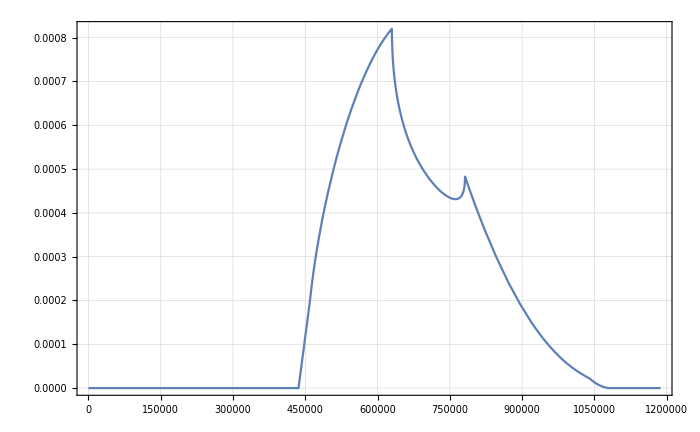

```mathematica
Plot[ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,p,Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False],{p,0.,pmax},PlotRange->All,PlotPoints->50]
```

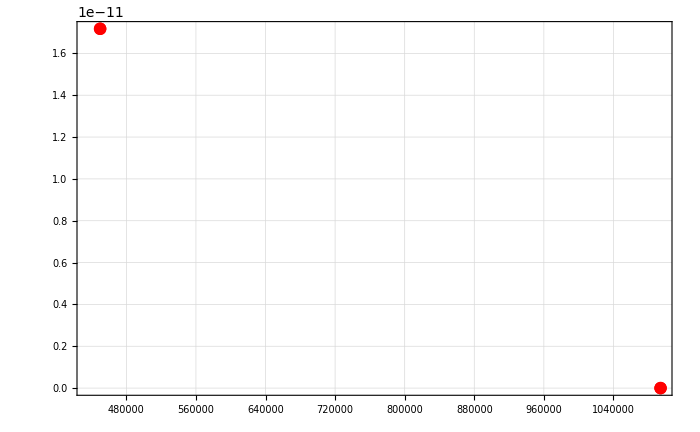

```mathematica
ListPlot[
{
{
pminApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pminApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pmaxApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pminApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pminApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pmaxApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
}
},PlotStyle->Red
]
```

General::munfl: Exp[-1952.21] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

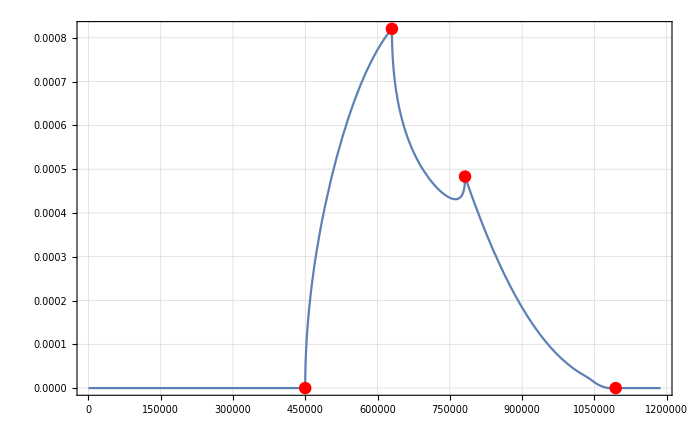

```mathematica
Show[
Plot[ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,p,Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False],{p,0.,pmax},PlotRange->All,PlotPoints->100],
ListPlot[
{
{
pminApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pminApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pmaxApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pminApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pminApertCases[0,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.,0.0,{Pi//N,Pi//N,pmaxApertCases[-Pi,0.,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
}
},PlotStyle->Red
]
]
```

General::munfl: Exp[-1952.21] is too small to represent as a normalized machine number; precision may be lost.

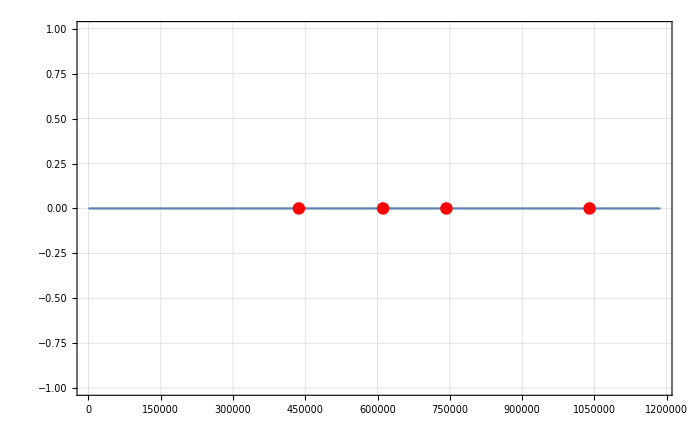

```mathematica
Show[
Plot[ManualphiAIntegrandAllLimits[0.,0.03,0.0,{Pi//N,Pi//N,p,Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False],{p,0.,pmax},PlotRange->All,PlotPoints->100],
ListPlot[
{
{
pminApertCases[-Pi,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.03,0.0,{Pi//N,Pi//N,pminApertCases[-Pi,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[0,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.03,0.0,{Pi//N,Pi//N,pmaxApertCases[0,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pminApertCases[0,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.03,0.0,{Pi//N,Pi//N,pminApertCases[0,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[-Pi,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.03,0.0,{Pi//N,Pi//N,pmaxApertCases[-Pi,0.03,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
}
},PlotStyle->Red
]
]
```

General::munfl: Exp[-966.245] is too small to represent as a normalized machine number; precision may be lost.

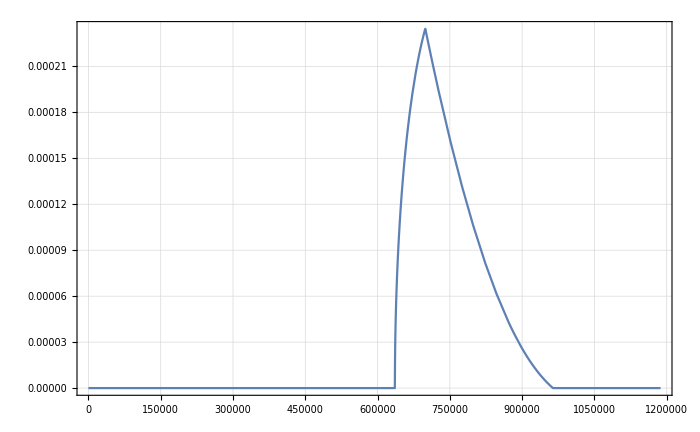

```mathematica
Plot[ManualphiAIntegrandAllLimits[0.,0.025,0.0,{Pi//N,Pi//N,p,Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False],{p,0.,pmax},PlotRange->All,PlotPoints->50]
```

General::munfl: Exp[-966.245] is too small to represent as a normalized machine number; precision may be lost.

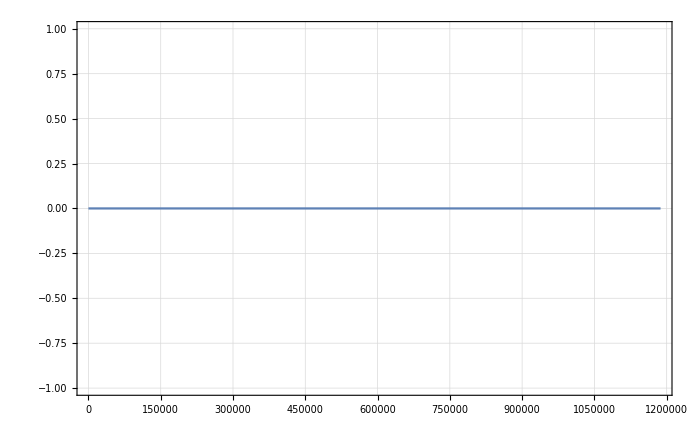

```mathematica
Plot[ManualphiAIntegrandAllLimits[0.,0.027,0.0,{Pi//N,Pi//N,p,Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False],{p,0.,pmax},PlotRange->All,PlotPoints->50]
```

General::munfl: Exp[-1952.21] is too small to represent as a normalized machine number; precision may be lost.

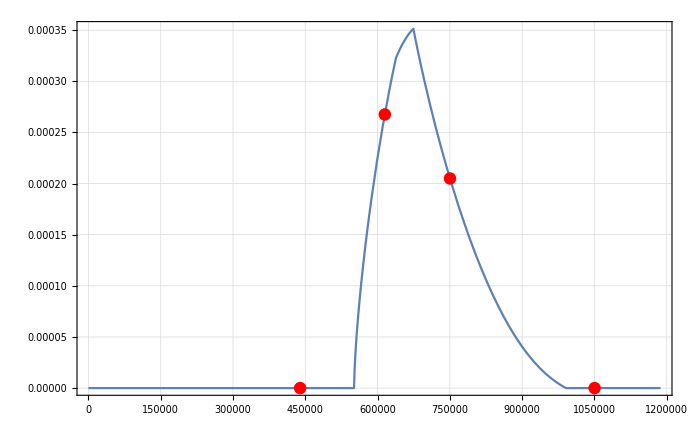

```mathematica
Show[
Plot[ManualphiAIntegrandAllLimits[0.,0.024,0.0,{Pi//N,Pi//N,p,Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False],{p,0.,pmax},PlotRange->All,PlotPoints->100],
ListPlot[
{
{
pminApertCases[-Pi,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.024,0.0,{Pi//N,Pi//N,pminApertCases[-Pi,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[0,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.024,0.0,{Pi//N,Pi//N,pmaxApertCases[0,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pminApertCases[0,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.024,0.0,{Pi//N,Pi//N,pminApertCases[0,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
},
{
pmaxApertCases[-Pi,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],ManualphiAIntegrandAllLimits[0.,0.024,0.0,{Pi//N,Pi//N,pmaxApertCases[-Pi,0.024,0.,Pi/4,Pi,0.2,1.,1.,1.,Pi,1.,1.,1.,-0.03,0.01],Pi/4.},{Pi//N,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.1,-0.9,0.1,0.09,0.9,0.1,-0.9},{0.01,0.035,-0.03,0.},False]
}
},PlotStyle->Red
]
]
```

## Further Testing of Integrand (p<40 issue)

```mathematica
ManualphiAIntegrandAllLimits[0.,0.02,-0.04,{-Pi/2-0.1,-Pi/2-0.1,0.0025,0.1},{3.141592653589793,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},True]
```

{{-3.14159,0.,0.,-3.14159,3.14159,-1.5708,-1.5708,-1.5708,-1.5708,3.14159},{-3.14159,-1.5708,0.,3.14159},{1.5708,1.5708,3.14159},{-2.35619,-0.785398,1.5708},{0.,0.,0.},0.}

```mathematica
ManualphiAIntegrandAllLimits[0.,0.02,-0.04,{-Pi/2-0.1,-Pi/2-0.1,25,0.1},{3.141592653589793,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},True]
```

{{-3.14159,0.,0.,-3.14159,3.14159,-1.5708,-1.5708,-1.5708,-1.5708,3.14159},{-3.14159,-1.5708,0.,3.14159},{1.5708,1.5708,3.14159},{-2.35619,-0.785398,1.5708},{0.,0.,0.},0.}

General::munfl: Exp[-3905.96] is too small to represent as a normalized machine number; precision may be lost.

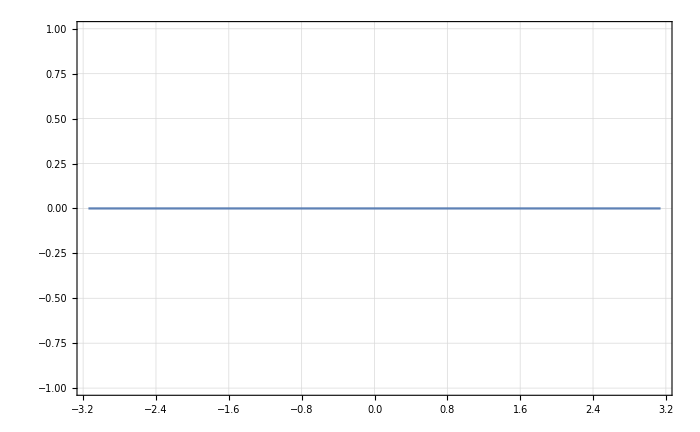

```mathematica
Plot[Integrand2DwNBeamCompiled[0.,0.0,-0.0,{-Pi/2-0.1,phiA,-Pi/2-0.1,6,0.1},{3.141592653589793,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.}],{phiA,-Pi,Pi}]
```

### ok, for small p > 0, there appears to be an issue???

```mathematica
ManualphiAIntegrandAllLimits[0.,0.02,-0.04,{-Pi/2-0.1,-Pi/2-0.1,40,0.1},{3.141592653589793,0.2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},False]
```

0.

```mathematica
Int2DwNBeamCompiledManualphiAAllLimitspLimitsX[0.,{{0.,0.}},{3.141592653589793,0.2,2,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4]
```

{3275.86}

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ElectronData180wFilter2DwNbeam=Table[{bin,FitFuncBinwNbeam[bin,0.,XYDatam05p75XOffset,{Pi//N,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4]},{bin,1,Length[XYDatam05p75XOffset]}]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Fri 28 Feb 2020 14:26:12

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.19635},{-3.14159,-1.5708},{-0.01,-0.01},{-3.14159,-1.5708}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.19635},{-3.14159,-1.5708},{-0.01,-0.01},{-1.5708,0.}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.19635},{-3.14159,-1.5708},{-0.01,-0.01},{0.,1.5708}}.

General::stop: Further output of NIntegrate::noprec will be suppressed during this calculation.

LinkObject::linkd: Unable to communicate with closed link LinkObject[38261@193.170.93.100,35583@193.170.93.100,470,11].

Kernels::rdead: Subkernel connected through KernelObject[3,193.170.93.100] appears dead.

LinkObject::linkn: Argument LinkObject[38261@193.170.93.100,35583@193.170.93.100,470,11] in LinkClose[LinkObject[38261@193.170.93.100,35583@193.170.93.100,470,11]] has an invalid LinkObject number; the link may be closed.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.19635},{-3.14159,-1.5708},{0.02,0.02},{-3.14159,-1.5708}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.19635},{-3.14159,-1.5708},{0.02,0.02},{-1.5708,0.}}.

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.19635},{-3.14159,-1.5708},{0.02,0.02},{0.,1.5708}}.

General::stop: Further output of NIntegrate::noprec will be suppressed during this calculation.

Part::partw: Part 10 of Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}] does not exist.

Part::partw: Part 11 of Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}] does not exist.

Part::partw: Part 12 of Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

{{1,{0.,56.4594/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],54.7445/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],53.1672/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{2,{0.,134.288/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],1147.58/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],1114.02/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{3,$Failed/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{4,{2996.85/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],2875.07/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],629.69/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],1119.74/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{5,{3656.03/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],3953.91/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],3613.37/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],1074.13/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{6,{991.427/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],2851.71/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],3275.86/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],2908.22/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{7,{1015.37/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],555.199/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],1461.74/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],1732.99/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{8,{1558.17/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],612.17/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],194.749/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],443.485/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{9,{560.241/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],500.262/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]],234.965/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}},{10,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦10⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{11,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦11⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{12,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦12⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{13,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦13⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{14,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦14⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{15,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦15⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{16,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦16⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{17,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦17⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{18,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦18⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{19,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦19⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{20,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦20⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{21,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦21⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{22,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦22⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{23,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦23⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{24,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦24⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{25,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦25⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{26,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦26⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{27,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦27⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{28,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦28⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{29,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦29⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{30,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦30⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{31,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦31⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{32,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦32⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{33,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦33⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{34,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦34⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]},{35,Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]⟦35⟧/Total[Join[{0.,56.4594,54.7445,53.1672},{0.,134.288,1147.58,1114.02},$Failed,{2996.85,2875.07,629.69,1119.74},{3656.03,3953.91,3613.37,1074.13},{991.427,2851.71,3275.86,2908.22},{1015.37,555.199,1461.74,1732.99},{1558.17,612.17,194.749,443.485},{560.241,500.262,234.965}]]}}

1.33706

```mathematica
IntegrandphiDVIntegrated[phiDet_?NumericQ,th0_?NumericQ]:=NIntegrate[ManualphiAIntegrandAllLimits[0.,0.,0.,{phiDV,phiDet,p,th0},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},False],

{p,0.,pmax},{phiDV,-Pi//N,Pi//N},PrecisionGoal->4,Method->"LocalAdaptive",AccuracyGoal->5,MinRecursion->3,MaxRecursion->10]
```

```mathematica
Int2DwNBeamCompiledManualphiAAllLimitspLimitsXManualInt[0.,{{0.,0.}},{Pi,Pi/4},{Pi,0.2,2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4][[1]]
```

859.876

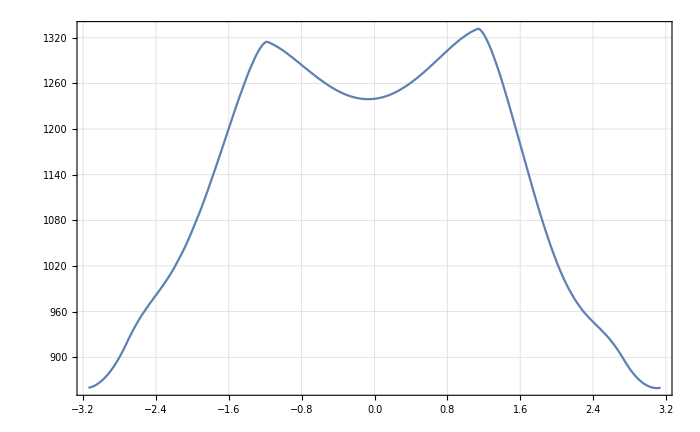

```mathematica
Plot[Int2DwNBeamCompiledManualphiAAllLimitspLimitsXManualInt[0.,{{0.,0.}},{phiDet,Pi/4},{Pi,0.2,2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4][[1]],{phiDet,-Pi,Pi},PlotPoints->10]
```

### 1994s

```mathematica
ManualphiAIntegrandAllLimits[0.,0.,0.,{-3,Pi,0.09,π/4},{π,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},False]
```

0.

```mathematica
Table[
NIntegrate[
ManualphiAIntegrandAllLimits[0,{{0,0}}[[bin,2]],{{0,0}}[[bin,1]],{phiDV,Pi,p,Pi/4},{Pi,0.2,1,1,1,1,1,1},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},False],(*{th0,0.,thetamax[rF]},{phiDet,-Pi//N,Pi//N},*)
{
p,
0.,
Sequence@@pLimitsApertXList[{{0,0}}[[bin,2]],{{0,0}}[[bin,1]],Pi/4,Pi,0.2,1,1,1,Pi,1,1,1,-0.03,0.01],
pmax
},
{phiDV,-Pi//N,Pi//N},PrecisionGoal->4,Method->"LocalAdaptive",AccuracyGoal->5,MinRecursion->3,MaxRecursion->10],
{bin,1,Length[{{0,0}}]}]
```

{859.713}

```mathematica
Table[i,{i,1,1}]
```

{1}

# Investigation: BRamp alpha=180°

## First test with BRxB = 0.2 T

```mathematica
XYDatam05p75XOffset=XYDataCreation[{0.00,0.06,-0.04,7},{-0.02,0.02,0.,5}]
```

{{-0.04,-0.02},{-0.04,-0.01},{-0.04,0.},{-0.04,0.01},{-0.04,0.02},{-0.03,-0.02},{-0.03,-0.01},{-0.03,0.},{-0.03,0.01},{-0.03,0.02},{-0.02,-0.02},{-0.02,-0.01},{-0.02,0.},{-0.02,0.01},{-0.02,0.02},{-0.01,-0.02},{-0.01,-0.01},{-0.01,0.},{-0.01,0.01},{-0.01,0.02},{-6.93889×10^-18,-0.02},{-6.93889×10^-18,-0.01},{-6.93889×10^-18,0.},{-6.93889×10^-18,0.01},{-6.93889×10^-18,0.02},{0.01,-0.02},{0.01,-0.01},{0.01,0.},{0.01,0.01},{0.01,0.02},{0.02,-0.02},{0.02,-0.01},{0.02,0.},{0.02,0.01},{0.02,0.02}}

### data without p limits, time calc of det points

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ElectronData180wFilter2DwNbeamNoPlimitsBinTime=Table[{bin,FitFuncBinwNbeam[bin,0.,XYDatam05p75XOffset,{Pi//N,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4]},{bin,1,Length[XYDatam05p75XOffset]}]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Fri 13 Mar 2020 14:17:42

{{1,{0.,0.000453543}},{2,{0.00122061,0.0357002408}},{3,{0.00118353,0.0335730641}},{4,{0.00114943,0.033611868}},{5,{0.,0.0004537217}},{6,{0.0029032,0.0336371333}},{7,{0.0248097,0.043913854}},{8,{0.0240842,0.0441425566}},{9,{0.0233627,0.0445917981}},{10,{0.00242836,0.02189914}},{11,{0.0151144,0.020034832}},{12,{0.0645866,0.022244672}},{13,{0.0647894,0.01777802}},{14,{0.0621568,0.015714106}},{15,{0.0136134,0.0279190819}},{16,{0.0242079,0.0538392823}},{17,{0.0790406,0.022697501}},{18,{0.0854805,0.020820899}},{19,{0.0781183,0.024380866}},{20,{0.0232219,0.0454954792}},{21,{0.0214339,0.0485644494}},{22,{0.0616516,0.0331660787}},{23,{0.0708215,0.020977216}},{24,{0.0628734,0.024062085}},{25,{0.0219515,0.0273134382}},{26,{0.012003,0.0282225868}},{27,{0.0316016,0.022324665}},{28,{0.0374659,0.022454752}},{29,{0.0336864,0.0323860319}},{30,{0.0132346,0.0288522393}},{31,{0.00421033,0.0346754888}},{32,{0.00958779,0.024464321}},{33,{0.012112,0.0351660254}},{34,{0.0108153,0.024354561}},{35,{0.00507975,0.0301144015}}}

0.91865

```mathematica
ListPlot3D[Transpose[{XYDatam05p75XOffset[[All,1]],XYDatam05p75XOffset[[All,2]],ElectronData180wFilter2DwNbeamNoPlimitsBinTime[[All,2,2]]*100}],InterpolationOrder->1,PlotLegends->Automatic]
```

-Graphics3D-

### Data with pX limits in integration

```mathematica
ParallelContext
```

```mathematica
ParallelMap
```

```mathematica
Kernels[]
```

{KernelObject[1,193.170.93.100],KernelObject[2,193.170.93.100],KernelObject[3,193.170.93.100],KernelObject[4,193.170.93.100],KernelObject[5,193.170.93.100],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local]}

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ElectronData180wFilter2DwNbeamBinTime=Table[{bin,FitFuncBinwNbeam[bin,0.,XYDatam05p75XOffset,{Pi//N,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4]},{bin,1,Length[XYDatam05p75XOffset]}]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Thu 12 Mar 2020 17:08:47

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.785398},{-3.14159,3.14159},{-0.02,-0.02},{-3.14159,3.14159}}.

{{1,{0.,0.0000114087}},{2,{0.00122617,0.0770033512}},{3,{0.00118892,0.0780737106}},{4,{0.00115265,0.080694416}},{5,{0.,0.0000114114}},{6,{0.00290639,0.0141544286}},{7,{0.024837,0.0180148382}},{8,{0.0241106,0.0181743262}},{9,{0.0233884,0.0183446243}},{10,{0.00243103,0.0151659473}},{11,{0.0151079,0.0318773151}},{12,{0.0646216,0.0152723701}},{13,{0.0648606,0.012351541}},{14,{0.0622251,0.010960575}},{15,{0.0136213,0.0288306602}},{16,{0.0240899,0.0212753919}},{17,{0.0791274,0.0157917364}},{18,{0.0855744,0.0144299702}},{19,{0.0782041,0.0167798968}},{20,{0.0231325,0.0181924942}},{21,{0.0214366,0.0321073569}},{22,{0.0615807,0.0482095326}},{23,{0.0706494,0.0316065285}},{24,{0.0626376,0.0470905822}},{25,{0.0219258,0.0502770264}},{26,{0.0120144,0.0210469588}},{27,{0.031633,0.0151944898}},{28,{0.0375164,0.0141948721}},{29,{0.0336851,0.0151277752}},{30,{0.0132432,0.0222788793}},{31,{0.0042254,0.0397481821}},{32,{0.00960086,0.0431147621}},{33,{0.0121253,0.0250947094}},{34,{0.010837,0.0426450742}},{35,{0.00508292,0.046852857}}}

2.509

```mathematica
Total[ElectronData180wFilter2DwNbeamBinTime[[All,2,2]]]
```

1.

### ah, time normed, so the following is %

```mathematica
Round[ElectronData180wFilter2DwNbeamBinTime[[All,2,2]]*100,0.01]
```

{0.,7.7,7.81,8.07,0.,1.42,1.8,1.82,1.83,1.52,3.19,1.53,1.24,1.1,2.88,2.13,1.58,1.44,1.68,1.82,3.21,4.82,3.16,4.71,5.03,2.1,1.52,1.42,1.51,2.23,3.97,4.31,2.51,4.26,4.69}

```mathematica
ListPlot3D[Transpose[{XYDatam05p75XOffset[[All,1]],XYDatam05p75XOffset[[All,2]],ElectronData180wFilter2DwNbeamBinTime[[All,2,2]]*100}],InterpolationOrder->1,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYDatam05p75XOffset[[All,1]],XYDatam05p75XOffset[[All,2]],ElectronData180wFilter2DwNbeamBinTime[[All,2,2]]*100-ElectronData180wFilter2DwNbeamNoPlimitsBinTime[[All,2,2]]*100}],InterpolationOrder->1,PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Round[ElectronData180wFilter2DwNbeamBinTime[[All,2,2]]*2.5,0.001]
```

{0.,0.193,0.195,0.202,0.,0.035,0.045,0.045,0.046,0.038,0.08,0.038,0.031,0.027,0.072,0.053,0.039,0.036,0.042,0.045,0.08,0.121,0.079,0.118,0.126,0.053,0.038,0.035,0.038,0.056,0.099,0.108,0.063,0.107,0.117}

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ElectronData180wFilter2DwNbeam=Table[{bin,FitFuncBinwNbeam[bin,0.,XYDatam05p75XOffset,{Pi//N,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4]},{bin,1,Length[XYDatam05p75XOffset]}]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Thu 12 Mar 2020 11:32:19

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.785398},{-3.14159,3.14159},{-0.02,-0.02},{-3.14159,3.14159}}.

{{1,0.},{2,0.00122617},{3,0.00118892},{4,0.00115265},{5,0.},{6,0.00290639},{7,0.024837},{8,0.0241106},{9,0.0233884},{10,0.00243103},{11,0.0151079},{12,0.0646216},{13,0.0648606},{14,0.0622251},{15,0.0136213},{16,0.0240899},{17,0.0791274},{18,0.0855744},{19,0.0782041},{20,0.0231325},{21,0.0214366},{22,0.0615807},{23,0.0706494},{24,0.0626376},{25,0.0219258},{26,0.0120144},{27,0.031633},{28,0.0375164},{29,0.0336851},{30,0.0132432},{31,0.0042254},{32,0.00960086},{33,0.0121253},{34,0.010837},{35,0.00508292}}

2.49963

```mathematica
ElectronData180wFilter2DwNbeamwpLimits={{1,0.},{2,0.0012261724761209976},{3,0.0011889180442045645},{4,0.0011526450969789458},{5,0.},{6,0.0029063866154371075},{7,0.024836982094769755},{8,0.02411064108749676},{9,0.023388412293458182},{10,0.002431027840261026},{11,0.015107919180660548},{12,0.06462157835697789},{13,0.06486062129670173},{14,0.06222507611283655},{15,0.013621285011099918},{16,0.02408993132454585},{17,0.07912739834236092},{18,0.085574411845807},{19,0.07820409059931456},{20,0.023132549466298963},{21,0.02143664187610249},{22,0.06158073933390345},{23,0.07064938744835599},{24,0.06263761690668118},{25,0.021925820433984836},{26,0.012014419432979855},{27,0.03163302399278594},{28,0.03751642631909189},{29,0.03368512982546828},{30,0.013243238289616157},{31,0.004225403268498586},{32,0.009600863258232364},{33,0.012125273894685},{34,0.010837043666199359},{35,0.005082924968083139}}
```

{{1,0.},{2,0.00122617},{3,0.00118892},{4,0.00115265},{5,0.},{6,0.00290639},{7,0.024837},{8,0.0241106},{9,0.0233884},{10,0.00243103},{11,0.0151079},{12,0.0646216},{13,0.0648606},{14,0.0622251},{15,0.0136213},{16,0.0240899},{17,0.0791274},{18,0.0855744},{19,0.0782041},{20,0.0231325},{21,0.0214366},{22,0.0615807},{23,0.0706494},{24,0.0626376},{25,0.0219258},{26,0.0120144},{27,0.031633},{28,0.0375164},{29,0.0336851},{30,0.0132432},{31,0.0042254},{32,0.00960086},{33,0.0121253},{34,0.010837},{35,0.00508292}}

### took 2.5h

```mathematica
Transpose[{XYDatam05p75XOffset[[All,1]],XYDatam05p75XOffset[[All,2]],ElectronData180wFilter2DwNbeamwpLimits[[All,2]]}]
```

{{-0.04,-0.02,0.},{-0.04,-0.01,0.00122617},{-0.04,0.,0.00118892},{-0.04,0.01,0.00115265},{-0.04,0.02,0.},{-0.03,-0.02,0.00290639},{-0.03,-0.01,0.024837},{-0.03,0.,0.0241106},{-0.03,0.01,0.0233884},{-0.03,0.02,0.00243103},{-0.02,-0.02,0.0151079},{-0.02,-0.01,0.0646216},{-0.02,0.,0.0648606},{-0.02,0.01,0.0622251},{-0.02,0.02,0.0136213},{-0.01,-0.02,0.0240899},{-0.01,-0.01,0.0791274},{-0.01,0.,0.0855744},{-0.01,0.01,0.0782041},{-0.01,0.02,0.0231325},{-6.93889×10^-18,-0.02,0.0214366},{-6.93889×10^-18,-0.01,0.0615807},{-6.93889×10^-18,0.,0.0706494},{-6.93889×10^-18,0.01,0.0626376},{-6.93889×10^-18,0.02,0.0219258},{0.01,-0.02,0.0120144},{0.01,-0.01,0.031633},{0.01,0.,0.0375164},{0.01,0.01,0.0336851},{0.01,0.02,0.0132432},{0.02,-0.02,0.0042254},{0.02,-0.01,0.00960086},{0.02,0.,0.0121253},{0.02,0.01,0.010837},{0.02,0.02,0.00508292}}

```mathematica
ListPlot3D[Transpose[{XYDatam05p75XOffset[[All,1]],XYDatam05p75XOffset[[All,2]],ElectronData180wFilter2DwNbeamwpLimits[[All,2]]}],InterpolationOrder->1,PlotLegends->Automatic]
```

-Graphics3D-

### relative Residual plot to without pLImits

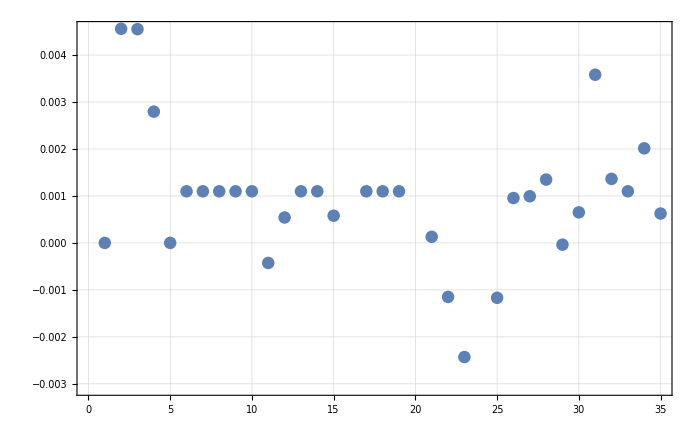

```mathematica
ListPlot[(ElectronData180wFilter2DwNbeamwpLimits[[All,2]]-ElectronData180wFilter2DwNbeam[[All,2]])/(If[#==0.,10000,#]&/@ElectronData180wFilter2DwNbeam[[All,2]])]
```

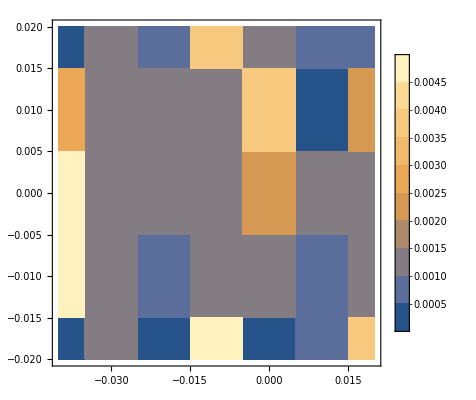

```mathematica
ListContourPlot[Transpose[{XYDatam05p75XOffset[[All,1]],XYDatam05p75XOffset[[All,2]],Abs[(ElectronData180wFilter2DwNbeamwpLimits[[All,2]]-ElectronData180wFilter2DwNbeam[[All,2]])/(If[#==0.,10000,#]&/@ElectronData180wFilter2DwNbeam[[All,2]])]}],InterpolationOrder->0,PlotLegends->Automatic]
```

### with p Limits seems to take much more time. not shown in previous investigations, but those were conducted for fixed xD,yD = 0,0. Could be that with limits, more computationally more heavy at borders

### Data

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ElectronData180wFilter2DwNbeam=Table[{bin,FitFuncBinwNbeam[bin,0.,XYDatam05p75XOffset,{Pi//N,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4]},{bin,1,Length[XYDatam05p75XOffset]}]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Fri 28 Feb 2020 17:15:40

{{1,0.},{2,0.00122061},{3,0.00118353},{4,0.00114943},{5,0.},{6,0.0029032},{7,0.0248097},{8,0.0240842},{9,0.0233627},{10,0.00242836},{11,0.0151144},{12,0.0645866},{13,0.0647894},{14,0.0621568},{15,0.0136134},{16,0.0242079},{17,0.0790406},{18,0.0854805},{19,0.0781183},{20,0.0232219},{21,0.0214339},{22,0.0616516},{23,0.0708215},{24,0.0628734},{25,0.0219515},{26,0.012003},{27,0.0316016},{28,0.0374659},{29,0.0336864},{30,0.0132346},{31,0.00421033},{32,0.00958779},{33,0.012112},{34,0.0108153},{35,0.00507975}}

0.858624

```mathematica
ElectronData180wFilter2DwNbeam={{1,0.},{2,0.0012206076491294582},{3,0.00118353202004242},{4,0.0011494324664478735},{5,0.},{6,0.0029031967240530795},{7,0.024809722739050293},{8,0.02408417872770584},{9,0.02336274254453904},{10,0.0024283597005440513},{11,0.015114375233558925},{12,0.06458663650942699},{13,0.06478943381563805},{14,0.06215678169094828},{15,0.013613395326988144},{16,0.024207936565049562},{17,0.0790405528866821},{18,0.08548049056235325},{19,0.07811825832986975},{20,0.023221904352080158},{21,0.021433861713929588},{22,0.06165164103147198},{23,0.07082147608215117},{24,0.06287343360386581},{25,0.02195146999886332},{26,0.012002953476232741},{27,0.03160163687156069},{28,0.03746588955962521},{29,0.03368637568717893},{30,0.013234626118350133},{31,0.00421032721696044},{32,0.009587792489117689},{33,0.012111965925361198},{34,0.01081526489854444},{35,0.0050797474826793755}}
```

{{1,0.},{2,0.00122061},{3,0.00118353},{4,0.00114943},{5,0.},{6,0.0029032},{7,0.0248097},{8,0.0240842},{9,0.0233627},{10,0.00242836},{11,0.0151144},{12,0.0645866},{13,0.0647894},{14,0.0621568},{15,0.0136134},{16,0.0242079},{17,0.0790406},{18,0.0854805},{19,0.0781183},{20,0.0232219},{21,0.0214339},{22,0.0616516},{23,0.0708215},{24,0.0628734},{25,0.0219515},{26,0.012003},{27,0.0316016},{28,0.0374659},{29,0.0336864},{30,0.0132346},{31,0.00421033},{32,0.00958779},{33,0.012112},{34,0.0108153},{35,0.00507975}}

### with memoization of pX limits

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ElectronData180wFilter2DwNbeampLimitsMemo=Table[{bin,FitFuncBinwNbeam[bin,0.,XYDatam05p75XOffset,{Pi//N,0.2,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4]},{bin,1,Length[XYDatam05p75XOffset]}]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Thu 12 Mar 2020 14:12:49

NIntegrate::noprec: There are not enough numbers in the working precision to calculate the internal points in the region {{0.,0.785398},{-3.14159,3.14159},{-0.02,-0.02},{-3.14159,3.14159}}.

{{1,0.},{2,0.00122617},{3,0.00118892},{4,0.00115265},{5,0.},{6,0.00290639},{7,0.024837},{8,0.0241106},{9,0.0233884},{10,0.00243103},{11,0.0151079},{12,0.0646216},{13,0.0648606},{14,0.0622251},{15,0.0136213},{16,0.0240899},{17,0.0791274},{18,0.0855744},{19,0.0782041},{20,0.0231325},{21,0.0214366},{22,0.0615807},{23,0.0706494},{24,0.0626376},{25,0.0219258},{26,0.0120144},{27,0.031633},{28,0.0375164},{29,0.0336851},{30,0.0132432},{31,0.0042254},{32,0.00960086},{33,0.0121253},{34,0.010837},{35,0.00508292}}

2.48463

### no, doesnt really help

### 0.928h for Int2DwNBeamCompiledManualphiAAllLimits (no p intervals), 9 cores, 0.858h for 10 cores

```mathematica
ListPlot3D[Transpose[{XYDatam05p75XOffset[[All,1]],XYDatam05p75XOffset[[All,2]],ElectronData180wFilter2DwNbeam[[All,2]]}]]
```

-Graphics3D-

### Vary fierz term b with dB offset for manual fit

```mathematica
t0=AbsoluteTime[];
Print[DateString[]]
ElectronData180wFilter2DwNbeamdB=
Table[Table[{bin,FitFuncBinwNbeam[bin,b,XYDatam05p75XOffset,{Pi//N,0.2+0.2*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-0.04,0.},4]},{bin,1,Length[XYDatam05p75XOffset]}],
{b,{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}}]
t1=AbsoluteTime[];
(t1-t0)/3600.
```

Sun 1 Mar 2020 11:57:26

{{{1,0.},{2,0.00121997},{3,0.00118291},{4,0.00114881},{5,0.},{6,0.00290224},{7,0.0247985},{8,0.0240755},{9,0.0233541},{10,0.00242757},{11,0.0151149},{12,0.0645776},{13,0.0647852},{14,0.0621483},{15,0.0136118},{16,0.0242094},{17,0.0790449},{18,0.085486},{19,0.0781211},{20,0.0232231},{21,0.0214371},{22,0.0616818},{23,0.0708299},{24,0.0628826},{25,0.0219511},{26,0.0120044},{27,0.0316049},{28,0.0374707},{29,0.0336907},{30,0.0132362},{31,0.00421038},{32,0.00958776},{33,0.0120861},{34,0.0108149},{35,0.00507939}},{{1,0.},{2,0.00122017},{3,0.0011831},{4,0.001149},{5,0.},{6,0.00290256},{7,0.0248015},{8,0.0240785},{9,0.023357},{10,0.00242785},{11,0.0151156},{12,0.0645814},{13,0.064789},{14,0.0621522},{15,0.0136125},{16,0.0242092},{17,0.0790449},{18,0.085486},{19,0.0781213},{20,0.0232231},{21,0.0214362},{22,0.0616792},{23,0.0708269},{24,0.0628801},{25,0.0219502},{26,0.0120035},{27,0.0316026},{28,0.0374681},{29,0.0336883},{30,0.0132352},{31,0.00421},{32,0.00958689},{33,0.012085},{34,0.0108139},{35,0.00507895}},{{1,0.},{2,0.00122037},{3,0.0011833},{4,0.00114919},{5,0.},{6,0.00290288},{7,0.0248046},{8,0.0240815},{9,0.0233599},{10,0.00242813},{11,0.0151164},{12,0.0645852},{13,0.0647929},{14,0.062156},{15,0.0136133},{16,0.0242091},{17,0.0790449},{18,0.085486},{19,0.0781215},{20,0.0232231},{21,0.0214352},{22,0.0616765},{23,0.0708239},{24,0.0628775},{25,0.0219493},{26,0.0120026},{27,0.0316003},{28,0.0374654},{29,0.0336859},{30,0.0132343},{31,0.00420962},{32,0.00958603},{33,0.012084},{34,0.010813},{35,0.0050785}},{{1,0.},{2,0.00122058},{3,0.0011835},{4,0.00114938},{5,0.},{6,0.0029032},{7,0.0248076},{8,0.0240844},{9,0.0233629},{10,0.00242841},{11,0.0151171},{12,0.0645889},{13,0.0647967},{14,0.0621598},{15,0.013614},{16,0.0242089},{17,0.0790449},{18,0.085486},{19,0.0781217},{20,0.023223},{21,0.0214342},{22,0.0616739},{23,0.0708208},{24,0.062875},{25,0.0219484},{26,0.0120017},{27,0.031598},{28,0.0374627},{29,0.0336835},{30,0.0132334},{31,0.00420924},{32,0.00958517},{33,0.0120829},{34,0.010812},{35,0.00507805}},{{1,0.},{2,0.00122078},{3,0.00118369},{4,0.00114957},{5,0.},{6,0.00290352},{7,0.0248106},{8,0.0240874},{9,0.0233658},{10,0.00242869},{11,0.0151179},{12,0.0645927},{13,0.0648005},{14,0.0621636},{15,0.0136148},{16,0.0242087},{17,0.0790448},{18,0.085486},{19,0.0781219},{20,0.023223},{21,0.0214332},{22,0.0616712},{23,0.0708178},{24,0.0628724},{25,0.0219474},{26,0.0120009},{27,0.0315957},{28,0.03746},{29,0.0336811},{30,0.0132325},{31,0.00420887},{32,0.00958431},{33,0.0120818},{34,0.010811},{35,0.0050776}},{{1,0.},{2,0.00122098},{3,0.00118389},{4,0.00114976},{5,0.},{6,0.00290384},{7,0.0248137},{8,0.0240904},{9,0.0233687},{10,0.00242897},{11,0.0151186},{12,0.0645964},{13,0.0648044},{14,0.0621674},{15,0.0136155},{16,0.0242086},{17,0.0790448},{18,0.0854861},{19,0.0781222},{20,0.023223},{21,0.0214322},{22,0.0616685},{23,0.0708148},{24,0.0628699},{25,0.0219465},{26,0.012},{27,0.0315934},{28,0.0374573},{29,0.0336787},{30,0.0132316},{31,0.00420849},{32,0.00958345},{33,0.0120807},{34,0.0108101},{35,0.00507716}}}

5.42392

### fit and show result

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

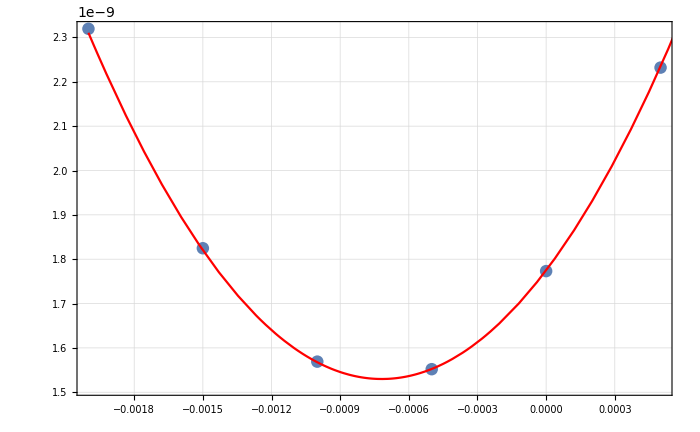
{b0 =  | -0.000718101
FittedModel[1.52986×10^-9+0.000475093 (0.000718101+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000718101 | 3.09684×10^-6 | -231.882 | 1.76865×10^-7
scale | 0.000475093 | 4.01399×10^-6 | 118.359 | 1.3297×10^-6
yoffset | 1.52986×10^-9 | 3.84932×10^-12 | 397.437 | 3.51282×10^-8 | ,-Graphics-}

```mathematica
test=Chi2FitandPlot[ElectronData180wFilter2DwNbeam[[All,2]],ElectronData180wFilter2DwNbeamdB,{-0.002,-0.0015,-0.001,-0.0005,0.,0.0005}]
```

```mathematica
test[[1,1,1,2]]
```

-0.000718101

```mathematica
-0.0007181007445433516/(5*10^-5)
```

-14.362

## BRxB ramp sensitivity of 0.15,0.3,0.4,0.8,1,1.2 T

```mathematica
BRxBList={0.4,0.6,0.8,1.,1.2};
```

```mathematica
RoughDriftDistance=Round[Table[D1stBPolyGrad[pmax,Pi,Pi/4,BRxB,1,0.,1,1,1]+2rG[pmax,Pi/4,BRxB]+0.01,{BRxB,BRxBList}],0.01]*0.8
```

{0.048,0.032,0.024,0.024,0.024}

### lets do without xOff to be sure of the correct XY range

```mathematica
XYDataBRamp=Table[XYDataCreation[{-0.005,xmax,0.,9},{-0.02,0.02,0.,5}],{xmax,RoughDriftDistance}]
```

{{{-0.005,-0.02},{-0.005,-0.01},{-0.005,0.},{-0.005,0.01},{-0.005,0.02},{0.001625,-0.02},{0.001625,-0.01},{0.001625,0.},{0.001625,0.01},{0.001625,0.02},{0.00825,-0.02},{0.00825,-0.01},{0.00825,0.},{0.00825,0.01},{0.00825,0.02},{0.014875,-0.02},{0.014875,-0.01},{0.014875,0.},{0.014875,0.01},{0.014875,0.02},{0.0215,-0.02},{0.0215,-0.01},{0.0215,0.},{0.0215,0.01},{0.0215,0.02},{0.028125,-0.02},{0.028125,-0.01},{0.028125,0.},{0.028125,0.01},{0.028125,0.02},{0.03475,-0.02},{0.03475,-0.01},{0.03475,0.},{0.03475,0.01},{0.03475,0.02},{0.041375,-0.02},{0.041375,-0.01},{0.041375,0.},{0.041375,0.01},{0.041375,0.02},{0.048,-0.02},{0.048,-0.01},{0.048,0.},{0.048,0.01},{0.048,0.02}},{{-0.005,-0.02},{-0.005,-0.01},{-0.005,0.},{-0.005,0.01},{-0.005,0.02},{-0.000375,-0.02},{-0.000375,-0.01},{-0.000375,0.},{-0.000375,0.01},{-0.000375,0.02},{0.00425,-0.02},{0.00425,-0.01},{0.00425,0.},{0.00425,0.01},{0.00425,0.02},{0.008875,-0.02},{0.008875,-0.01},{0.008875,0.},{0.008875,0.01},{0.008875,0.02},{0.0135,-0.02},{0.0135,-0.01},{0.0135,0.},{0.0135,0.01},{0.0135,0.02},{0.018125,-0.02},{0.018125,-0.01},{0.018125,0.},{0.018125,0.01},{0.018125,0.02},{0.02275,-0.02},{0.02275,-0.01},{0.02275,0.},{0.02275,0.01},{0.02275,0.02},{0.027375,-0.02},{0.027375,-0.01},{0.027375,0.},{0.027375,0.01},{0.027375,0.02},{0.032,-0.02},{0.032,-0.01},{0.032,0.},{0.032,0.01},{0.032,0.02}},{{-0.005,-0.02},{-0.005,-0.01},{-0.005,0.},{-0.005,0.01},{-0.005,0.02},{-0.001375,-0.02},{-0.001375,-0.01},{-0.001375,0.},{-0.001375,0.01},{-0.001375,0.02},{0.00225,-0.02},{0.00225,-0.01},{0.00225,0.},{0.00225,0.01},{0.00225,0.02},{0.005875,-0.02},{0.005875,-0.01},{0.005875,0.},{0.005875,0.01},{0.005875,0.02},{0.0095,-0.02},{0.0095,-0.01},{0.0095,0.},{0.0095,0.01},{0.0095,0.02},{0.013125,-0.02},{0.013125,-0.01},{0.013125,0.},{0.013125,0.01},{0.013125,0.02},{0.01675,-0.02},{0.01675,-0.01},{0.01675,0.},{0.01675,0.01},{0.01675,0.02},{0.020375,-0.02},{0.020375,-0.01},{0.020375,0.},{0.020375,0.01},{0.020375,0.02},{0.024,-0.02},{0.024,-0.01},{0.024,0.},{0.024,0.01},{0.024,0.02}},{{-0.005,-0.02},{-0.005,-0.01},{-0.005,0.},{-0.005,0.01},{-0.005,0.02},{-0.001375,-0.02},{-0.001375,-0.01},{-0.001375,0.},{-0.001375,0.01},{-0.001375,0.02},{0.00225,-0.02},{0.00225,-0.01},{0.00225,0.},{0.00225,0.01},{0.00225,0.02},{0.005875,-0.02},{0.005875,-0.01},{0.005875,0.},{0.005875,0.01},{0.005875,0.02},{0.0095,-0.02},{0.0095,-0.01},{0.0095,0.},{0.0095,0.01},{0.0095,0.02},{0.013125,-0.02},{0.013125,-0.01},{0.013125,0.},{0.013125,0.01},{0.013125,0.02},{0.01675,-0.02},{0.01675,-0.01},{0.01675,0.},{0.01675,0.01},{0.01675,0.02},{0.020375,-0.02},{0.020375,-0.01},{0.020375,0.},{0.020375,0.01},{0.020375,0.02},{0.024,-0.02},{0.024,-0.01},{0.024,0.},{0.024,0.01},{0.024,0.02}},{{-0.005,-0.02},{-0.005,-0.01},{-0.005,0.},{-0.005,0.01},{-0.005,0.02},{-0.001375,-0.02},{-0.001375,-0.01},{-0.001375,0.},{-0.001375,0.01},{-0.001375,0.02},{0.00225,-0.02},{0.00225,-0.01},{0.00225,0.},{0.00225,0.01},{0.00225,0.02},{0.005875,-0.02},{0.005875,-0.01},{0.005875,0.},{0.005875,0.01},{0.005875,0.02},{0.0095,-0.02},{0.0095,-0.01},{0.0095,0.},{0.0095,0.01},{0.0095,0.02},{0.013125,-0.02},{0.013125,-0.01},{0.013125,0.},{0.013125,0.01},{0.013125,0.02},{0.01675,-0.02},{0.01675,-0.01},{0.01675,0.},{0.01675,0.01},{0.01675,0.02},{0.020375,-0.02},{0.020375,-0.01},{0.020375,0.},{0.020375,0.01},{0.020375,0.02},{0.024,-0.02},{0.024,-0.01},{0.024,0.},{0.024,0.01},{0.024,0.02}}}

```mathematica
ClearAll[DataAndManualbVary]
```

```mathematica
bvary={-0.002,-0.0015,-0.0001,-0.0005,0.,0.0005}
```

{-0.002,-0.0015,-0.0001,-0.0005,0.,0.0005}

```mathematica
(*DataAndManualbVary[BRxBIndex_]:=Module[
{data,bvary,t0,t1,t2},
t0=AbsoluteTime[];
Print[DateString[]];
data=Table[
{
bin,
FitFuncBinwNbeam[bin,0.,XYDataBRamp[[BRxBIndex]],{Pi//N,BRxBList[[BRxBIndex]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-RoughDriftDistance[[BRxBIndex]]/2,0.},4]
},{bin,1,32}];
t1=AbsoluteTime[];
Print["time for data: ",(t1-t0)/3600.];
bvary=Table[Table[
{
bin,
FitFuncBinwNbeam[bin,b,XYDataBRamp[[BRxBIndex]],{Pi//N,BRxBList[[BRxBIndex]]+BRxBList[[BRxBIndex]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,-RoughDriftDistance[[BRxBIndex]]/2,0.},4]
},
{bin,1,32}],
{b,{-0.0015,-0.0009,-0.0004,0.,0.0006}}];
t2=AbsoluteTime[];
Print["time for bvary: ",(t2-t1)/3600.];
{data,bvary}
]*)
```

```mathematica
TransferData[b_?NumericQ,XYData_List,{alpha_?NumericQ,BRxB_?NumericQ,rF_?NumericQ,rA_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,R_?NumericQ,G1_?NumericQ,G2_?NumericQ},{twx_?NumericQ,plx_?NumericQ,k1x_?NumericQ,k2x_?NumericQ,k3x_?NumericQ,twy_?NumericQ,ply_?NumericQ,k1y_?NumericQ,k2y_?NumericQ,k3y_?NumericQ},{xAA_?NumericQ,yAA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ},IntPrec_]:=Module[
{t0=AbsoluteTime[],t1,result},
Print[DateString[]];
result=Table[
{
bin,
FitFuncBinwNbeam[bin,b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec]
},
{bin,1,Length[XYData]}];
t1=AbsoluteTime[];
Print["data time= ",(t1-t0)/3600.];
result
]
```

```mathematica
ManualbvaryData[bList_List,XYData_List,{alpha_?NumericQ,BRxB_?NumericQ,rF_?NumericQ,rA_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,R_?NumericQ,G1_?NumericQ,G2_?NumericQ},{twx_?NumericQ,plx_?NumericQ,k1x_?NumericQ,k2x_?NumericQ,k3x_?NumericQ,twy_?NumericQ,ply_?NumericQ,k1y_?NumericQ,k2y_?NumericQ,k3y_?NumericQ},{xAA_?NumericQ,yAA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ},IntPrec_]:=Module[
{t0=AbsoluteTime[],result,t1},
Print[DateString[]];
result=Table[
{
b,
Table[
{
bin,
FitFuncBinwNbeam[bin,b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec]
},
{bin,1,Length[XYData]}]
},
{b,bList}];
t1=AbsoluteTime[];
Print["bvary time= ",(t1-t0)/3600.];
result
]
```

```mathematica
CloseKernels[]
```

{KernelObject[61,193.170.93.100,<defunct>],KernelObject[62,193.170.93.100,<defunct>],KernelObject[63,193.170.93.100,<defunct>],KernelObject[64,193.170.93.100,<defunct>],KernelObject[65,193.170.93.100,<defunct>],KernelObject[66,local,<defunct>],KernelObject[67,local,<defunct>],KernelObject[68,local,<defunct>],KernelObject[69,local,<defunct>]}

```mathematica
LaunchKernels[]
```

{KernelObject[70,193.170.93.100],KernelObject[71,193.170.93.100],KernelObject[72,193.170.93.100],KernelObject[73,193.170.93.100],KernelObject[74,193.170.93.100],KernelObject[75,local],KernelObject[76,local],KernelObject[77,local],KernelObject[78,local]}

```mathematica
BRamp400Data=TransferData[0.,XYDataBRamp[[1]],{Pi//N,BRxBList[[1]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Tue 3 Mar 2020 18:11:56

data time= 0.865502

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.0000511965},{7,0.0124413},{8,0.0120707},{9,0.0116761},{10,0.0000263197},{11,0.00559889},{12,0.0684651},{13,0.0668136},{14,0.0652835},{15,0.00475104},{16,0.0171829},{17,0.108626},{18,0.108039},{19,0.106826},{20,0.0161224},{21,0.0161304},{22,0.0789523},{23,0.0811808},{24,0.080979},{25,0.0166427},{26,0.00675845},{27,0.0277982},{28,0.0301347},{29,0.0303852},{30,0.00772842},{31,0.00130416},{32,0.00452035},{33,0.00512874},{34,0.00528239},{35,0.0017024},{36,0.0000871782},{37,0.000331804},{38,0.000393749},{39,0.000432386},{40,0.000143331},{41,2.27855×10^-7},{42,1.74757×10^-6},{43,2.64237×10^-6},{44,3.83447×10^-6},{45,1.12086×10^-6}}

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[1,All,1]],XYDataBRamp[[1,All,2]],BRamp400Data[[All,2]]}]]
```

-Graphics3D-

```mathematica
BRamp400bvary=ManualbvaryData[bvary,XYDataBRamp[[1]],{Pi//N,BRxBList[[1]]+BRxBList[[1]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Tue 3 Mar 2020 19:03:52

bvary time= 4.82933

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.0000511783},{7,0.012436},{8,0.0120656},{9,0.011697},{10,0.0000263124},{11,0.00559843},{12,0.0684527},{13,0.0668005},{14,0.065271},{15,0.00475064},{16,0.0171838},{17,0.108628},{18,0.108041},{19,0.106826},{20,0.016123},{21,0.0161324},{22,0.0789612},{23,0.0811893},{24,0.0809808},{25,0.0166445},{26,0.00675884},{27,0.0277946},{28,0.0301366},{29,0.0303877},{30,0.00772892},{31,0.00130401},{32,0.00451985},{33,0.00512823},{34,0.00528217},{35,0.00170227},{36,0.0000871257},{37,0.000331658},{38,0.000393509},{39,0.000432221},{40,0.000143258},{41,2.27546×10^-7},{42,1.7429×10^-6},{43,2.63747×10^-6},{44,3.82573×10^-6},{45,1.1183×10^-6}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.0000511841},{7,0.0124377},{8,0.0120672},{9,0.0116986},{10,0.0000263154},{11,0.00559866},{12,0.0684576},{13,0.0668053},{14,0.0652758},{15,0.00475086},{16,0.0171837},{17,0.108628},{18,0.108042},{19,0.106827},{20,0.0161229},{21,0.0161316},{22,0.0789577},{23,0.0811857},{24,0.0809773},{25,0.0166437},{26,0.00675832},{27,0.0277925},{28,0.0301343},{29,0.0303854},{30,0.00772834},{31,0.00130389},{32,0.00451943},{33,0.00512775},{34,0.00528168},{35,0.00170211},{36,0.0000871162},{37,0.000331622},{38,0.000393466},{39,0.000432175},{40,0.000143243},{41,2.27519×10^-7},{42,1.74269×10^-6},{43,2.63715×10^-6},{44,3.82527×10^-6},{45,1.11816×10^-6}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.0000512001},{7,0.0124425},{8,0.0120719},{9,0.0117032},{10,0.000026324},{11,0.00559931},{12,0.0684712},{13,0.0668189},{14,0.0652893},{15,0.00475148},{16,0.0171833},{17,0.10863},{18,0.108044},{19,0.106829},{20,0.0161227},{21,0.0161294},{22,0.0789478},{23,0.0811757},{24,0.0809676},{25,0.0166416},{26,0.00675686},{27,0.0277865},{28,0.030128},{29,0.030379},{30,0.00772672},{31,0.00130354},{32,0.00451825},{33,0.00512641},{34,0.0052803},{35,0.00170166},{36,0.0000870894},{37,0.000331522},{38,0.000393348},{39,0.000432046},{40,0.000143199},{41,2.27441×10^-7},{42,1.74209×10^-6},{43,2.63626×10^-6},{44,3.82399×10^-6},{45,1.11779×10^-6}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.0000511955},{7,0.0124411},{8,0.0120706},{9,0.0117019},{10,0.0000263216},{11,0.00559912},{12,0.0684673},{13,0.066815},{14,0.0652854},{15,0.00475131},{16,0.0171834},{17,0.108629},{18,0.108043},{19,0.106829},{20,0.0161228},{21,0.01613},{22,0.0789506},{23,0.0811786},{24,0.0809704},{25,0.0166422},{26,0.00675728},{27,0.0277882},{28,0.0301298},{29,0.0303809},{30,0.00772718},{31,0.00130364},{32,0.00451858},{33,0.00512679},{34,0.0052807},{35,0.00170179},{36,0.0000870971},{37,0.00033155},{38,0.000393382},{39,0.000432083},{40,0.000143212},{41,2.27463×10^-7},{42,1.74226×10^-6},{43,2.63652×10^-6},{44,3.82435×10^-6},{45,1.11789×10^-6}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.0000512013},{7,0.0124428},{8,0.0120722},{9,0.0117035},{10,0.0000263246},{11,0.00559935},{12,0.0684721},{13,0.0668198},{14,0.0652902},{15,0.00475153},{16,0.0171833},{17,0.10863},{18,0.108044},{19,0.106829},{20,0.0161227},{21,0.0161292},{22,0.0789471},{23,0.081175},{24,0.0809669},{25,0.0166414},{26,0.00675676},{27,0.0277861},{28,0.0301275},{29,0.0303786},{30,0.00772661},{31,0.00130352},{32,0.00451816},{33,0.00512631},{34,0.00528021},{35,0.00170163},{36,0.0000870875},{37,0.000331515},{38,0.000393339},{39,0.000432037},{40,0.000143196},{41,2.27435×10^-7},{42,1.74205×10^-6},{43,2.6362×10^-6},{44,3.82389×10^-6},{45,1.11776×10^-6}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000051207},{7,0.0124445},{8,0.0120739},{9,0.0117051},{10,0.0000263277},{11,0.00559958},{12,0.068477},{13,0.0668246},{14,0.065295},{15,0.00475175},{16,0.0171831},{17,0.10863},{18,0.108044},{19,0.10683},{20,0.0161226},{21,0.0161284},{22,0.0789435},{23,0.0811714},{24,0.0809635},{25,0.0166407},{26,0.00675624},{27,0.027784},{28,0.0301252},{29,0.0303763},{30,0.00772603},{31,0.00130339},{32,0.00451774},{33,0.00512583},{34,0.00527972},{35,0.00170147},{36,0.000087078},{37,0.000331479},{38,0.000393297},{39,0.000431991},{40,0.000143181},{41,2.27407×10^-7},{42,1.74184×10^-6},{43,2.63588×10^-6},{44,3.82344×10^-6},{45,1.11762×10^-6}}}}

```mathematica
BRamp600Data=TransferData[0.,XYDataBRamp[[2]],{Pi//N,BRxBList[[2]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Tue 3 Mar 2020 23:53:38

data time= 0.834876

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0102228},{8,0.00991901},{9,0.00964363},{10,0.},{11,0.00154451},{12,0.0559948},{13,0.0547798},{14,0.053576},{15,0.00121048},{16,0.00728646},{17,0.104553},{18,0.103388},{19,0.102212},{20,0.00664081},{21,0.0104589},{22,0.0925354},{23,0.0931434},{24,0.0936755},{25,0.0103739},{26,0.00617093},{27,0.0418799},{28,0.0432752},{29,0.0446322},{30,0.00676905},{31,0.00163037},{32,0.00906863},{33,0.00967968},{34,0.010341},{35,0.00201333},{36,0.000166274},{37,0.000868396},{38,0.000962661},{39,0.00106089},{40,0.000246946},{41,2.09622×10^-6},{42,0.0000177566},{43,0.0000225568},{44,0.0000285247},{45,5.53744×10^-6}}

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[2,All,1]],XYDataBRamp[[2,All,2]],BRamp600Data[[All,2]]}]]
```

-Graphics3D-

```mathematica
BRamp600bvary=ManualbvaryData[bvary,XYDataBRamp[[2]],{Pi//N,BRxBList[[2]]+BRxBList[[2]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 00:43:43

bvary time= 4.97329

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0102198},{8,0.00991376},{9,0.00963989},{10,0.},{11,0.00154448},{12,0.0559855},{13,0.0547707},{14,0.0535664},{15,0.00121044},{16,0.00728702},{17,0.104551},{18,0.103386},{19,0.102205},{20,0.0066414},{21,0.0104601},{22,0.0925441},{23,0.0931517},{24,0.0936842},{25,0.010375},{26,0.00617149},{27,0.041884},{28,0.0432796},{29,0.0446458},{30,0.0067697},{31,0.0016303},{32,0.00906798},{33,0.00967924},{34,0.0103409},{35,0.00201338},{36,0.000166263},{37,0.000868212},{38,0.000962471},{39,0.00106065},{40,0.000246883},{41,2.09281×10^-6},{42,0.0000177336},{43,0.0000225354},{44,0.0000284839},{45,5.53485×10^-6}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0102212},{8,0.0099151},{9,0.00964119},{10,0.},{11,0.00154451},{12,0.0559893},{13,0.0547745},{14,0.0535702},{15,0.00121047},{16,0.00728688},{17,0.104553},{18,0.103388},{19,0.102207},{20,0.00664129},{21,0.0104596},{22,0.0925414},{23,0.0931491},{24,0.0936816},{25,0.0103746},{26,0.00617106},{27,0.0418813},{28,0.0432769},{29,0.044643},{30,0.00676924},{31,0.00163015},{32,0.00906718},{33,0.0096784},{34,0.01034},{35,0.0020132},{36,0.000166245},{37,0.000868123},{38,0.000962373},{39,0.00106054},{40,0.000246858},{41,2.09256×10^-6},{42,0.0000177316},{43,0.0000225328},{44,0.0000284806},{45,5.53421×10^-6}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.010225},{8,0.00991883},{9,0.00964484},{10,0.},{11,0.0015446},{12,0.0559999},{13,0.0547851},{14,0.0535808},{15,0.00121056},{16,0.00728646},{17,0.104558},{18,0.103394},{19,0.102213},{20,0.00664098},{21,0.0104583},{22,0.0925339},{23,0.0931418},{24,0.0936745},{25,0.0103734},{26,0.00616987},{27,0.0418737},{28,0.0432692},{29,0.0446352},{30,0.00676797},{31,0.00162975},{32,0.00906497},{33,0.00967604},{34,0.0103375},{35,0.00201271},{36,0.000166197},{37,0.000867874},{38,0.000962098},{39,0.00106024},{40,0.000246787},{41,2.09186×10^-6},{42,0.0000177258},{43,0.0000225254},{44,0.0000284714},{45,5.5324×10^-6}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0102239},{8,0.00991776},{9,0.0096438},{10,0.},{11,0.00154458},{12,0.0559969},{13,0.0547821},{14,0.0535777},{15,0.00121054},{16,0.00728658},{17,0.104556},{18,0.103392},{19,0.102211},{20,0.00664106},{21,0.0104587},{22,0.0925361},{23,0.0931439},{24,0.0936765},{25,0.0103738},{26,0.00617021},{27,0.0418759},{28,0.0432714},{29,0.0446374},{30,0.00676834},{31,0.00162986},{32,0.0090656},{33,0.00967671},{34,0.0103382},{35,0.00201285},{36,0.000166211},{37,0.000867945},{38,0.000962177},{39,0.00106033},{40,0.000246807},{41,2.09206×10^-6},{42,0.0000177274},{43,0.0000225275},{44,0.000028474},{45,5.53292×10^-6}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0102253},{8,0.0099191},{9,0.0096451},{10,0.},{11,0.00154461},{12,0.0560007},{13,0.0547859},{14,0.0535815},{15,0.00121057},{16,0.00728643},{17,0.104558},{18,0.103394},{19,0.102213},{20,0.00664095},{21,0.0104582},{22,0.0925334},{23,0.0931413},{24,0.093674},{25,0.0103733},{26,0.00616978},{27,0.0418732},{28,0.0432686},{29,0.0446346},{30,0.00676788},{31,0.00162972},{32,0.00906481},{33,0.00967587},{34,0.0103373},{35,0.00201267},{36,0.000166193},{37,0.000867857},{38,0.000962079},{39,0.00106022},{40,0.000246782},{41,2.09181×10^-6},{42,0.0000177254},{43,0.0000225249},{44,0.0000284708},{45,5.53227×10^-6}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0102266},{8,0.00992043},{9,0.00964641},{10,0.},{11,0.00154464},{12,0.0560045},{13,0.0547897},{14,0.0535853},{15,0.0012106},{16,0.00728629},{17,0.10456},{18,0.103396},{19,0.102215},{20,0.00664084},{21,0.0104578},{22,0.0925307},{23,0.0931387},{24,0.0936714},{25,0.0103729},{26,0.00616935},{27,0.0418705},{28,0.0432659},{29,0.0446318},{30,0.00676743},{31,0.00162957},{32,0.00906402},{33,0.00967503},{34,0.0103364},{35,0.0020125},{36,0.000166176},{37,0.000867768},{38,0.000961981},{39,0.00106012},{40,0.000246756},{41,2.09157×10^-6},{42,0.0000177233},{43,0.0000225223},{44,0.0000284675},{45,5.53163×10^-6}}}}

```mathematica
BRamp800Data=TransferData[0.,XYDataBRamp[[3]],{Pi//N,BRxBList[[3]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 05:42:07

data time= 0.561695

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926619},{8,0.00899548},{9,0.00872213},{10,0.},{11,0.000336707},{12,0.0493727},{13,0.0482705},{14,0.0472382},{15,0.000220915},{16,0.00292363},{17,0.093558},{18,0.0926273},{19,0.0916156},{20,0.00260758},{21,0.00482249},{22,0.0973866},{23,0.0975569},{24,0.097722},{25,0.00468185},{26,0.00445104},{27,0.0557594},{28,0.0568992},{29,0.0579905},{30,0.00463639},{31,0.0017249},{32,0.016227},{33,0.0170315},{34,0.017891},{35,0.00201495},{36,0.000258224},{37,0.0019898},{38,0.00216928},{39,0.00236231},{40,0.000353859},{41,7.47975×10^-6},{42,0.0000820516},{43,0.0000971629},{44,0.000113963},{45,0.0000151419}}

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[3,All,1]],XYDataBRamp[[3,All,2]],BRamp800Data[[All,2]]}]]
```

-Graphics3D-

```mathematica
BRamp800bvary=ManualbvaryData[bvary,XYDataBRamp[[3]],{Pi//N,BRxBList[[3]]+BRxBList[[3]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 06:15:50

bvary time= 3.31177

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926266},{8,0.00899202},{9,0.00871869},{10,0.},{11,0.000336728},{12,0.0493658},{13,0.0482629},{14,0.0472308},{15,0.000220921},{16,0.002924},{17,0.0935553},{18,0.0926244},{19,0.0916124},{20,0.0026079},{21,0.00482311},{22,0.0973916},{23,0.0975615},{24,0.0977268},{25,0.00468239},{26,0.00445146},{27,0.0557656},{28,0.0569081},{29,0.0579968},{30,0.00463683},{31,0.00172492},{32,0.0162278},{33,0.017032},{34,0.0178937},{35,0.002015},{36,0.000258139},{37,0.00198925},{38,0.00216902},{39,0.00236202},{40,0.000353794},{41,7.47315×10^-6},{42,0.0000819996},{43,0.0000970664},{44,0.000113889},{45,0.0000151289}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926386},{8,0.0089932},{9,0.00871984},{10,0.},{11,0.000336728},{12,0.0493688},{13,0.048266},{14,0.0472339},{15,0.000220923},{16,0.00292389},{17,0.0935572},{18,0.0926263},{19,0.0916144},{20,0.00260781},{21,0.00482285},{22,0.0973903},{23,0.0975603},{24,0.0977256},{25,0.00468215},{26,0.00445117},{27,0.0557628},{28,0.0569053},{29,0.057994},{30,0.00463654},{31,0.00172477},{32,0.0162266},{33,0.0170306},{34,0.0178923},{35,0.00201483},{36,0.000258113},{37,0.00198906},{38,0.00216881},{39,0.00236179},{40,0.000353758},{41,7.47228×10^-6},{42,0.0000819904},{43,0.0000970555},{44,0.000113877},{45,0.0000151272}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926723},{8,0.00899649},{9,0.00872306},{10,0.},{11,0.00033673},{12,0.0493774},{13,0.0482745},{14,0.0472425},{15,0.000220927},{16,0.00292358},{17,0.0935625},{18,0.0926318},{19,0.09162},{20,0.00260755},{21,0.00482214},{22,0.0973866},{23,0.0975568},{24,0.0977223},{25,0.00468147},{26,0.00445037},{27,0.0557549},{28,0.0568974},{29,0.057986},{30,0.00463573},{31,0.00172436},{32,0.0162229},{33,0.0170269},{34,0.0178884},{35,0.00201437},{36,0.00025804},{37,0.00198852},{38,0.00216822},{39,0.00236115},{40,0.00035366},{41,7.46987×10^-6},{42,0.0000819646},{43,0.0000970252},{44,0.000113841},{45,0.0000151224}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926627},{8,0.00899555},{9,0.00872214},{10,0.},{11,0.000336729},{12,0.049375},{13,0.0482721},{14,0.04724},{15,0.000220926},{16,0.00292367},{17,0.093561},{18,0.0926302},{19,0.0916184},{20,0.00260762},{21,0.00482234},{22,0.0973877},{23,0.0975578},{24,0.0977233},{25,0.00468167},{26,0.0044506},{27,0.0557572},{28,0.0568996},{29,0.0579883},{30,0.00463596},{31,0.00172448},{32,0.016224},{33,0.0170279},{34,0.0178895},{35,0.0020145},{36,0.000258061},{37,0.00198867},{38,0.00216839},{39,0.00236134},{40,0.000353688},{41,7.47056×10^-6},{42,0.000081972},{43,0.0000970339},{44,0.000113851},{45,0.0000151238}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926747},{8,0.00899673},{9,0.00872329},{10,0.},{11,0.00033673},{12,0.049378},{13,0.0482752},{14,0.0472431},{15,0.000220928},{16,0.00292356},{17,0.0935629},{18,0.0926322},{19,0.0916204},{20,0.00260753},{21,0.00482209},{22,0.0973864},{23,0.0975566},{24,0.0977221},{25,0.00468142},{26,0.00445031},{27,0.0557544},{28,0.0568968},{29,0.0579854},{30,0.00463567},{31,0.00172434},{32,0.0162227},{33,0.0170266},{34,0.0178881},{35,0.00201434},{36,0.000258035},{37,0.00198848},{38,0.00216818},{39,0.00236111},{40,0.000353653},{41,7.46969×10^-6},{42,0.0000819628},{43,0.0000970231},{44,0.000113839},{45,0.0000151221}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926867},{8,0.0089979},{9,0.00872443},{10,0.},{11,0.00033673},{12,0.0493811},{13,0.0482782},{14,0.0472462},{15,0.000220929},{16,0.00292344},{17,0.0935648},{18,0.0926341},{19,0.0916224},{20,0.00260744},{21,0.00482183},{22,0.0973851},{23,0.0975553},{24,0.0977209},{25,0.00468118},{26,0.00445003},{27,0.0557516},{28,0.056894},{29,0.0579826},{30,0.00463538},{31,0.00172419},{32,0.0162214},{33,0.0170252},{34,0.0178867},{35,0.00201417},{36,0.000258009},{37,0.00198828},{38,0.00216797},{39,0.00236088},{40,0.000353618},{41,7.46883×10^-6},{42,0.0000819536},{43,0.0000970122},{44,0.000113826},{45,0.0000151203}}}}

```mathematica
BRamp1000Data=TransferData[0.,XYDataBRamp[[4]],{Pi//N,BRxBList[[4]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 09:34:32

data time= 0.534377

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0168498},{8,0.0163779},{9,0.0159069},{10,0.},{11,0.000373247},{12,0.0748076},{13,0.0735993},{14,0.0724306},{15,0.000253891},{16,0.00206301},{17,0.112443},{18,0.111944},{19,0.111491},{20,0.00194381},{21,0.00251975},{22,0.0902163},{23,0.0909644},{24,0.0915779},{25,0.00250945},{26,0.00172649},{27,0.031183},{28,0.0322811},{29,0.0333906},{30,0.00189385},{31,0.000252266},{32,0.0031955},{33,0.00346633},{34,0.00376278},{35,0.000336321},{36,2.73915×10^-6},{37,0.0000637467},{38,0.0000760835},{39,0.0000906288},{40,6.24695×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[4,All,1]],XYDataBRamp[[4,All,2]],BRamp1000Data[[All,2]]}]]
```

-Graphics3D-

```mathematica
BRamp1000bvary=ManualbvaryData[bvary,XYDataBRamp[[4]],{Pi//N,BRxBList[[4]]+BRxBList[[4]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 10:06:36

bvary time= 3.96704

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0168444},{8,0.0163726},{9,0.0159019},{10,0.},{11,0.000373315},{12,0.0747973},{13,0.0735937},{14,0.0724304},{15,0.000253949},{16,0.00206329},{17,0.112443},{18,0.111943},{19,0.11149},{20,0.00194409},{21,0.00251999},{22,0.0902216},{23,0.0909701},{24,0.0915841},{25,0.00250969},{26,0.00172657},{27,0.0311853},{28,0.0322843},{29,0.0334014},{30,0.00189487},{31,0.00025222},{32,0.00319537},{33,0.00346584},{34,0.00376249},{35,0.000336269},{36,2.73832×10^-6},{37,0.0000637012},{38,0.0000760296},{39,0.0000905673},{40,6.24041×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0168462},{8,0.0163744},{9,0.0159037},{10,0.},{11,0.0003733},{12,0.0748},{13,0.0735965},{14,0.0724333},{15,0.000253941},{16,0.00206315},{17,0.112443},{18,0.111944},{19,0.111491},{20,0.00194397},{21,0.00251981},{22,0.0902192},{23,0.0909677},{24,0.0915817},{25,0.00250952},{26,0.00172643},{27,0.0311832},{28,0.0322821},{29,0.0333991},{30,0.00189472},{31,0.000252195},{32,0.00319506},{33,0.00346552},{34,0.00376214},{35,0.000336235},{36,2.73799×10^-6},{37,0.0000636939},{38,0.000076021},{39,0.000090557},{40,6.23968×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0168515},{8,0.0163795},{9,0.0159088},{10,0.},{11,0.000373259},{12,0.0748077},{13,0.0736043},{14,0.0724412},{15,0.000253916},{16,0.00206278},{17,0.112445},{18,0.111946},{19,0.111493},{20,0.00194362},{21,0.00251932},{22,0.0902123},{23,0.0909609},{24,0.091575},{25,0.00250903},{26,0.00172604},{27,0.0311772},{28,0.032276},{29,0.0333928},{30,0.0018943},{31,0.000252124},{32,0.00319422},{33,0.0034646},{34,0.00376115},{35,0.000336142},{36,2.73708×10^-6},{37,0.0000636736},{38,0.0000759969},{39,0.0000905285},{40,6.23765×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.01685},{8,0.0163781},{9,0.0159073},{10,0.},{11,0.000373271},{12,0.0748055},{13,0.0736021},{14,0.0724389},{15,0.000253923},{16,0.00206289},{17,0.112444},{18,0.111945},{19,0.111492},{20,0.00194372},{21,0.00251946},{22,0.0902143},{23,0.0909629},{24,0.0915769},{25,0.00250917},{26,0.00172616},{27,0.0311789},{28,0.0322777},{29,0.0333946},{30,0.00189442},{31,0.000252144},{32,0.00319446},{33,0.00346486},{34,0.00376143},{35,0.000336169},{36,2.73734×10^-6},{37,0.0000636794},{38,0.0000760037},{39,0.0000905366},{40,6.23823×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0168519},{8,0.0163799},{9,0.0159091},{10,0.},{11,0.000373256},{12,0.0748083},{13,0.0736049},{14,0.0724417},{15,0.000253914},{16,0.00206275},{17,0.112445},{18,0.111946},{19,0.111493},{20,0.0019436},{21,0.00251928},{22,0.0902118},{23,0.0909605},{24,0.0915745},{25,0.00250899},{26,0.00172602},{27,0.0311767},{28,0.0322755},{29,0.0333924},{30,0.00189427},{31,0.000252118},{32,0.00319416},{33,0.00346453},{34,0.00376108},{35,0.000336135},{36,2.73702×10^-6},{37,0.0000636722},{38,0.0000759951},{39,0.0000905264},{40,6.2375×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0168537},{8,0.0163817},{9,0.0159109},{10,0.},{11,0.000373242},{12,0.074811},{13,0.0736077},{14,0.0724446},{15,0.000253906},{16,0.00206262},{17,0.112446},{18,0.111946},{19,0.111494},{20,0.00194348},{21,0.00251911},{22,0.0902094},{23,0.090958},{24,0.0915722},{25,0.00250882},{26,0.00172588},{27,0.0311746},{28,0.0322733},{29,0.0333901},{30,0.00189412},{31,0.000252093},{32,0.00319385},{33,0.00346421},{34,0.00376072},{35,0.000336102},{36,2.7367×10^-6},{37,0.000063665},{38,0.0000759865},{39,0.0000905162},{40,6.23677×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}}}

```mathematica
BRamp1200Data=TransferData[0.,XYDataBRamp[[5]],{Pi//N,BRxBList[[5]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 16:10:07

data time= 0.44613

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0266815},{8,0.0259732},{9,0.0252988},{10,0.},{11,0.000321117},{12,0.095966},{13,0.0950074},{14,0.093975},{15,0.000237572},{16,0.00103058},{17,0.118441},{18,0.118339},{19,0.118216},{20,0.00100843},{21,0.00107304},{22,0.0764609},{23,0.0774214},{24,0.0783479},{25,0.00107304},{26,0.000493264},{27,0.013497},{28,0.0142662},{29,0.0150644},{30,0.00058078},{31,0.0000113194},{32,0.000350795},{33,0.000396623},{34,0.000447498},{35,0.0000201963},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[5,All,1]],XYDataBRamp[[5,All,2]],BRamp1200Data[[All,2]]}]]
```

-Graphics3D-

```mathematica
BRamp1200bvary=ManualbvaryData[bvary,XYDataBRamp[[5]],{Pi//N,BRxBList[[5]]+BRxBList[[5]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 16:36:54

bvary time= 2.67826

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.026675},{8,0.0259665},{9,0.0252904},{10,0.},{11,0.000321185},{12,0.0959643},{13,0.0950058},{14,0.093973},{15,0.000237624},{16,0.00103065},{17,0.118442},{18,0.11834},{19,0.118216},{20,0.00100851},{21,0.0010731},{22,0.0764681},{23,0.077429},{24,0.0783559},{25,0.00107309},{26,0.000493242},{27,0.0134977},{28,0.0142666},{29,0.0150651},{30,0.000580767},{31,0.00001121},{32,0.00035068},{33,0.000396512},{34,0.000447214},{35,0.0000201821},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0266774},{8,0.0259689},{9,0.0252928},{10,0.},{11,0.000321164},{12,0.0959662},{13,0.0950076},{14,0.093975},{15,0.00023761},{16,0.00103057},{17,0.118442},{18,0.11834},{19,0.118216},{20,0.00100843},{21,0.00107301},{22,0.0764651},{23,0.077426},{24,0.0783529},{25,0.001073},{26,0.000493196},{27,0.0134966},{28,0.0142654},{29,0.0150639},{30,0.000580713},{31,0.0000112087},{32,0.000350642},{33,0.000396469},{34,0.000447166},{35,0.0000201798},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0266844},{8,0.0259758},{9,0.0252996},{10,0.},{11,0.000321105},{12,0.0959713},{13,0.0950129},{14,0.0939804},{15,0.000237568},{16,0.00103033},{17,0.118442},{18,0.11834},{19,0.118216},{20,0.0010082},{21,0.00107276},{22,0.0764568},{23,0.0774177},{24,0.0783447},{25,0.00107276},{26,0.000493065},{27,0.0134934},{28,0.0142621},{29,0.0150604},{30,0.000580562},{31,0.0000112051},{32,0.000350536},{33,0.00039635},{34,0.000447032},{35,0.0000201734},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0266824},{8,0.0259738},{9,0.0252976},{10,0.},{11,0.000321122},{12,0.0959698},{13,0.0950114},{14,0.0939789},{15,0.00023758},{16,0.0010304},{17,0.118442},{18,0.11834},{19,0.118216},{20,0.00100827},{21,0.00107283},{22,0.0764592},{23,0.07742},{24,0.078347},{25,0.00107283},{26,0.000493103},{27,0.0134943},{28,0.014263},{29,0.0150614},{30,0.000580605},{31,0.0000112061},{32,0.000350567},{33,0.000396384},{34,0.00044707},{35,0.0000201752},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0266849},{8,0.0259763},{9,0.0253},{10,0.},{11,0.0003211},{12,0.0959716},{13,0.0950133},{14,0.0939808},{15,0.000237565},{16,0.00103032},{17,0.118442},{18,0.11834},{19,0.118216},{20,0.00100819},{21,0.00107274},{22,0.0764562},{23,0.0774171},{24,0.0783441},{25,0.00107274},{26,0.000493056},{27,0.0134932},{28,0.0142618},{29,0.0150602},{30,0.000580552},{31,0.0000112048},{32,0.000350529},{33,0.000396342},{34,0.000447022},{35,0.0000201729},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0266873},{8,0.0259787},{9,0.0253024},{10,0.},{11,0.000321079},{12,0.0959734},{13,0.0950152},{14,0.0939827},{15,0.00023755},{16,0.00103023},{17,0.118442},{18,0.11834},{19,0.118217},{20,0.0010081},{21,0.00107266},{22,0.0764532},{23,0.0774141},{24,0.0783411},{25,0.00107265},{26,0.00049301},{27,0.013492},{28,0.0142606},{29,0.0150589},{30,0.000580498},{31,0.0000112035},{32,0.000350491},{33,0.000396299},{34,0.000446975},{35,0.0000201706},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}}}

### add 150 and 300 mT

```mathematica
RoughDriftDistance2=Round[Table[D1stBPolyGrad[pmax,Pi,Pi/4,BRxB,1,0.,1,1,1]+2rG[pmax,Pi/4,BRxB]+0.01,{BRxB,{0.15,0.3}}],0.01]*0.8
```

{0.112,0.056}

```mathematica
XYDataBRamp2=Table[XYDataCreation[{-0.005,xmax,0.,9},{-0.02,0.02,0.,5}],{xmax,RoughDriftDistance2}]
```

{{{-0.005,-0.02},{-0.005,-0.01},{-0.005,0.},{-0.005,0.01},{-0.005,0.02},{0.009625,-0.02},{0.009625,-0.01},{0.009625,0.},{0.009625,0.01},{0.009625,0.02},{0.02425,-0.02},{0.02425,-0.01},{0.02425,0.},{0.02425,0.01},{0.02425,0.02},{0.038875,-0.02},{0.038875,-0.01},{0.038875,0.},{0.038875,0.01},{0.038875,0.02},{0.0535,-0.02},{0.0535,-0.01},{0.0535,0.},{0.0535,0.01},{0.0535,0.02},{0.068125,-0.02},{0.068125,-0.01},{0.068125,0.},{0.068125,0.01},{0.068125,0.02},{0.08275,-0.02},{0.08275,-0.01},{0.08275,0.},{0.08275,0.01},{0.08275,0.02},{0.097375,-0.02},{0.097375,-0.01},{0.097375,0.},{0.097375,0.01},{0.097375,0.02},{0.112,-0.02},{0.112,-0.01},{0.112,0.},{0.112,0.01},{0.112,0.02}},{{-0.005,-0.02},{-0.005,-0.01},{-0.005,0.},{-0.005,0.01},{-0.005,0.02},{0.002625,-0.02},{0.002625,-0.01},{0.002625,0.},{0.002625,0.01},{0.002625,0.02},{0.01025,-0.02},{0.01025,-0.01},{0.01025,0.},{0.01025,0.01},{0.01025,0.02},{0.017875,-0.02},{0.017875,-0.01},{0.017875,0.},{0.017875,0.01},{0.017875,0.02},{0.0255,-0.02},{0.0255,-0.01},{0.0255,0.},{0.0255,0.01},{0.0255,0.02},{0.033125,-0.02},{0.033125,-0.01},{0.033125,0.},{0.033125,0.01},{0.033125,0.02},{0.04075,-0.02},{0.04075,-0.01},{0.04075,0.},{0.04075,0.01},{0.04075,0.02},{0.048375,-0.02},{0.048375,-0.01},{0.048375,0.},{0.048375,0.01},{0.048375,0.02},{0.056,-0.02},{0.056,-0.01},{0.056,0.},{0.056,0.01},{0.056,0.02}}}

```mathematica
BRamp150Data=TransferData[0.,XYDataBRamp2[[1]],{Pi//N,{0.15,0.3}[[1]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 19:17:36

data time= 1.47549

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173176},{7,0.0156455},{8,0.0151768},{9,0.0147467},{10,0.00144423},{11,0.0172688},{12,0.0621315},{13,0.0642566},{14,0.0598499},{15,0.0155306},{16,0.0304155},{17,0.082665},{18,0.0943058},{19,0.0815976},{20,0.0291607},{21,0.0263396},{22,0.0637223},{23,0.073727},{24,0.0650222},{25,0.0270361},{26,0.013138},{27,0.029093},{28,0.0342748},{29,0.0311613},{30,0.0146224},{31,0.00363681},{32,0.00681552},{33,0.00840976},{34,0.00769227},{35,0.00443463},{36,0.000531732},{37,0.0010017},{38,0.0012852},{39,0.00117174},{40,0.000734711},{41,0.000018544},{42,0.0000424083},{43,0.0000625541},{44,0.0000607694},{45,0.0000380917}}

```mathematica
BRamp150bvary=ManualbvaryData[bvary,XYDataBRamp2[[1]],{Pi//N,{0.15,0.3}[[1]]+{0.15,0.3}[[1]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 20:46:08

bvary time= 8.76747

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173108},{7,0.015639},{8,0.01517},{9,0.0147404},{10,0.00144363},{11,0.0172694},{12,0.0621217},{13,0.0642464},{14,0.0598389},{15,0.015528},{16,0.0304177},{17,0.0826693},{18,0.0943118},{19,0.0816015},{20,0.0291628},{21,0.0263437},{22,0.0637314},{23,0.0737387},{24,0.0650317},{25,0.0270397},{26,0.0131391},{27,0.029088},{28,0.0342795},{29,0.0311655},{30,0.0146246},{31,0.0036367},{32,0.00681538},{33,0.00840513},{34,0.00769228},{35,0.00443462},{36,0.000531592},{37,0.00100145},{38,0.00128537},{39,0.00116735},{40,0.00073454},{41,0.0000185213},{42,0.0000423505},{43,0.0000624776},{44,0.0000607015},{45,0.000038057}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173131},{7,0.0156412},{8,0.0151722},{9,0.0147425},{10,0.00144383},{11,0.0172705},{12,0.0621262},{13,0.064251},{14,0.0598433},{15,0.0155291},{16,0.0304177},{17,0.0826696},{18,0.0943122},{19,0.0816021},{20,0.0291629},{21,0.0263425},{22,0.0637285},{23,0.0737355},{24,0.0650289},{25,0.0270385},{26,0.0131381},{27,0.0290857},{28,0.0342769},{29,0.0311632},{30,0.0146236},{31,0.00363636},{32,0.00681475},{33,0.00840435},{34,0.00769157},{35,0.00443421},{36,0.000531534},{37,0.00100135},{38,0.00128523},{39,0.00116722},{40,0.000734462},{41,0.0000185191},{42,0.0000423455},{43,0.0000624702},{44,0.0000606944},{45,0.0000380525}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173196},{7,0.0156474},{8,0.0151783},{9,0.0147484},{10,0.00144438},{11,0.0172737},{12,0.0621386},{13,0.064264},{14,0.0598558},{15,0.0155321},{16,0.0304175},{17,0.0826704},{18,0.0943132},{19,0.0816036},{20,0.0291632},{21,0.026339},{22,0.0637205},{23,0.0737265},{24,0.0650211},{25,0.0270352},{26,0.0131353},{27,0.0290794},{28,0.0342697},{29,0.0311566},{30,0.0146205},{31,0.0036354},{32,0.00681297},{33,0.00840218},{34,0.00768957},{35,0.00443306},{36,0.000531373},{37,0.00100105},{38,0.00128485},{39,0.00116688},{40,0.000734244},{41,0.0000185129},{42,0.0000423313},{43,0.0000624494},{44,0.0000606743},{45,0.0000380399}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173178},{7,0.0156457},{8,0.0151765},{9,0.0147467},{10,0.00144422},{11,0.0172728},{12,0.0621351},{13,0.0642603},{14,0.0598522},{15,0.0155313},{16,0.0304176},{17,0.0826702},{18,0.0943129},{19,0.0816031},{20,0.0291631},{21,0.02634},{22,0.0637228},{23,0.0737291},{24,0.0650233},{25,0.0270362},{26,0.0131361},{27,0.0290812},{28,0.0342718},{29,0.0311585},{30,0.0146214},{31,0.00363567},{32,0.00681348},{33,0.0084028},{34,0.00769014},{35,0.00443339},{36,0.000531419},{37,0.00100113},{38,0.00128496},{39,0.00116698},{40,0.000734306},{41,0.0000185146},{42,0.0000423354},{43,0.0000624553},{44,0.00006068},{45,0.0000380435}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173201},{7,0.0156479},{8,0.0151787},{9,0.0147488},{10,0.00144442},{11,0.0172739},{12,0.0621395},{13,0.0642649},{14,0.0598567},{15,0.0155324},{16,0.0304175},{17,0.0826705},{18,0.0943133},{19,0.0816037},{20,0.0291632},{21,0.0263388},{22,0.0637199},{23,0.0737258},{24,0.0650206},{25,0.027035},{26,0.0131351},{27,0.029079},{28,0.0342692},{29,0.0311561},{30,0.0146203},{31,0.00363533},{32,0.00681284},{33,0.00840202},{34,0.00768943},{35,0.00443298},{36,0.000531362},{37,0.00100103},{38,0.00128482},{39,0.00116685},{40,0.000734228},{41,0.0000185124},{42,0.0000423303},{43,0.0000624479},{44,0.0000606728},{45,0.000038039}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173224},{7,0.0156501},{8,0.0151809},{9,0.0147509},{10,0.00144462},{11,0.017275},{12,0.062144},{13,0.0642696},{14,0.0598611},{15,0.0155334},{16,0.0304175},{17,0.0826708},{18,0.0943136},{19,0.0816042},{20,0.0291633},{21,0.0263375},{22,0.063717},{23,0.0737226},{24,0.0650178},{25,0.0270338},{26,0.0131341},{27,0.0290767},{28,0.0342666},{29,0.0311538},{30,0.0146193},{31,0.00363499},{32,0.00681221},{33,0.00840125},{34,0.00768872},{35,0.00443257},{36,0.000531304},{37,0.00100092},{38,0.00128469},{39,0.00116673},{40,0.00073415},{41,0.0000185102},{42,0.0000423253},{43,0.0000624405},{44,0.0000606657},{45,0.0000380345}}}}

```mathematica
BRamp300Data=TransferData[0.,XYDataBRamp2[[2]],{Pi//N,{0.15,0.3}[[2]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Thu 5 Mar 2020 05:32:11

data time= 0.797328

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104948},{7,0.00941958},{8,0.00914009},{9,0.0088478},{10,0.0000679093},{11,0.00616651},{12,0.0536561},{13,0.052334},{14,0.0510449},{15,0.0052667},{16,0.018477},{17,0.0920354},{18,0.0919129},{19,0.0898023},{20,0.0172234},{21,0.0202215},{22,0.0803782},{23,0.0846751},{24,0.0813018},{25,0.020308},{26,0.0116831},{27,0.0407796},{28,0.0453317},{29,0.043266},{30,0.0127758},{31,0.00376956},{32,0.0112386},{33,0.0132467},{34,0.0127053},{35,0.00457248},{36,0.000644909},{37,0.0017943},{38,0.0022053},{39,0.00213807},{40,0.000888753},{41,0.0000390188},{42,0.000127357},{43,0.000163802},{44,0.000174659},{45,0.000071079}}

```mathematica
BRamp300bvary=ManualbvaryData[bvary,XYDataBRamp2[[2]],{Pi//N,{0.15,0.3}[[2]]+{0.15,0.3}[[2]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Thu 5 Mar 2020 06:20:01

bvary time= 4.89031

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104911},{7,0.00941568},{8,0.00913631},{9,0.00884403},{10,0.0000678852},{11,0.00616568},{12,0.0536421},{13,0.052323},{14,0.0510333},{15,0.00526583},{16,0.0184776},{17,0.0920361},{18,0.0919134},{19,0.0898018},{20,0.0172237},{21,0.0202241},{22,0.0803786},{23,0.0846861},{24,0.0813121},{25,0.0203107},{26,0.0116845},{27,0.0407856},{28,0.045338},{29,0.0432719},{30,0.0127762},{31,0.00376962},{32,0.011241},{33,0.0132472},{34,0.0127057},{35,0.00457259},{36,0.000644752},{37,0.00179405},{38,0.00220416},{39,0.00213778},{40,0.000888245},{41,0.0000389896},{42,0.000127301},{43,0.000163692},{44,0.000174557},{45,0.0000710374}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104924},{7,0.00941704},{8,0.00913763},{9,0.00884532},{10,0.0000678939},{11,0.00616607},{12,0.0536466},{13,0.0523275},{14,0.0510377},{15,0.0052662},{16,0.0184778},{17,0.0920378},{18,0.0919153},{19,0.0898038},{20,0.017224},{21,0.0202234},{22,0.080376},{23,0.0846834},{24,0.0813097},{25,0.02031},{26,0.0116837},{27,0.0407829},{28,0.045335},{29,0.0432691},{30,0.0127754},{31,0.00376929},{32,0.01124},{33,0.0132461},{34,0.0127046},{35,0.0045722},{36,0.000644687},{37,0.00179387},{38,0.00220394},{39,0.00213756},{40,0.000888156},{41,0.0000389852},{42,0.000127287},{43,0.000163673},{44,0.000174538},{45,0.0000710294}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104961},{7,0.00942085},{8,0.00914134},{9,0.00884893},{10,0.0000679185},{11,0.00616719},{12,0.0536593},{13,0.0523401},{14,0.0510502},{15,0.00526723},{16,0.0184782},{17,0.0920426},{18,0.0919203},{19,0.0898092},{20,0.0172246},{21,0.0202213},{22,0.0803687},{23,0.0846758},{24,0.0813029},{25,0.0203081},{26,0.0116815},{27,0.0407753},{28,0.0453266},{29,0.0432613},{30,0.0127731},{31,0.00376836},{32,0.0112373},{33,0.0132429},{34,0.0127015},{35,0.00457111},{36,0.000644503},{37,0.00179337},{38,0.00220333},{39,0.00213697},{40,0.000887908},{41,0.0000389728},{42,0.000127247},{43,0.000163622},{44,0.000174483},{45,0.0000710072}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104951},{7,0.00941976},{8,0.00914028},{9,0.0088479},{10,0.0000679115},{11,0.00616687},{12,0.0536557},{13,0.0523365},{14,0.0510466},{15,0.00526694},{16,0.0184781},{17,0.0920412},{18,0.0919189},{19,0.0898076},{20,0.0172244},{21,0.0202219},{22,0.0803708},{23,0.084678},{24,0.0813048},{25,0.0203086},{26,0.0116821},{27,0.0407774},{28,0.045329},{29,0.0432635},{30,0.0127737},{31,0.00376863},{32,0.0112381},{33,0.0132438},{34,0.0127024},{35,0.00457142},{36,0.000644556},{37,0.00179351},{38,0.0022035},{39,0.00213714},{40,0.000887979},{41,0.0000389763},{42,0.000127258},{43,0.000163637},{44,0.000174499},{45,0.0000710136}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104964},{7,0.00942112},{8,0.00914161},{9,0.00884919},{10,0.0000679202},{11,0.00616727},{12,0.0536602},{13,0.052341},{14,0.0510511},{15,0.0052673},{16,0.0184782},{17,0.0920429},{18,0.0919207},{19,0.0898096},{20,0.0172247},{21,0.0202211},{22,0.0803682},{23,0.0846753},{24,0.0813024},{25,0.020308},{26,0.0116813},{27,0.0407747},{28,0.045326},{29,0.0432607},{30,0.0127729},{31,0.0037683},{32,0.0112371},{33,0.0132426},{34,0.0127013},{35,0.00457103},{36,0.00064449},{37,0.00179333},{38,0.00220328},{39,0.00213693},{40,0.000887891},{41,0.0000389719},{42,0.000127244},{43,0.000163618},{44,0.00017448},{45,0.0000710056}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104977},{7,0.00942248},{8,0.00914293},{9,0.00885048},{10,0.000067929},{11,0.00616767},{12,0.0536647},{13,0.0523455},{14,0.0510555},{15,0.00526767},{16,0.0184784},{17,0.0920446},{18,0.0919224},{19,0.0898115},{20,0.0172249},{21,0.0202204},{22,0.0803656},{23,0.0846726},{24,0.0813},{25,0.0203073},{26,0.0116806},{27,0.040772},{28,0.045323},{29,0.0432579},{30,0.0127721},{31,0.00376797},{32,0.0112361},{33,0.0132415},{34,0.0127002},{35,0.00457064},{36,0.000644425},{37,0.00179316},{38,0.00220306},{39,0.00213672},{40,0.000887802},{41,0.0000389674},{42,0.00012723},{43,0.0001636},{44,0.00017446},{45,0.0000709977}}}}

### Chi2 Calculations

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

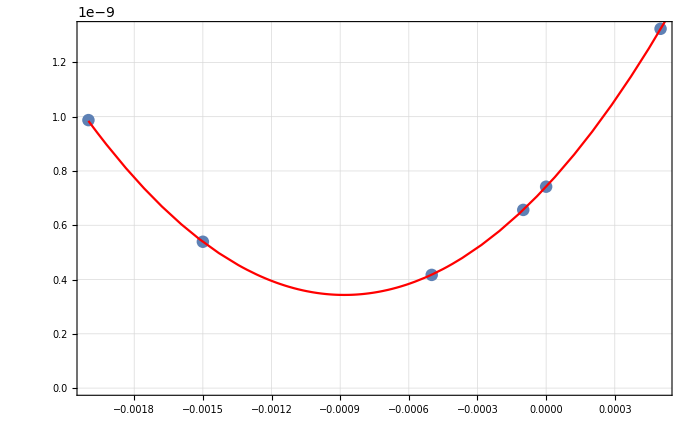
{b0 =  | -0.000881871
FittedModel[3.43235×10^-10+0.000512903 (0.000881871+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000881871 | 8.94259×10^-7 | -986.147 | 2.29955×10^-9
scale | 0.000512903 | 1.37088×10^-6 | 374.142 | 4.21065×10^-8
yoffset | 3.43235×10^-10 | 1.36382×10^-12 | 251.671 | 1.3834×10^-7 | ,-Graphics-}

```mathematica
Bramp150Fit=Chi2FitandPlot[BRamp150Data[[All,2]],BRamp150bvary[[All,2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

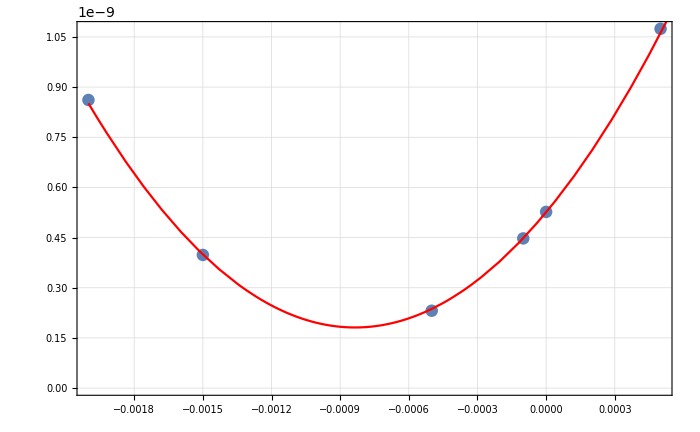
{b0 =  | -0.000835152
FittedModel[1.81297×10^-10+0.0004939 (0.000835152+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000835152 | 4.69979×10^-6 | -177.7 | 3.9297×10^-7
scale | 0.0004939 | 7.12723×10^-6 | 69.2976 | 6.62201×10^-6
yoffset | 1.81297×10^-10 | 7.08807×10^-12 | 25.5778 | 0.000131069 | ,-Graphics-}

```mathematica
Bramp300Fit=Chi2FitandPlot[BRamp300Data[[All,2]],BRamp300bvary[[All,2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

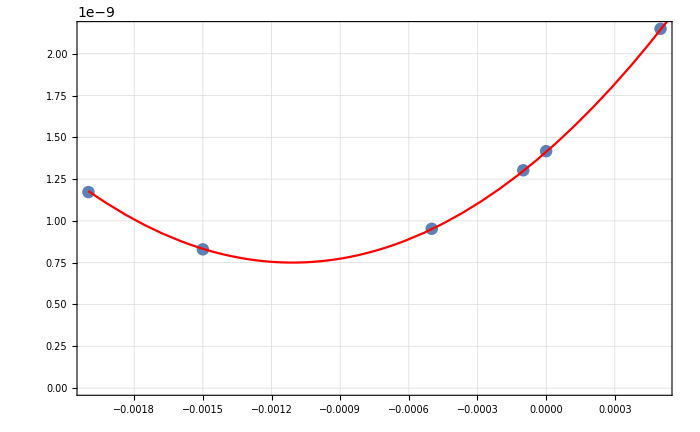
{b0 =  | -0.00110856
FittedModel[7.50783×10^-10+0.00053827 (0.00110856+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00110856 | 3.97948×10^-6 | -278.568 | 1.02014×10^-7
scale | 0.00053827 | 4.76103×10^-6 | 113.057 | 1.52564×10^-6
yoffset | 7.50783×10^-10 | 4.58771×10^-12 | 163.651 | 5.03103×10^-7 | ,-Graphics-}

```mathematica
Bramp400Fit=Chi2FitandPlot[BRamp400Data[[All,2]],BRamp400bvary[[All,2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

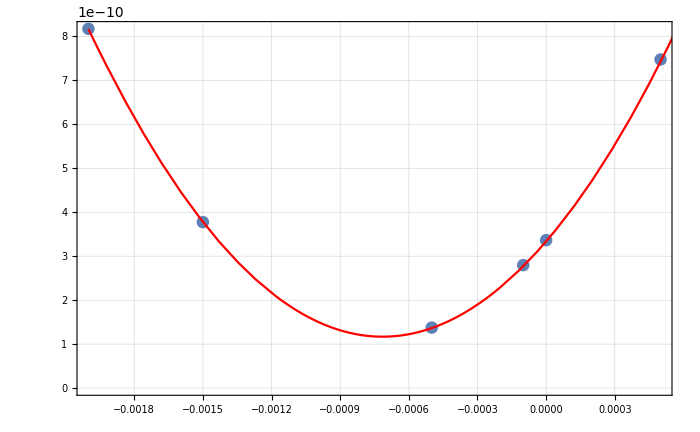
{b0 =  | -0.000714811
FittedModel[1.16962×10^-10+0.000423718 (0.000714811+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000714811 | 2.15398×10^-6 | -331.856 | 6.03405×10^-8
scale | 0.000423718 | 2.73885×10^-6 | 154.707 | 5.95497×10^-7
yoffset | 1.16962×10^-10 | 2.68836×10^-12 | 43.5067 | 0.0000267287 | ,-Graphics-}

```mathematica
Bramp600Fit=Chi2FitandPlot[BRamp600Data[[All,2]],BRamp600bvary[[All,2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

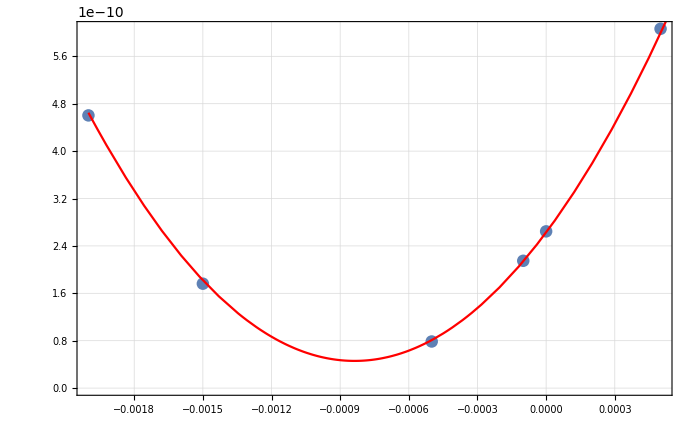
{b0 =  | -0.000836812
FittedModel[4.59008×10^-11+0.000309602 (0.000836812+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000836812 | 4.75412×10^-6 | -176.018 | 4.04342×10^-7
scale | 0.000309602 | 4.51652×10^-6 | 68.5489 | 6.84128×10^-6
yoffset | 4.59008×10^-11 | 4.49196×10^-12 | 10.2184 | 0.00199776 | ,-Graphics-}

```mathematica
Bramp800Fit=Chi2FitandPlot[BRamp800Data[[All,2]],BRamp800bvary[[All,2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

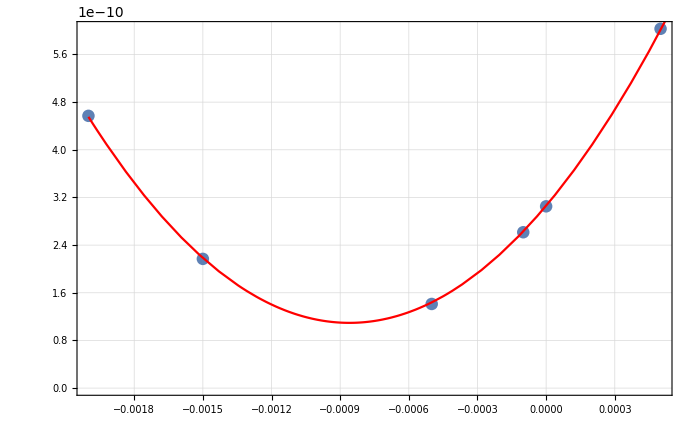
{b0 =  | -0.00085971
FittedModel[1.09497×10^-10+0.000265943 (0.00085971+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00085971 | 2.26822×10^-6 | -379.024 | 4.05005×10^-8
scale | 0.000265943 | 1.83034×10^-6 | 145.297 | 7.18832×10^-7
yoffset | 1.09497×10^-10 | 1.82121×10^-12 | 60.1235 | 0.0000101369 | ,-Graphics-}

```mathematica
Bramp1000Fit=Chi2FitandPlot[BRamp1000Data[[All,2]],BRamp1000bvary[[All,2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

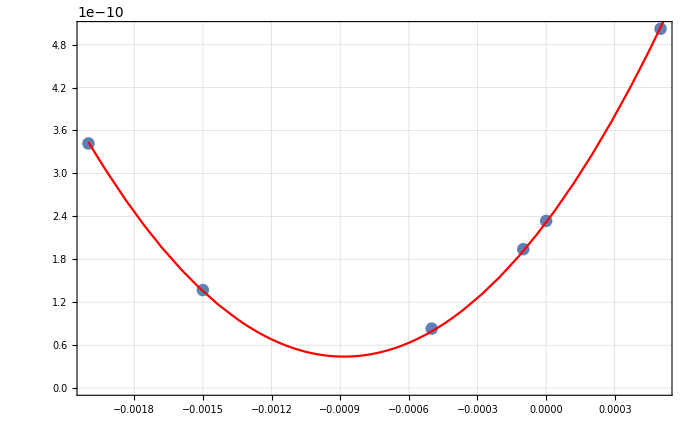
{b0 =  | -0.000883088
FittedModel[4.40163×10^-11+0.00024038 (0.000883088+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000883088 | 3.46917×10^-6 | -254.553 | 1.33693×10^-7
scale | 0.00024038 | 2.49008×10^-6 | 96.5349 | 2.45047×10^-6
yoffset | 4.40163×10^-11 | 2.47721×10^-12 | 17.7685 | 0.000388677 | ,-Graphics-}

```mathematica
Bramp1200Fit=Chi2FitandPlot[BRamp1200Data[[All,2]],BRamp1200bvary[[All,2]],bvary]
```

```mathematica
Bramp400Fit[[1,1,1,2]]
```

-0.00110856

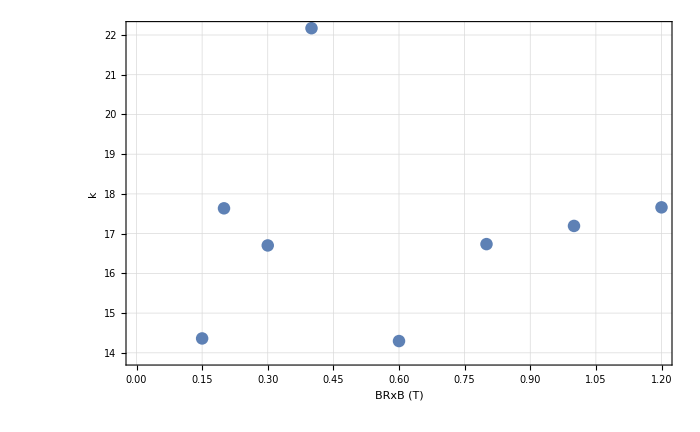

```mathematica
ListPlot[Transpose[{Join[{0.15,0.2,0.3},BRxBList[[1;;5]]],-#[[1,1,1,2]]/(5*10^-5)&/@{test,Bramp150Fit,Bramp300Fit,Bramp400Fit,Bramp600Fit,Bramp800Fit,Bramp1000Fit,Bramp1200Fit}}],FrameLabel->{{"k",None},{"BRxB (T)","Fierz term sensitivity on ΔBRxB for different BRxB"}}]
```

```mathematica
?fReduced
```

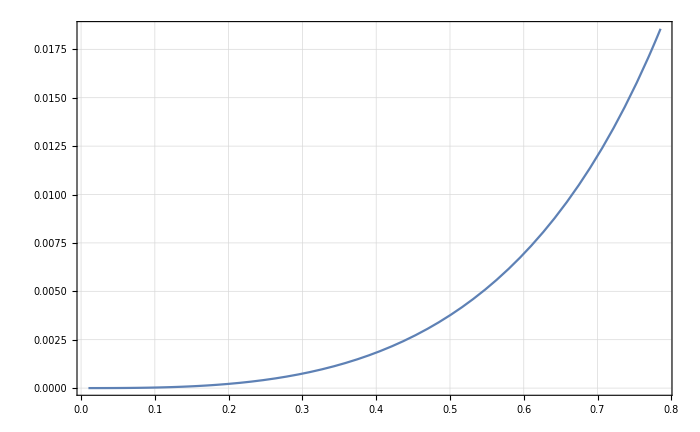

```mathematica
Plot[-fReduced[th0-1.5/180*Pi,1.]+fReduced[th0+1.5/180*Pi,1.],{th0,0.01,Pi/4}]
```

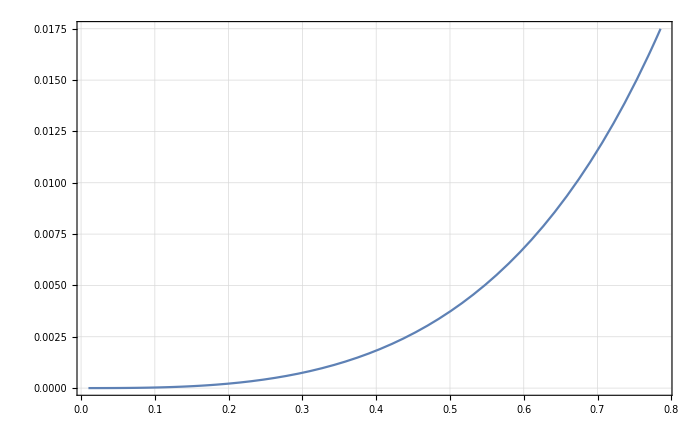

```mathematica
Plot[(-fReduced[th0-1.5/180*Pi,1.]+fReduced[th0+1.5/180*Pi,1.])/fReduced[th0,1.],{th0,0.01,Pi/4}]
```

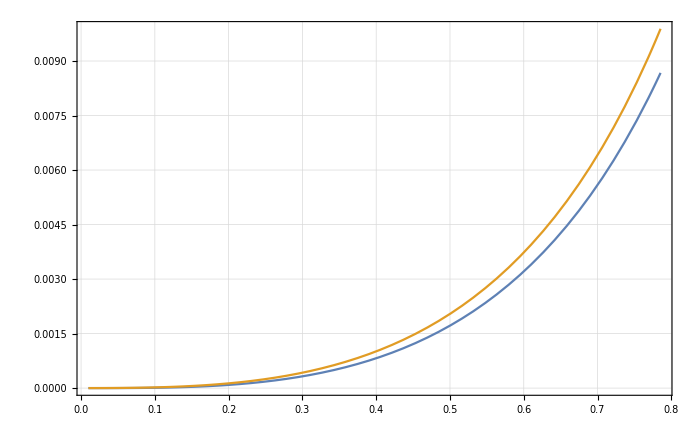

```mathematica
Plot[{-(fReduced[th0-1.5/180*Pi,1.]-fReduced[th0,1.]),fReduced[th0+1.5/180*Pi,1.]-fReduced[th0,1.]},{th0,0.01,Pi/4}]
```

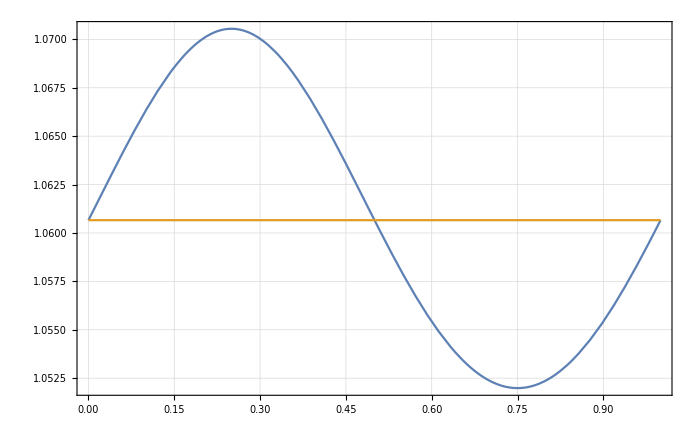

```mathematica
Plot[{fReduced[Pi/4+1.5/180*Pi*Sin[w*2Pi],1.],fReduced[Pi/4,1.]},{w,0,1}]
```

```mathematica
NIntegrate[fReduced[Pi/4+1.5/180*Pi*Sin[w*2Pi],1.],{w,0,1}(*,Assumptions->{0.<th0<Pi/4&&0.<th1<2/180*Pi}*)]/NIntegrate[fReduced[Pi/4,1.],{w,0,1}]
```

1.00029

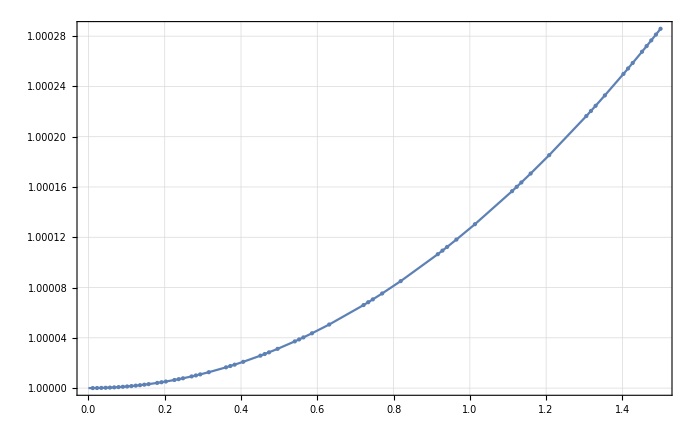

```mathematica
Plot[
NIntegrate[fReduced[Pi/4+th1/180*Pi*Sin[w*2Pi],1.],{w,0,1}(*,Assumptions->{0.<th0<Pi/4&&0.<th1<2/180*Pi}*)]/NIntegrate[fReduced[Pi/4,1.],{w,0,1}],{th1,0,1.5},PlotPoints->3,Mesh->All]
```

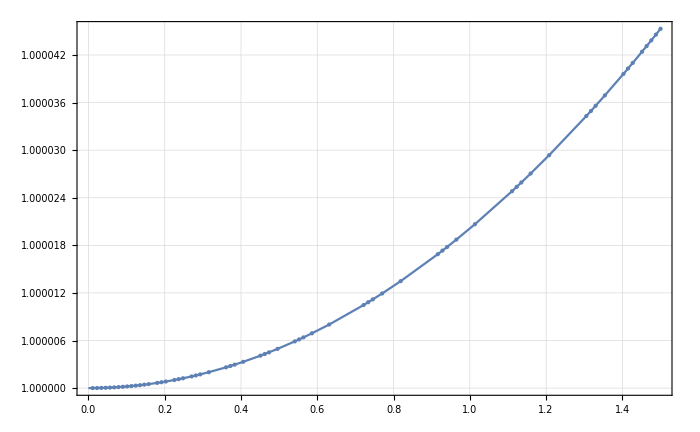

```mathematica
Plot[
NIntegrate[fReduced[Pi/8+th1/180*Pi*Sin[w*2Pi],1.],{w,0,1}(*,Assumptions->{0.<th0<Pi/4&&0.<th1<2/180*Pi}*)]/NIntegrate[fReduced[Pi/8,1.],{w,0,1}],{th1,0,1.5},PlotPoints->3,Mesh->All]
```

### for non-full gyration, e.g. only half, difference is more (for that one part of gyration of path through RxB)

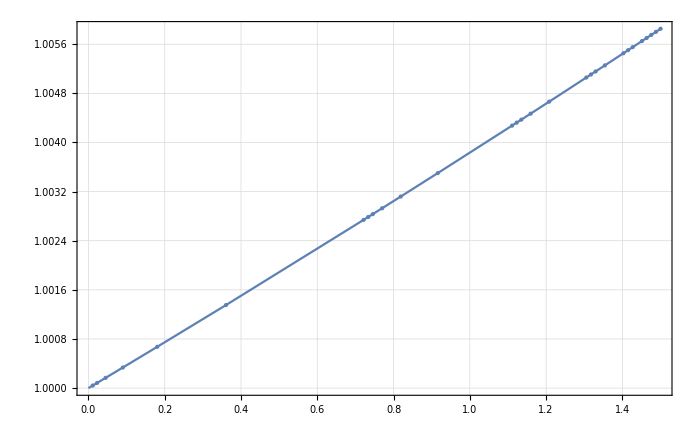

```mathematica
Plot[
NIntegrate[fReduced[Pi/4+th1/180*Pi*Sin[w*2Pi],1.],{w,0,0.5}(*,Assumptions->{0.<th0<Pi/4&&0.<th1<2/180*Pi}*)]/NIntegrate[fReduced[Pi/4,1.],{w,0,0.5}],{th1,0,1.5},PlotPoints->3,Mesh->All]
```

## WITH PXLIMITS: BRxB ramp sensitivity of 0.15,0.3,0.4,0.8,1,1.2 T

```mathematica
BRxBList={0.15,0.2,0.3,0.4,0.6,0.8,1.,1.2};
```

```mathematica
RoughDriftDistance=Round[Table[D1stBPolyGrad[pmax,Pi,Pi/4,BRxB,1,0.,1,1,1]+2rG[pmax,Pi/4,BRxB]+0.01,{BRxB,BRxBList}],0.01]*0.8
```

{0.112,0.08,0.056,0.048,0.032,0.024,0.024,0.024}

### lets do with XOff now, maybe that was the difference, but first one test without, so that we can check compare with without pXLimits

```mathematica
XYDataBRampWpXLimits=Table[XYDataCreation[{-0.005,xmax,0.,9},{-0.02,0.02,0.,5}],{xmax,RoughDriftDistance}];
```

```mathematica
bvary={-0.002,-0.0015,-0.001,-0.0005,0.};
```

```mathematica
TransferData[b_?NumericQ,XYData_List,{alpha_?NumericQ,BRxB_?NumericQ,rF_?NumericQ,rA_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,R_?NumericQ,G1_?NumericQ,G2_?NumericQ},{twx_?NumericQ,plx_?NumericQ,k1x_?NumericQ,k2x_?NumericQ,k3x_?NumericQ,twy_?NumericQ,ply_?NumericQ,k1y_?NumericQ,k2y_?NumericQ,k3y_?NumericQ},{xAA_?NumericQ,yAA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ},IntPrec_]:=Module[
{t0=AbsoluteTime[],t1,result},
Print[DateString[]];
result=Table[
{
bin,
FitFuncBinwNbeam[bin,b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec]
},
{bin,1,Length[XYData]}];
t1=AbsoluteTime[];
Print["data time= ",(t1-t0)/3600.];
result
]
```

```mathematica
ManualbvaryData[bList_List,XYData_List,{alpha_?NumericQ,BRxB_?NumericQ,rF_?NumericQ,rA_?NumericQ,rRxB_?NumericQ,rD_?NumericQ,R_?NumericQ,G1_?NumericQ,G2_?NumericQ},{twx_?NumericQ,plx_?NumericQ,k1x_?NumericQ,k2x_?NumericQ,k3x_?NumericQ,twy_?NumericQ,ply_?NumericQ,k1y_?NumericQ,k2y_?NumericQ,k3y_?NumericQ},{xAA_?NumericQ,yAA_?NumericQ,xOff_?NumericQ,yOff_?NumericQ},IntPrec_]:=Module[
{t0=AbsoluteTime[],result,t1},
Print[DateString[]];
result=Table[
{
b,
Table[
{
bin,
FitFuncBinwNbeam[bin,b,XYData,{alpha,BRxB,rF,rA,rRxB,rD,R,G1,G2},{twx,plx,k1x,k2x,k3x,twy,ply,k1y,k2y,k3y},{xAA,yAA,xOff,yOff},IntPrec]
},
{bin,1,Length[XYData]}]
},
{b,bList}];
t1=AbsoluteTime[];
Print["bvary time= ",(t1-t0)/3600.];
result
]
```

```mathematica
CloseKernels[]
```

{}

```mathematica
LaunchKernels[]
```

{KernelObject[1,193.170.93.100],KernelObject[2,193.170.93.100],KernelObject[3,193.170.93.100],KernelObject[4,193.170.93.100],KernelObject[5,193.170.93.100],KernelObject[6,local],KernelObject[7,local],KernelObject[8,local],KernelObject[9,local]}

```mathematica
BRxBList
```

{0.15,0.2,0.3,0.4,0.6,0.8,1.,1.2}

### without offset

```mathematica
BRamp200DataWpXLimits=TransferData[0.,XYDataBRampWpXLimits[[2]],{Pi//N,BRxBList[[2]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Sat 14 Mar 2020 11:27:05

data time= 9.09913

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000575064},{7,0.0106823},{8,0.0103616},{9,0.0100717},{10,0.00045571},{11,0.0105521},{12,0.0536305},{13,0.0525703},{14,0.0508332},{15,0.00929335},{16,0.0236722},{17,0.0825324},{18,0.0871623},{19,0.0809984},{20,0.0221871},{21,0.0243277},{22,0.071754},{23,0.0813934},{24,0.0725208},{25,0.0244976},{26,0.0145486},{27,0.0389909},{28,0.0459423},{29,0.0410804},{30,0.0157278},{31,0.00519262},{32,0.0120543},{33,0.0150241},{34,0.0135678},{35,0.0061855},{36,0.00108328},{37,0.00230235},{38,0.00300201},{39,0.00265942},{40,0.00142034},{41,0.000101122},{42,0.000241227},{43,0.000330326},{44,0.000309186},{45,0.000164855}}

```mathematica
ListPlot3D[Transpose[{XYDataBRampWpXLimits[[2,All,1]],XYDataBRampWpXLimits[[2,All,2]],BRamp200DataWpXLimits[[All,2]]}]]
```

-Graphics3D-

```mathematica
BRamp200bvaryWpXLimits=ManualbvaryData[bvary,XYDataBRampWpXLimits[[2]],{Pi//N,BRxBList[[2]]+BRxBList[[2]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Sat 14 Mar 2020 20:33:02

LinkObject::linkd: Unable to communicate with closed link LinkObject[38861@193.170.93.100,36017@193.170.93.100,630,11].

Kernels::rdead: Subkernel connected through KernelObject[3,193.170.93.100] appears dead.

LightweightGridClient`RemoteKernelClose::lwgconnect: Unable to connect to http://193.170.93.100:3737/WolframRemoteServices.  Check network connectivity and the spelling of the hostname or URL of the remote computer. Confirm that a Lightweight Grid Manager is running on the remote computer.

LinkObject::linkd: Unable to communicate with closed link LinkObject[46493@193.170.93.100,46553@193.170.93.100,632,13].

Kernels::rdead: Subkernel connected through KernelObject[5,193.170.93.100] appears dead.

LightweightGridClient`RemoteKernelClose::lwgconnect: Unable to connect to http://193.170.93.100:3737/WolframRemoteServices.  Check network connectivity and the spelling of the hostname or URL of the remote computer. Confirm that a Lightweight Grid Manager is running on the remote computer.

LinkObject::linkd: Unable to communicate with closed link LinkObject[46615@193.170.93.100,42437@193.170.93.100,628,9].

General::stop: Further output of LinkObject::linkd will be suppressed during this calculation.

Kernels::rdead: Subkernel connected through KernelObject[1,193.170.93.100] appears dead.

General::stop: Further output of Kernels::rdead will be suppressed during this calculation.

$Aborted

```mathematica
BRamp400Data=TransferData[0.,XYDataBRamp[[1]],{Pi//N,BRxBList[[1]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Tue 3 Mar 2020 18:11:56

data time= 0.865502

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.0000511965},{7,0.0124413},{8,0.0120707},{9,0.0116761},{10,0.0000263197},{11,0.00559889},{12,0.0684651},{13,0.0668136},{14,0.0652835},{15,0.00475104},{16,0.0171829},{17,0.108626},{18,0.108039},{19,0.106826},{20,0.0161224},{21,0.0161304},{22,0.0789523},{23,0.0811808},{24,0.080979},{25,0.0166427},{26,0.00675845},{27,0.0277982},{28,0.0301347},{29,0.0303852},{30,0.00772842},{31,0.00130416},{32,0.00452035},{33,0.00512874},{34,0.00528239},{35,0.0017024},{36,0.0000871782},{37,0.000331804},{38,0.000393749},{39,0.000432386},{40,0.000143331},{41,2.27855×10^-7},{42,1.74757×10^-6},{43,2.64237×10^-6},{44,3.83447×10^-6},{45,1.12086×10^-6}}

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[1,All,1]],XYDataBRamp[[1,All,2]],BRamp400Data[[All,2]]}]]
```

-Graphics3D-

```mathematica
BRamp400bvary=ManualbvaryData[bvary,XYDataBRamp[[1]],{Pi//N,BRxBList[[1]]+BRxBList[[1]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Tue 3 Mar 2020 19:03:52

bvary time= 4.82933

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.0000511783},{7,0.012436},{8,0.0120656},{9,0.011697},{10,0.0000263124},{11,0.00559843},{12,0.0684527},{13,0.0668005},{14,0.065271},{15,0.00475064},{16,0.0171838},{17,0.108628},{18,0.108041},{19,0.106826},{20,0.016123},{21,0.0161324},{22,0.0789612},{23,0.0811893},{24,0.0809808},{25,0.0166445},{26,0.00675884},{27,0.0277946},{28,0.0301366},{29,0.0303877},{30,0.00772892},{31,0.00130401},{32,0.00451985},{33,0.00512823},{34,0.00528217},{35,0.00170227},{36,0.0000871257},{37,0.000331658},{38,0.000393509},{39,0.000432221},{40,0.000143258},{41,2.27546×10^-7},{42,1.7429×10^-6},{43,2.63747×10^-6},{44,3.82573×10^-6},{45,1.1183×10^-6}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.0000511841},{7,0.0124377},{8,0.0120672},{9,0.0116986},{10,0.0000263154},{11,0.00559866},{12,0.0684576},{13,0.0668053},{14,0.0652758},{15,0.00475086},{16,0.0171837},{17,0.108628},{18,0.108042},{19,0.106827},{20,0.0161229},{21,0.0161316},{22,0.0789577},{23,0.0811857},{24,0.0809773},{25,0.0166437},{26,0.00675832},{27,0.0277925},{28,0.0301343},{29,0.0303854},{30,0.00772834},{31,0.00130389},{32,0.00451943},{33,0.00512775},{34,0.00528168},{35,0.00170211},{36,0.0000871162},{37,0.000331622},{38,0.000393466},{39,0.000432175},{40,0.000143243},{41,2.27519×10^-7},{42,1.74269×10^-6},{43,2.63715×10^-6},{44,3.82527×10^-6},{45,1.11816×10^-6}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.0000512001},{7,0.0124425},{8,0.0120719},{9,0.0117032},{10,0.000026324},{11,0.00559931},{12,0.0684712},{13,0.0668189},{14,0.0652893},{15,0.00475148},{16,0.0171833},{17,0.10863},{18,0.108044},{19,0.106829},{20,0.0161227},{21,0.0161294},{22,0.0789478},{23,0.0811757},{24,0.0809676},{25,0.0166416},{26,0.00675686},{27,0.0277865},{28,0.030128},{29,0.030379},{30,0.00772672},{31,0.00130354},{32,0.00451825},{33,0.00512641},{34,0.0052803},{35,0.00170166},{36,0.0000870894},{37,0.000331522},{38,0.000393348},{39,0.000432046},{40,0.000143199},{41,2.27441×10^-7},{42,1.74209×10^-6},{43,2.63626×10^-6},{44,3.82399×10^-6},{45,1.11779×10^-6}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.0000511955},{7,0.0124411},{8,0.0120706},{9,0.0117019},{10,0.0000263216},{11,0.00559912},{12,0.0684673},{13,0.066815},{14,0.0652854},{15,0.00475131},{16,0.0171834},{17,0.108629},{18,0.108043},{19,0.106829},{20,0.0161228},{21,0.01613},{22,0.0789506},{23,0.0811786},{24,0.0809704},{25,0.0166422},{26,0.00675728},{27,0.0277882},{28,0.0301298},{29,0.0303809},{30,0.00772718},{31,0.00130364},{32,0.00451858},{33,0.00512679},{34,0.0052807},{35,0.00170179},{36,0.0000870971},{37,0.00033155},{38,0.000393382},{39,0.000432083},{40,0.000143212},{41,2.27463×10^-7},{42,1.74226×10^-6},{43,2.63652×10^-6},{44,3.82435×10^-6},{45,1.11789×10^-6}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.0000512013},{7,0.0124428},{8,0.0120722},{9,0.0117035},{10,0.0000263246},{11,0.00559935},{12,0.0684721},{13,0.0668198},{14,0.0652902},{15,0.00475153},{16,0.0171833},{17,0.10863},{18,0.108044},{19,0.106829},{20,0.0161227},{21,0.0161292},{22,0.0789471},{23,0.081175},{24,0.0809669},{25,0.0166414},{26,0.00675676},{27,0.0277861},{28,0.0301275},{29,0.0303786},{30,0.00772661},{31,0.00130352},{32,0.00451816},{33,0.00512631},{34,0.00528021},{35,0.00170163},{36,0.0000870875},{37,0.000331515},{38,0.000393339},{39,0.000432037},{40,0.000143196},{41,2.27435×10^-7},{42,1.74205×10^-6},{43,2.6362×10^-6},{44,3.82389×10^-6},{45,1.11776×10^-6}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000051207},{7,0.0124445},{8,0.0120739},{9,0.0117051},{10,0.0000263277},{11,0.00559958},{12,0.068477},{13,0.0668246},{14,0.065295},{15,0.00475175},{16,0.0171831},{17,0.10863},{18,0.108044},{19,0.10683},{20,0.0161226},{21,0.0161284},{22,0.0789435},{23,0.0811714},{24,0.0809635},{25,0.0166407},{26,0.00675624},{27,0.027784},{28,0.0301252},{29,0.0303763},{30,0.00772603},{31,0.00130339},{32,0.00451774},{33,0.00512583},{34,0.00527972},{35,0.00170147},{36,0.000087078},{37,0.000331479},{38,0.000393297},{39,0.000431991},{40,0.000143181},{41,2.27407×10^-7},{42,1.74184×10^-6},{43,2.63588×10^-6},{44,3.82344×10^-6},{45,1.11762×10^-6}}}}

```mathematica
BRamp600Data=TransferData[0.,XYDataBRamp[[2]],{Pi//N,BRxBList[[2]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Tue 3 Mar 2020 23:53:38

data time= 0.834876

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0102228},{8,0.00991901},{9,0.00964363},{10,0.},{11,0.00154451},{12,0.0559948},{13,0.0547798},{14,0.053576},{15,0.00121048},{16,0.00728646},{17,0.104553},{18,0.103388},{19,0.102212},{20,0.00664081},{21,0.0104589},{22,0.0925354},{23,0.0931434},{24,0.0936755},{25,0.0103739},{26,0.00617093},{27,0.0418799},{28,0.0432752},{29,0.0446322},{30,0.00676905},{31,0.00163037},{32,0.00906863},{33,0.00967968},{34,0.010341},{35,0.00201333},{36,0.000166274},{37,0.000868396},{38,0.000962661},{39,0.00106089},{40,0.000246946},{41,2.09622×10^-6},{42,0.0000177566},{43,0.0000225568},{44,0.0000285247},{45,5.53744×10^-6}}

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[2,All,1]],XYDataBRamp[[2,All,2]],BRamp600Data[[All,2]]}]]
```

-Graphics3D-

```mathematica
BRamp600bvary=ManualbvaryData[bvary,XYDataBRamp[[2]],{Pi//N,BRxBList[[2]]+BRxBList[[2]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 00:43:43

bvary time= 4.97329

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0102198},{8,0.00991376},{9,0.00963989},{10,0.},{11,0.00154448},{12,0.0559855},{13,0.0547707},{14,0.0535664},{15,0.00121044},{16,0.00728702},{17,0.104551},{18,0.103386},{19,0.102205},{20,0.0066414},{21,0.0104601},{22,0.0925441},{23,0.0931517},{24,0.0936842},{25,0.010375},{26,0.00617149},{27,0.041884},{28,0.0432796},{29,0.0446458},{30,0.0067697},{31,0.0016303},{32,0.00906798},{33,0.00967924},{34,0.0103409},{35,0.00201338},{36,0.000166263},{37,0.000868212},{38,0.000962471},{39,0.00106065},{40,0.000246883},{41,2.09281×10^-6},{42,0.0000177336},{43,0.0000225354},{44,0.0000284839},{45,5.53485×10^-6}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0102212},{8,0.0099151},{9,0.00964119},{10,0.},{11,0.00154451},{12,0.0559893},{13,0.0547745},{14,0.0535702},{15,0.00121047},{16,0.00728688},{17,0.104553},{18,0.103388},{19,0.102207},{20,0.00664129},{21,0.0104596},{22,0.0925414},{23,0.0931491},{24,0.0936816},{25,0.0103746},{26,0.00617106},{27,0.0418813},{28,0.0432769},{29,0.044643},{30,0.00676924},{31,0.00163015},{32,0.00906718},{33,0.0096784},{34,0.01034},{35,0.0020132},{36,0.000166245},{37,0.000868123},{38,0.000962373},{39,0.00106054},{40,0.000246858},{41,2.09256×10^-6},{42,0.0000177316},{43,0.0000225328},{44,0.0000284806},{45,5.53421×10^-6}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.010225},{8,0.00991883},{9,0.00964484},{10,0.},{11,0.0015446},{12,0.0559999},{13,0.0547851},{14,0.0535808},{15,0.00121056},{16,0.00728646},{17,0.104558},{18,0.103394},{19,0.102213},{20,0.00664098},{21,0.0104583},{22,0.0925339},{23,0.0931418},{24,0.0936745},{25,0.0103734},{26,0.00616987},{27,0.0418737},{28,0.0432692},{29,0.0446352},{30,0.00676797},{31,0.00162975},{32,0.00906497},{33,0.00967604},{34,0.0103375},{35,0.00201271},{36,0.000166197},{37,0.000867874},{38,0.000962098},{39,0.00106024},{40,0.000246787},{41,2.09186×10^-6},{42,0.0000177258},{43,0.0000225254},{44,0.0000284714},{45,5.5324×10^-6}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0102239},{8,0.00991776},{9,0.0096438},{10,0.},{11,0.00154458},{12,0.0559969},{13,0.0547821},{14,0.0535777},{15,0.00121054},{16,0.00728658},{17,0.104556},{18,0.103392},{19,0.102211},{20,0.00664106},{21,0.0104587},{22,0.0925361},{23,0.0931439},{24,0.0936765},{25,0.0103738},{26,0.00617021},{27,0.0418759},{28,0.0432714},{29,0.0446374},{30,0.00676834},{31,0.00162986},{32,0.0090656},{33,0.00967671},{34,0.0103382},{35,0.00201285},{36,0.000166211},{37,0.000867945},{38,0.000962177},{39,0.00106033},{40,0.000246807},{41,2.09206×10^-6},{42,0.0000177274},{43,0.0000225275},{44,0.000028474},{45,5.53292×10^-6}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0102253},{8,0.0099191},{9,0.0096451},{10,0.},{11,0.00154461},{12,0.0560007},{13,0.0547859},{14,0.0535815},{15,0.00121057},{16,0.00728643},{17,0.104558},{18,0.103394},{19,0.102213},{20,0.00664095},{21,0.0104582},{22,0.0925334},{23,0.0931413},{24,0.093674},{25,0.0103733},{26,0.00616978},{27,0.0418732},{28,0.0432686},{29,0.0446346},{30,0.00676788},{31,0.00162972},{32,0.00906481},{33,0.00967587},{34,0.0103373},{35,0.00201267},{36,0.000166193},{37,0.000867857},{38,0.000962079},{39,0.00106022},{40,0.000246782},{41,2.09181×10^-6},{42,0.0000177254},{43,0.0000225249},{44,0.0000284708},{45,5.53227×10^-6}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0102266},{8,0.00992043},{9,0.00964641},{10,0.},{11,0.00154464},{12,0.0560045},{13,0.0547897},{14,0.0535853},{15,0.0012106},{16,0.00728629},{17,0.10456},{18,0.103396},{19,0.102215},{20,0.00664084},{21,0.0104578},{22,0.0925307},{23,0.0931387},{24,0.0936714},{25,0.0103729},{26,0.00616935},{27,0.0418705},{28,0.0432659},{29,0.0446318},{30,0.00676743},{31,0.00162957},{32,0.00906402},{33,0.00967503},{34,0.0103364},{35,0.0020125},{36,0.000166176},{37,0.000867768},{38,0.000961981},{39,0.00106012},{40,0.000246756},{41,2.09157×10^-6},{42,0.0000177233},{43,0.0000225223},{44,0.0000284675},{45,5.53163×10^-6}}}}

```mathematica
BRamp800Data=TransferData[0.,XYDataBRamp[[3]],{Pi//N,BRxBList[[3]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 05:42:07

data time= 0.561695

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926619},{8,0.00899548},{9,0.00872213},{10,0.},{11,0.000336707},{12,0.0493727},{13,0.0482705},{14,0.0472382},{15,0.000220915},{16,0.00292363},{17,0.093558},{18,0.0926273},{19,0.0916156},{20,0.00260758},{21,0.00482249},{22,0.0973866},{23,0.0975569},{24,0.097722},{25,0.00468185},{26,0.00445104},{27,0.0557594},{28,0.0568992},{29,0.0579905},{30,0.00463639},{31,0.0017249},{32,0.016227},{33,0.0170315},{34,0.017891},{35,0.00201495},{36,0.000258224},{37,0.0019898},{38,0.00216928},{39,0.00236231},{40,0.000353859},{41,7.47975×10^-6},{42,0.0000820516},{43,0.0000971629},{44,0.000113963},{45,0.0000151419}}

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[3,All,1]],XYDataBRamp[[3,All,2]],BRamp800Data[[All,2]]}]]
```

-Graphics3D-

```mathematica
BRamp800bvary=ManualbvaryData[bvary,XYDataBRamp[[3]],{Pi//N,BRxBList[[3]]+BRxBList[[3]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 06:15:50

bvary time= 3.31177

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926266},{8,0.00899202},{9,0.00871869},{10,0.},{11,0.000336728},{12,0.0493658},{13,0.0482629},{14,0.0472308},{15,0.000220921},{16,0.002924},{17,0.0935553},{18,0.0926244},{19,0.0916124},{20,0.0026079},{21,0.00482311},{22,0.0973916},{23,0.0975615},{24,0.0977268},{25,0.00468239},{26,0.00445146},{27,0.0557656},{28,0.0569081},{29,0.0579968},{30,0.00463683},{31,0.00172492},{32,0.0162278},{33,0.017032},{34,0.0178937},{35,0.002015},{36,0.000258139},{37,0.00198925},{38,0.00216902},{39,0.00236202},{40,0.000353794},{41,7.47315×10^-6},{42,0.0000819996},{43,0.0000970664},{44,0.000113889},{45,0.0000151289}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926386},{8,0.0089932},{9,0.00871984},{10,0.},{11,0.000336728},{12,0.0493688},{13,0.048266},{14,0.0472339},{15,0.000220923},{16,0.00292389},{17,0.0935572},{18,0.0926263},{19,0.0916144},{20,0.00260781},{21,0.00482285},{22,0.0973903},{23,0.0975603},{24,0.0977256},{25,0.00468215},{26,0.00445117},{27,0.0557628},{28,0.0569053},{29,0.057994},{30,0.00463654},{31,0.00172477},{32,0.0162266},{33,0.0170306},{34,0.0178923},{35,0.00201483},{36,0.000258113},{37,0.00198906},{38,0.00216881},{39,0.00236179},{40,0.000353758},{41,7.47228×10^-6},{42,0.0000819904},{43,0.0000970555},{44,0.000113877},{45,0.0000151272}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926723},{8,0.00899649},{9,0.00872306},{10,0.},{11,0.00033673},{12,0.0493774},{13,0.0482745},{14,0.0472425},{15,0.000220927},{16,0.00292358},{17,0.0935625},{18,0.0926318},{19,0.09162},{20,0.00260755},{21,0.00482214},{22,0.0973866},{23,0.0975568},{24,0.0977223},{25,0.00468147},{26,0.00445037},{27,0.0557549},{28,0.0568974},{29,0.057986},{30,0.00463573},{31,0.00172436},{32,0.0162229},{33,0.0170269},{34,0.0178884},{35,0.00201437},{36,0.00025804},{37,0.00198852},{38,0.00216822},{39,0.00236115},{40,0.00035366},{41,7.46987×10^-6},{42,0.0000819646},{43,0.0000970252},{44,0.000113841},{45,0.0000151224}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926627},{8,0.00899555},{9,0.00872214},{10,0.},{11,0.000336729},{12,0.049375},{13,0.0482721},{14,0.04724},{15,0.000220926},{16,0.00292367},{17,0.093561},{18,0.0926302},{19,0.0916184},{20,0.00260762},{21,0.00482234},{22,0.0973877},{23,0.0975578},{24,0.0977233},{25,0.00468167},{26,0.0044506},{27,0.0557572},{28,0.0568996},{29,0.0579883},{30,0.00463596},{31,0.00172448},{32,0.016224},{33,0.0170279},{34,0.0178895},{35,0.0020145},{36,0.000258061},{37,0.00198867},{38,0.00216839},{39,0.00236134},{40,0.000353688},{41,7.47056×10^-6},{42,0.000081972},{43,0.0000970339},{44,0.000113851},{45,0.0000151238}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926747},{8,0.00899673},{9,0.00872329},{10,0.},{11,0.00033673},{12,0.049378},{13,0.0482752},{14,0.0472431},{15,0.000220928},{16,0.00292356},{17,0.0935629},{18,0.0926322},{19,0.0916204},{20,0.00260753},{21,0.00482209},{22,0.0973864},{23,0.0975566},{24,0.0977221},{25,0.00468142},{26,0.00445031},{27,0.0557544},{28,0.0568968},{29,0.0579854},{30,0.00463567},{31,0.00172434},{32,0.0162227},{33,0.0170266},{34,0.0178881},{35,0.00201434},{36,0.000258035},{37,0.00198848},{38,0.00216818},{39,0.00236111},{40,0.000353653},{41,7.46969×10^-6},{42,0.0000819628},{43,0.0000970231},{44,0.000113839},{45,0.0000151221}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.00926867},{8,0.0089979},{9,0.00872443},{10,0.},{11,0.00033673},{12,0.0493811},{13,0.0482782},{14,0.0472462},{15,0.000220929},{16,0.00292344},{17,0.0935648},{18,0.0926341},{19,0.0916224},{20,0.00260744},{21,0.00482183},{22,0.0973851},{23,0.0975553},{24,0.0977209},{25,0.00468118},{26,0.00445003},{27,0.0557516},{28,0.056894},{29,0.0579826},{30,0.00463538},{31,0.00172419},{32,0.0162214},{33,0.0170252},{34,0.0178867},{35,0.00201417},{36,0.000258009},{37,0.00198828},{38,0.00216797},{39,0.00236088},{40,0.000353618},{41,7.46883×10^-6},{42,0.0000819536},{43,0.0000970122},{44,0.000113826},{45,0.0000151203}}}}

```mathematica
BRamp1000Data=TransferData[0.,XYDataBRamp[[4]],{Pi//N,BRxBList[[4]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 09:34:32

data time= 0.534377

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0168498},{8,0.0163779},{9,0.0159069},{10,0.},{11,0.000373247},{12,0.0748076},{13,0.0735993},{14,0.0724306},{15,0.000253891},{16,0.00206301},{17,0.112443},{18,0.111944},{19,0.111491},{20,0.00194381},{21,0.00251975},{22,0.0902163},{23,0.0909644},{24,0.0915779},{25,0.00250945},{26,0.00172649},{27,0.031183},{28,0.0322811},{29,0.0333906},{30,0.00189385},{31,0.000252266},{32,0.0031955},{33,0.00346633},{34,0.00376278},{35,0.000336321},{36,2.73915×10^-6},{37,0.0000637467},{38,0.0000760835},{39,0.0000906288},{40,6.24695×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[4,All,1]],XYDataBRamp[[4,All,2]],BRamp1000Data[[All,2]]}]]
```

-Graphics3D-

```mathematica
BRamp1000bvary=ManualbvaryData[bvary,XYDataBRamp[[4]],{Pi//N,BRxBList[[4]]+BRxBList[[4]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 10:06:36

bvary time= 3.96704

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0168444},{8,0.0163726},{9,0.0159019},{10,0.},{11,0.000373315},{12,0.0747973},{13,0.0735937},{14,0.0724304},{15,0.000253949},{16,0.00206329},{17,0.112443},{18,0.111943},{19,0.11149},{20,0.00194409},{21,0.00251999},{22,0.0902216},{23,0.0909701},{24,0.0915841},{25,0.00250969},{26,0.00172657},{27,0.0311853},{28,0.0322843},{29,0.0334014},{30,0.00189487},{31,0.00025222},{32,0.00319537},{33,0.00346584},{34,0.00376249},{35,0.000336269},{36,2.73832×10^-6},{37,0.0000637012},{38,0.0000760296},{39,0.0000905673},{40,6.24041×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0168462},{8,0.0163744},{9,0.0159037},{10,0.},{11,0.0003733},{12,0.0748},{13,0.0735965},{14,0.0724333},{15,0.000253941},{16,0.00206315},{17,0.112443},{18,0.111944},{19,0.111491},{20,0.00194397},{21,0.00251981},{22,0.0902192},{23,0.0909677},{24,0.0915817},{25,0.00250952},{26,0.00172643},{27,0.0311832},{28,0.0322821},{29,0.0333991},{30,0.00189472},{31,0.000252195},{32,0.00319506},{33,0.00346552},{34,0.00376214},{35,0.000336235},{36,2.73799×10^-6},{37,0.0000636939},{38,0.000076021},{39,0.000090557},{40,6.23968×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0168515},{8,0.0163795},{9,0.0159088},{10,0.},{11,0.000373259},{12,0.0748077},{13,0.0736043},{14,0.0724412},{15,0.000253916},{16,0.00206278},{17,0.112445},{18,0.111946},{19,0.111493},{20,0.00194362},{21,0.00251932},{22,0.0902123},{23,0.0909609},{24,0.091575},{25,0.00250903},{26,0.00172604},{27,0.0311772},{28,0.032276},{29,0.0333928},{30,0.0018943},{31,0.000252124},{32,0.00319422},{33,0.0034646},{34,0.00376115},{35,0.000336142},{36,2.73708×10^-6},{37,0.0000636736},{38,0.0000759969},{39,0.0000905285},{40,6.23765×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.01685},{8,0.0163781},{9,0.0159073},{10,0.},{11,0.000373271},{12,0.0748055},{13,0.0736021},{14,0.0724389},{15,0.000253923},{16,0.00206289},{17,0.112444},{18,0.111945},{19,0.111492},{20,0.00194372},{21,0.00251946},{22,0.0902143},{23,0.0909629},{24,0.0915769},{25,0.00250917},{26,0.00172616},{27,0.0311789},{28,0.0322777},{29,0.0333946},{30,0.00189442},{31,0.000252144},{32,0.00319446},{33,0.00346486},{34,0.00376143},{35,0.000336169},{36,2.73734×10^-6},{37,0.0000636794},{38,0.0000760037},{39,0.0000905366},{40,6.23823×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0168519},{8,0.0163799},{9,0.0159091},{10,0.},{11,0.000373256},{12,0.0748083},{13,0.0736049},{14,0.0724417},{15,0.000253914},{16,0.00206275},{17,0.112445},{18,0.111946},{19,0.111493},{20,0.0019436},{21,0.00251928},{22,0.0902118},{23,0.0909605},{24,0.0915745},{25,0.00250899},{26,0.00172602},{27,0.0311767},{28,0.0322755},{29,0.0333924},{30,0.00189427},{31,0.000252118},{32,0.00319416},{33,0.00346453},{34,0.00376108},{35,0.000336135},{36,2.73702×10^-6},{37,0.0000636722},{38,0.0000759951},{39,0.0000905264},{40,6.2375×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0168537},{8,0.0163817},{9,0.0159109},{10,0.},{11,0.000373242},{12,0.074811},{13,0.0736077},{14,0.0724446},{15,0.000253906},{16,0.00206262},{17,0.112446},{18,0.111946},{19,0.111494},{20,0.00194348},{21,0.00251911},{22,0.0902094},{23,0.090958},{24,0.0915722},{25,0.00250882},{26,0.00172588},{27,0.0311746},{28,0.0322733},{29,0.0333901},{30,0.00189412},{31,0.000252093},{32,0.00319385},{33,0.00346421},{34,0.00376072},{35,0.000336102},{36,2.7367×10^-6},{37,0.000063665},{38,0.0000759865},{39,0.0000905162},{40,6.23677×10^-6},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}}}

```mathematica
BRamp1200Data=TransferData[0.,XYDataBRamp[[5]],{Pi//N,BRxBList[[5]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 16:10:07

data time= 0.44613

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0266815},{8,0.0259732},{9,0.0252988},{10,0.},{11,0.000321117},{12,0.095966},{13,0.0950074},{14,0.093975},{15,0.000237572},{16,0.00103058},{17,0.118441},{18,0.118339},{19,0.118216},{20,0.00100843},{21,0.00107304},{22,0.0764609},{23,0.0774214},{24,0.0783479},{25,0.00107304},{26,0.000493264},{27,0.013497},{28,0.0142662},{29,0.0150644},{30,0.00058078},{31,0.0000113194},{32,0.000350795},{33,0.000396623},{34,0.000447498},{35,0.0000201963},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[5,All,1]],XYDataBRamp[[5,All,2]],BRamp1200Data[[All,2]]}]]
```

-Graphics3D-

```mathematica
BRamp1200bvary=ManualbvaryData[bvary,XYDataBRamp[[5]],{Pi//N,BRxBList[[5]]+BRxBList[[5]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 16:36:54

bvary time= 2.67826

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.026675},{8,0.0259665},{9,0.0252904},{10,0.},{11,0.000321185},{12,0.0959643},{13,0.0950058},{14,0.093973},{15,0.000237624},{16,0.00103065},{17,0.118442},{18,0.11834},{19,0.118216},{20,0.00100851},{21,0.0010731},{22,0.0764681},{23,0.077429},{24,0.0783559},{25,0.00107309},{26,0.000493242},{27,0.0134977},{28,0.0142666},{29,0.0150651},{30,0.000580767},{31,0.00001121},{32,0.00035068},{33,0.000396512},{34,0.000447214},{35,0.0000201821},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0266774},{8,0.0259689},{9,0.0252928},{10,0.},{11,0.000321164},{12,0.0959662},{13,0.0950076},{14,0.093975},{15,0.00023761},{16,0.00103057},{17,0.118442},{18,0.11834},{19,0.118216},{20,0.00100843},{21,0.00107301},{22,0.0764651},{23,0.077426},{24,0.0783529},{25,0.001073},{26,0.000493196},{27,0.0134966},{28,0.0142654},{29,0.0150639},{30,0.000580713},{31,0.0000112087},{32,0.000350642},{33,0.000396469},{34,0.000447166},{35,0.0000201798},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0266844},{8,0.0259758},{9,0.0252996},{10,0.},{11,0.000321105},{12,0.0959713},{13,0.0950129},{14,0.0939804},{15,0.000237568},{16,0.00103033},{17,0.118442},{18,0.11834},{19,0.118216},{20,0.0010082},{21,0.00107276},{22,0.0764568},{23,0.0774177},{24,0.0783447},{25,0.00107276},{26,0.000493065},{27,0.0134934},{28,0.0142621},{29,0.0150604},{30,0.000580562},{31,0.0000112051},{32,0.000350536},{33,0.00039635},{34,0.000447032},{35,0.0000201734},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0266824},{8,0.0259738},{9,0.0252976},{10,0.},{11,0.000321122},{12,0.0959698},{13,0.0950114},{14,0.0939789},{15,0.00023758},{16,0.0010304},{17,0.118442},{18,0.11834},{19,0.118216},{20,0.00100827},{21,0.00107283},{22,0.0764592},{23,0.07742},{24,0.078347},{25,0.00107283},{26,0.000493103},{27,0.0134943},{28,0.014263},{29,0.0150614},{30,0.000580605},{31,0.0000112061},{32,0.000350567},{33,0.000396384},{34,0.00044707},{35,0.0000201752},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0266849},{8,0.0259763},{9,0.0253},{10,0.},{11,0.0003211},{12,0.0959716},{13,0.0950133},{14,0.0939808},{15,0.000237565},{16,0.00103032},{17,0.118442},{18,0.11834},{19,0.118216},{20,0.00100819},{21,0.00107274},{22,0.0764562},{23,0.0774171},{24,0.0783441},{25,0.00107274},{26,0.000493056},{27,0.0134932},{28,0.0142618},{29,0.0150602},{30,0.000580552},{31,0.0000112048},{32,0.000350529},{33,0.000396342},{34,0.000447022},{35,0.0000201729},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.},{7,0.0266873},{8,0.0259787},{9,0.0253024},{10,0.},{11,0.000321079},{12,0.0959734},{13,0.0950152},{14,0.0939827},{15,0.00023755},{16,0.00103023},{17,0.118442},{18,0.11834},{19,0.118217},{20,0.0010081},{21,0.00107266},{22,0.0764532},{23,0.0774141},{24,0.0783411},{25,0.00107265},{26,0.00049301},{27,0.013492},{28,0.0142606},{29,0.0150589},{30,0.000580498},{31,0.0000112035},{32,0.000350491},{33,0.000396299},{34,0.000446975},{35,0.0000201706},{36,0.},{37,0.},{38,0.},{39,0.},{40,0.},{41,0.},{42,0.},{43,0.},{44,0.},{45,0.}}}}

### add 150 and 300 mT

```mathematica
RoughDriftDistance2=Round[Table[D1stBPolyGrad[pmax,Pi,Pi/4,BRxB,1,0.,1,1,1]+2rG[pmax,Pi/4,BRxB]+0.01,{BRxB,{0.15,0.3}}],0.01]*0.8
```

{0.112,0.056}

```mathematica
XYDataBRamp2=Table[XYDataCreation[{-0.005,xmax,0.,9},{-0.02,0.02,0.,5}],{xmax,RoughDriftDistance2}]
```

{{{-0.005,-0.02},{-0.005,-0.01},{-0.005,0.},{-0.005,0.01},{-0.005,0.02},{0.009625,-0.02},{0.009625,-0.01},{0.009625,0.},{0.009625,0.01},{0.009625,0.02},{0.02425,-0.02},{0.02425,-0.01},{0.02425,0.},{0.02425,0.01},{0.02425,0.02},{0.038875,-0.02},{0.038875,-0.01},{0.038875,0.},{0.038875,0.01},{0.038875,0.02},{0.0535,-0.02},{0.0535,-0.01},{0.0535,0.},{0.0535,0.01},{0.0535,0.02},{0.068125,-0.02},{0.068125,-0.01},{0.068125,0.},{0.068125,0.01},{0.068125,0.02},{0.08275,-0.02},{0.08275,-0.01},{0.08275,0.},{0.08275,0.01},{0.08275,0.02},{0.097375,-0.02},{0.097375,-0.01},{0.097375,0.},{0.097375,0.01},{0.097375,0.02},{0.112,-0.02},{0.112,-0.01},{0.112,0.},{0.112,0.01},{0.112,0.02}},{{-0.005,-0.02},{-0.005,-0.01},{-0.005,0.},{-0.005,0.01},{-0.005,0.02},{0.002625,-0.02},{0.002625,-0.01},{0.002625,0.},{0.002625,0.01},{0.002625,0.02},{0.01025,-0.02},{0.01025,-0.01},{0.01025,0.},{0.01025,0.01},{0.01025,0.02},{0.017875,-0.02},{0.017875,-0.01},{0.017875,0.},{0.017875,0.01},{0.017875,0.02},{0.0255,-0.02},{0.0255,-0.01},{0.0255,0.},{0.0255,0.01},{0.0255,0.02},{0.033125,-0.02},{0.033125,-0.01},{0.033125,0.},{0.033125,0.01},{0.033125,0.02},{0.04075,-0.02},{0.04075,-0.01},{0.04075,0.},{0.04075,0.01},{0.04075,0.02},{0.048375,-0.02},{0.048375,-0.01},{0.048375,0.},{0.048375,0.01},{0.048375,0.02},{0.056,-0.02},{0.056,-0.01},{0.056,0.},{0.056,0.01},{0.056,0.02}}}

```mathematica
BRamp150Data=TransferData[0.,XYDataBRamp2[[1]],{Pi//N,{0.15,0.3}[[1]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 19:17:36

data time= 1.47549

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173176},{7,0.0156455},{8,0.0151768},{9,0.0147467},{10,0.00144423},{11,0.0172688},{12,0.0621315},{13,0.0642566},{14,0.0598499},{15,0.0155306},{16,0.0304155},{17,0.082665},{18,0.0943058},{19,0.0815976},{20,0.0291607},{21,0.0263396},{22,0.0637223},{23,0.073727},{24,0.0650222},{25,0.0270361},{26,0.013138},{27,0.029093},{28,0.0342748},{29,0.0311613},{30,0.0146224},{31,0.00363681},{32,0.00681552},{33,0.00840976},{34,0.00769227},{35,0.00443463},{36,0.000531732},{37,0.0010017},{38,0.0012852},{39,0.00117174},{40,0.000734711},{41,0.000018544},{42,0.0000424083},{43,0.0000625541},{44,0.0000607694},{45,0.0000380917}}

```mathematica
BRamp150bvary=ManualbvaryData[bvary,XYDataBRamp2[[1]],{Pi//N,{0.15,0.3}[[1]]+{0.15,0.3}[[1]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Wed 4 Mar 2020 20:46:08

bvary time= 8.76747

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173108},{7,0.015639},{8,0.01517},{9,0.0147404},{10,0.00144363},{11,0.0172694},{12,0.0621217},{13,0.0642464},{14,0.0598389},{15,0.015528},{16,0.0304177},{17,0.0826693},{18,0.0943118},{19,0.0816015},{20,0.0291628},{21,0.0263437},{22,0.0637314},{23,0.0737387},{24,0.0650317},{25,0.0270397},{26,0.0131391},{27,0.029088},{28,0.0342795},{29,0.0311655},{30,0.0146246},{31,0.0036367},{32,0.00681538},{33,0.00840513},{34,0.00769228},{35,0.00443462},{36,0.000531592},{37,0.00100145},{38,0.00128537},{39,0.00116735},{40,0.00073454},{41,0.0000185213},{42,0.0000423505},{43,0.0000624776},{44,0.0000607015},{45,0.000038057}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173131},{7,0.0156412},{8,0.0151722},{9,0.0147425},{10,0.00144383},{11,0.0172705},{12,0.0621262},{13,0.064251},{14,0.0598433},{15,0.0155291},{16,0.0304177},{17,0.0826696},{18,0.0943122},{19,0.0816021},{20,0.0291629},{21,0.0263425},{22,0.0637285},{23,0.0737355},{24,0.0650289},{25,0.0270385},{26,0.0131381},{27,0.0290857},{28,0.0342769},{29,0.0311632},{30,0.0146236},{31,0.00363636},{32,0.00681475},{33,0.00840435},{34,0.00769157},{35,0.00443421},{36,0.000531534},{37,0.00100135},{38,0.00128523},{39,0.00116722},{40,0.000734462},{41,0.0000185191},{42,0.0000423455},{43,0.0000624702},{44,0.0000606944},{45,0.0000380525}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173196},{7,0.0156474},{8,0.0151783},{9,0.0147484},{10,0.00144438},{11,0.0172737},{12,0.0621386},{13,0.064264},{14,0.0598558},{15,0.0155321},{16,0.0304175},{17,0.0826704},{18,0.0943132},{19,0.0816036},{20,0.0291632},{21,0.026339},{22,0.0637205},{23,0.0737265},{24,0.0650211},{25,0.0270352},{26,0.0131353},{27,0.0290794},{28,0.0342697},{29,0.0311566},{30,0.0146205},{31,0.0036354},{32,0.00681297},{33,0.00840218},{34,0.00768957},{35,0.00443306},{36,0.000531373},{37,0.00100105},{38,0.00128485},{39,0.00116688},{40,0.000734244},{41,0.0000185129},{42,0.0000423313},{43,0.0000624494},{44,0.0000606743},{45,0.0000380399}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173178},{7,0.0156457},{8,0.0151765},{9,0.0147467},{10,0.00144422},{11,0.0172728},{12,0.0621351},{13,0.0642603},{14,0.0598522},{15,0.0155313},{16,0.0304176},{17,0.0826702},{18,0.0943129},{19,0.0816031},{20,0.0291631},{21,0.02634},{22,0.0637228},{23,0.0737291},{24,0.0650233},{25,0.0270362},{26,0.0131361},{27,0.0290812},{28,0.0342718},{29,0.0311585},{30,0.0146214},{31,0.00363567},{32,0.00681348},{33,0.0084028},{34,0.00769014},{35,0.00443339},{36,0.000531419},{37,0.00100113},{38,0.00128496},{39,0.00116698},{40,0.000734306},{41,0.0000185146},{42,0.0000423354},{43,0.0000624553},{44,0.00006068},{45,0.0000380435}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173201},{7,0.0156479},{8,0.0151787},{9,0.0147488},{10,0.00144442},{11,0.0172739},{12,0.0621395},{13,0.0642649},{14,0.0598567},{15,0.0155324},{16,0.0304175},{17,0.0826705},{18,0.0943133},{19,0.0816037},{20,0.0291632},{21,0.0263388},{22,0.0637199},{23,0.0737258},{24,0.0650206},{25,0.027035},{26,0.0131351},{27,0.029079},{28,0.0342692},{29,0.0311561},{30,0.0146203},{31,0.00363533},{32,0.00681284},{33,0.00840202},{34,0.00768943},{35,0.00443298},{36,0.000531362},{37,0.00100103},{38,0.00128482},{39,0.00116685},{40,0.000734228},{41,0.0000185124},{42,0.0000423303},{43,0.0000624479},{44,0.0000606728},{45,0.000038039}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.00173224},{7,0.0156501},{8,0.0151809},{9,0.0147509},{10,0.00144462},{11,0.017275},{12,0.062144},{13,0.0642696},{14,0.0598611},{15,0.0155334},{16,0.0304175},{17,0.0826708},{18,0.0943136},{19,0.0816042},{20,0.0291633},{21,0.0263375},{22,0.063717},{23,0.0737226},{24,0.0650178},{25,0.0270338},{26,0.0131341},{27,0.0290767},{28,0.0342666},{29,0.0311538},{30,0.0146193},{31,0.00363499},{32,0.00681221},{33,0.00840125},{34,0.00768872},{35,0.00443257},{36,0.000531304},{37,0.00100092},{38,0.00128469},{39,0.00116673},{40,0.00073415},{41,0.0000185102},{42,0.0000423253},{43,0.0000624405},{44,0.0000606657},{45,0.0000380345}}}}

```mathematica
BRamp300Data=TransferData[0.,XYDataBRamp2[[2]],{Pi//N,{0.15,0.3}[[2]],2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Thu 5 Mar 2020 05:32:11

data time= 0.797328

{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104948},{7,0.00941958},{8,0.00914009},{9,0.0088478},{10,0.0000679093},{11,0.00616651},{12,0.0536561},{13,0.052334},{14,0.0510449},{15,0.0052667},{16,0.018477},{17,0.0920354},{18,0.0919129},{19,0.0898023},{20,0.0172234},{21,0.0202215},{22,0.0803782},{23,0.0846751},{24,0.0813018},{25,0.020308},{26,0.0116831},{27,0.0407796},{28,0.0453317},{29,0.043266},{30,0.0127758},{31,0.00376956},{32,0.0112386},{33,0.0132467},{34,0.0127053},{35,0.00457248},{36,0.000644909},{37,0.0017943},{38,0.0022053},{39,0.00213807},{40,0.000888753},{41,0.0000390188},{42,0.000127357},{43,0.000163802},{44,0.000174659},{45,0.000071079}}

```mathematica
BRamp300bvary=ManualbvaryData[bvary,XYDataBRamp2[[2]],{Pi//N,{0.15,0.3}[[2]]+{0.15,0.3}[[2]]*5*10^-5,2.,1.,1.,1.,1.,1.,1.},{0.06,0.05,0.9,0.,-0.9,0.1,0.09,0.9,0.,-0.9},{0.01,0.035,0.,0.},4]
```

Thu 5 Mar 2020 06:20:01

bvary time= 4.89031

{{-0.002,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104911},{7,0.00941568},{8,0.00913631},{9,0.00884403},{10,0.0000678852},{11,0.00616568},{12,0.0536421},{13,0.052323},{14,0.0510333},{15,0.00526583},{16,0.0184776},{17,0.0920361},{18,0.0919134},{19,0.0898018},{20,0.0172237},{21,0.0202241},{22,0.0803786},{23,0.0846861},{24,0.0813121},{25,0.0203107},{26,0.0116845},{27,0.0407856},{28,0.045338},{29,0.0432719},{30,0.0127762},{31,0.00376962},{32,0.011241},{33,0.0132472},{34,0.0127057},{35,0.00457259},{36,0.000644752},{37,0.00179405},{38,0.00220416},{39,0.00213778},{40,0.000888245},{41,0.0000389896},{42,0.000127301},{43,0.000163692},{44,0.000174557},{45,0.0000710374}}},{-0.0015,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104924},{7,0.00941704},{8,0.00913763},{9,0.00884532},{10,0.0000678939},{11,0.00616607},{12,0.0536466},{13,0.0523275},{14,0.0510377},{15,0.0052662},{16,0.0184778},{17,0.0920378},{18,0.0919153},{19,0.0898038},{20,0.017224},{21,0.0202234},{22,0.080376},{23,0.0846834},{24,0.0813097},{25,0.02031},{26,0.0116837},{27,0.0407829},{28,0.045335},{29,0.0432691},{30,0.0127754},{31,0.00376929},{32,0.01124},{33,0.0132461},{34,0.0127046},{35,0.0045722},{36,0.000644687},{37,0.00179387},{38,0.00220394},{39,0.00213756},{40,0.000888156},{41,0.0000389852},{42,0.000127287},{43,0.000163673},{44,0.000174538},{45,0.0000710294}}},{-0.0001,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104961},{7,0.00942085},{8,0.00914134},{9,0.00884893},{10,0.0000679185},{11,0.00616719},{12,0.0536593},{13,0.0523401},{14,0.0510502},{15,0.00526723},{16,0.0184782},{17,0.0920426},{18,0.0919203},{19,0.0898092},{20,0.0172246},{21,0.0202213},{22,0.0803687},{23,0.0846758},{24,0.0813029},{25,0.0203081},{26,0.0116815},{27,0.0407753},{28,0.0453266},{29,0.0432613},{30,0.0127731},{31,0.00376836},{32,0.0112373},{33,0.0132429},{34,0.0127015},{35,0.00457111},{36,0.000644503},{37,0.00179337},{38,0.00220333},{39,0.00213697},{40,0.000887908},{41,0.0000389728},{42,0.000127247},{43,0.000163622},{44,0.000174483},{45,0.0000710072}}},{-0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104951},{7,0.00941976},{8,0.00914028},{9,0.0088479},{10,0.0000679115},{11,0.00616687},{12,0.0536557},{13,0.0523365},{14,0.0510466},{15,0.00526694},{16,0.0184781},{17,0.0920412},{18,0.0919189},{19,0.0898076},{20,0.0172244},{21,0.0202219},{22,0.0803708},{23,0.084678},{24,0.0813048},{25,0.0203086},{26,0.0116821},{27,0.0407774},{28,0.045329},{29,0.0432635},{30,0.0127737},{31,0.00376863},{32,0.0112381},{33,0.0132438},{34,0.0127024},{35,0.00457142},{36,0.000644556},{37,0.00179351},{38,0.0022035},{39,0.00213714},{40,0.000887979},{41,0.0000389763},{42,0.000127258},{43,0.000163637},{44,0.000174499},{45,0.0000710136}}},{0.,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104964},{7,0.00942112},{8,0.00914161},{9,0.00884919},{10,0.0000679202},{11,0.00616727},{12,0.0536602},{13,0.052341},{14,0.0510511},{15,0.0052673},{16,0.0184782},{17,0.0920429},{18,0.0919207},{19,0.0898096},{20,0.0172247},{21,0.0202211},{22,0.0803682},{23,0.0846753},{24,0.0813024},{25,0.020308},{26,0.0116813},{27,0.0407747},{28,0.045326},{29,0.0432607},{30,0.0127729},{31,0.0037683},{32,0.0112371},{33,0.0132426},{34,0.0127013},{35,0.00457103},{36,0.00064449},{37,0.00179333},{38,0.00220328},{39,0.00213693},{40,0.000887891},{41,0.0000389719},{42,0.000127244},{43,0.000163618},{44,0.00017448},{45,0.0000710056}}},{0.0005,{{1,0.},{2,0.},{3,0.},{4,0.},{5,0.},{6,0.000104977},{7,0.00942248},{8,0.00914293},{9,0.00885048},{10,0.000067929},{11,0.00616767},{12,0.0536647},{13,0.0523455},{14,0.0510555},{15,0.00526767},{16,0.0184784},{17,0.0920446},{18,0.0919224},{19,0.0898115},{20,0.0172249},{21,0.0202204},{22,0.0803656},{23,0.0846726},{24,0.0813},{25,0.0203073},{26,0.0116806},{27,0.040772},{28,0.045323},{29,0.0432579},{30,0.0127721},{31,0.00376797},{32,0.0112361},{33,0.0132415},{34,0.0127002},{35,0.00457064},{36,0.000644425},{37,0.00179316},{38,0.00220306},{39,0.00213672},{40,0.000887802},{41,0.0000389674},{42,0.00012723},{43,0.0001636},{44,0.00017446},{45,0.0000709977}}}}

### Chi2 Calculations

```mathematica
Bramp150Fit=Chi2FitandPlot[BRamp150Data[[All,2]],BRamp150bvary[[All,2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{b0 =  | -0.000881871
FittedModel[3.43235×10^-10+0.000512903 (0.000881871+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000881871 | 8.94259×10^-7 | -986.147 | 2.29955×10^-9
scale | 0.000512903 | 1.37088×10^-6 | 374.142 | 4.21065×10^-8
yoffset | 3.43235×10^-10 | 1.36382×10^-12 | 251.671 | 1.3834×10^-7 | ,-Graphics-}

```mathematica
Bramp300Fit=Chi2FitandPlot[BRamp300Data[[All,2]],BRamp300bvary[[All,2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{b0 =  | -0.000835152
FittedModel[1.81297×10^-10+0.0004939 (0.000835152+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000835152 | 4.69979×10^-6 | -177.7 | 3.9297×10^-7
scale | 0.0004939 | 7.12723×10^-6 | 69.2976 | 6.62201×10^-6
yoffset | 1.81297×10^-10 | 7.08807×10^-12 | 25.5778 | 0.000131069 | ,-Graphics-}

```mathematica
Bramp400Fit=Chi2FitandPlot[BRamp400Data[[All,2]],BRamp400bvary[[All,2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{b0 =  | -0.00110856
FittedModel[7.50783×10^-10+0.00053827 (0.00110856+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00110856 | 3.97948×10^-6 | -278.568 | 1.02014×10^-7
scale | 0.00053827 | 4.76103×10^-6 | 113.057 | 1.52564×10^-6
yoffset | 7.50783×10^-10 | 4.58771×10^-12 | 163.651 | 5.03103×10^-7 | ,-Graphics-}

```mathematica
Bramp600Fit=Chi2FitandPlot[BRamp600Data[[All,2]],BRamp600bvary[[All,2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{b0 =  | -0.000714811
FittedModel[1.16962×10^-10+0.000423718 (0.000714811+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000714811 | 2.15398×10^-6 | -331.856 | 6.03405×10^-8
scale | 0.000423718 | 2.73885×10^-6 | 154.707 | 5.95497×10^-7
yoffset | 1.16962×10^-10 | 2.68836×10^-12 | 43.5067 | 0.0000267287 | ,-Graphics-}

```mathematica
Bramp800Fit=Chi2FitandPlot[BRamp800Data[[All,2]],BRamp800bvary[[All,2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{b0 =  | -0.000836812
FittedModel[4.59008×10^-11+0.000309602 (0.000836812+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000836812 | 4.75412×10^-6 | -176.018 | 4.04342×10^-7
scale | 0.000309602 | 4.51652×10^-6 | 68.5489 | 6.84128×10^-6
yoffset | 4.59008×10^-11 | 4.49196×10^-12 | 10.2184 | 0.00199776 | ,-Graphics-}

```mathematica
Bramp1000Fit=Chi2FitandPlot[BRamp1000Data[[All,2]],BRamp1000bvary[[All,2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{b0 =  | -0.00085971
FittedModel[1.09497×10^-10+0.000265943 (0.00085971+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00085971 | 2.26822×10^-6 | -379.024 | 4.05005×10^-8
scale | 0.000265943 | 1.83034×10^-6 | 145.297 | 7.18832×10^-7
yoffset | 1.09497×10^-10 | 1.82121×10^-12 | 60.1235 | 0.0000101369 | ,-Graphics-}

```mathematica
Bramp1200Fit=Chi2FitandPlot[BRamp1200Data[[All,2]],BRamp1200bvary[[All,2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

{b0 =  | -0.000883088
FittedModel[4.40163×10^-11+0.00024038 (0.000883088+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000883088 | 3.46917×10^-6 | -254.553 | 1.33693×10^-7
scale | 0.00024038 | 2.49008×10^-6 | 96.5349 | 2.45047×10^-6
yoffset | 4.40163×10^-11 | 2.47721×10^-12 | 17.7685 | 0.000388677 | ,-Graphics-}

```mathematica
Bramp400Fit[[1,1,1,2]]
```

-0.00110856

```mathematica
ListPlot[Transpose[{Join[{0.15,0.2,0.3},BRxBList[[1;;5]]],-#[[1,1,1,2]]/(5*10^-5)&/@{test,Bramp150Fit,Bramp300Fit,Bramp400Fit,Bramp600Fit,Bramp800Fit,Bramp1000Fit,Bramp1200Fit}}],FrameLabel->{{"k",None},{"BRxB (T)","Fierz term sensitivity on ΔBRxB for different BRxB"}}]
```

-Graphics-

```mathematica
?fReduced
```

```mathematica
Plot[-fReduced[th0-1.5/180*Pi,1.]+fReduced[th0+1.5/180*Pi,1.],{th0,0.01,Pi/4}]
```

-Graphics-

```mathematica
Plot[(-fReduced[th0-1.5/180*Pi,1.]+fReduced[th0+1.5/180*Pi,1.])/fReduced[th0,1.],{th0,0.01,Pi/4}]
```

-Graphics-

```mathematica
Plot[{-(fReduced[th0-1.5/180*Pi,1.]-fReduced[th0,1.]),fReduced[th0+1.5/180*Pi,1.]-fReduced[th0,1.]},{th0,0.01,Pi/4}]
```

-Graphics-

```mathematica
Plot[{fReduced[Pi/4+1.5/180*Pi*Sin[w*2Pi],1.],fReduced[Pi/4,1.]},{w,0,1}]
```

-Graphics-

```mathematica
NIntegrate[fReduced[Pi/4+1.5/180*Pi*Sin[w*2Pi],1.],{w,0,1}(*,Assumptions->{0.<th0<Pi/4&&0.<th1<2/180*Pi}*)]/NIntegrate[fReduced[Pi/4,1.],{w,0,1}]
```

1.00029

```mathematica
Plot[
NIntegrate[fReduced[Pi/4+th1/180*Pi*Sin[w*2Pi],1.],{w,0,1}(*,Assumptions->{0.<th0<Pi/4&&0.<th1<2/180*Pi}*)]/NIntegrate[fReduced[Pi/4,1.],{w,0,1}],{th1,0,1.5},PlotPoints->3,Mesh->All]
```

-Graphics-

```mathematica
Plot[
NIntegrate[fReduced[Pi/8+th1/180*Pi*Sin[w*2Pi],1.],{w,0,1}(*,Assumptions->{0.<th0<Pi/4&&0.<th1<2/180*Pi}*)]/NIntegrate[fReduced[Pi/8,1.],{w,0,1}],{th1,0,1.5},PlotPoints->3,Mesh->All]
```

-Graphics-

### for non-full gyration, e.g. only half, difference is more (for that one part of gyration of path through RxB)

```mathematica
Plot[
NIntegrate[fReduced[Pi/4+th1/180*Pi*Sin[w*2Pi],1.],{w,0,0.5}(*,Assumptions->{0.<th0<Pi/4&&0.<th1<2/180*Pi}*)]/NIntegrate[fReduced[Pi/4,1.],{w,0,0.5}],{th1,0,1.5},PlotPoints->3,Mesh->All]
```

-Graphics-

## Old BRamp investigation with faulty XYData etc.

```mathematica
BRamp400=DataAndManualbVary[1]
```

Mon 2 Mar 2020 15:30:35

time for data: 0.627259

time for bvary: 3.22517

{{{1,0.},{2,0.00692749},{3,0.00671432},{4,0.0065057},{5,0.},{6,0.00626132},{7,0.0796269},{8,0.077781},{9,0.0758863},{10,0.00530549},{11,0.0219519},{12,0.13075},{13,0.130581},{14,0.129374},{15,0.020955},{16,0.0153122},{17,0.0701262},{18,0.0735277},{19,0.0737011},{20,0.0164014},{21,0.00344943},{22,0.0126832},{23,0.014255},{24,0.0145078},{25,0.00424587},{26,0.000210435},{27,0.000765319},{28,0.000896239},{29,0.000964234},{30,0.00032218},{31,2.75298×10^-7},{32,2.11144×10^-6}},{{{1,0.},{2,0.00692489},{3,0.00671177},{4,0.00650318},{5,0.},{6,0.00626078},{7,0.0796137},{8,0.0777673},{9,0.0758736},{10,0.00530486},{11,0.0219521},{12,0.13075},{13,0.130618},{14,0.129373},{15,0.0209551},{16,0.0153135},{17,0.0701265},{18,0.0735487},{19,0.0737016},{20,0.0164014},{21,0.00344877},{22,0.0126809},{23,0.0142527},{24,0.0145054},{25,0.0042453},{26,0.000210307},{27,0.000764933},{28,0.000895825},{29,0.000963628},{30,0.000322028},{31,2.74878×10^-7},{32,2.10544×10^-6}},{{1,0.},{2,0.00692615},{3,0.00671299},{4,0.00650437},{5,0.},{6,0.00626111},{7,0.0796208},{8,0.0777743},{9,0.0758806},{10,0.00530518},{11,0.0219516},{12,0.130749},{13,0.130617},{14,0.129372},{15,0.0209548},{16,0.0153124},{17,0.0701216},{18,0.0735436},{19,0.0736966},{20,0.0164003},{21,0.0034484},{22,0.0126796},{23,0.0142512},{24,0.0145039},{25,0.00424486},{26,0.00021028},{27,0.000764837},{28,0.000895713},{29,0.000963226},{30,0.000321988},{31,2.74838×10^-7},{32,2.10513×10^-6}},{{1,0.},{2,0.0069272},{3,0.00671401},{4,0.00650536},{5,0.},{6,0.00626138},{7,0.0796266},{8,0.0777801},{9,0.0758864},{10,0.00530544},{11,0.0219513},{12,0.130748},{13,0.130617},{14,0.129372},{15,0.0209545},{16,0.0153115},{17,0.0701175},{18,0.0735394},{19,0.0736924},{20,0.0163993},{21,0.0034481},{22,0.0126785},{23,0.01425},{24,0.0145026},{25,0.00424449},{26,0.000210257},{27,0.000764757},{28,0.000895619},{29,0.000963126},{30,0.000321954},{31,2.74804×10^-7},{32,2.10487×10^-6}},{{1,0.},{2,0.00692803},{3,0.00671483},{4,0.00650615},{5,0.},{6,0.0062616},{7,0.0796313},{8,0.0777848},{9,0.075891},{10,0.00530565},{11,0.021951},{12,0.130748},{13,0.130616},{14,0.129372},{15,0.0209543},{16,0.0153107},{17,0.0701142},{18,0.0735359},{19,0.0736891},{20,0.0163986},{21,0.00344785},{22,0.0126776},{23,0.014249},{24,0.0145016},{25,0.0042442},{26,0.000210239},{27,0.000764692},{28,0.000895544},{29,0.000963046},{30,0.000321927},{31,2.74777×10^-7},{32,2.10467×10^-6}},{{1,0.},{2,0.00692929},{3,0.00671605},{4,0.00650734},{5,0.},{6,0.00626193},{7,0.0796383},{8,0.0777918},{9,0.075898},{10,0.00530596},{11,0.0219506},{12,0.130747},{13,0.130616},{14,0.129371},{15,0.020954},{16,0.0153096},{17,0.0701093},{18,0.0735308},{19,0.0736841},{20,0.0163974},{21,0.00344749},{22,0.0126763},{23,0.0142475},{24,0.0145001},{25,0.00424376},{26,0.000210212},{27,0.000764596},{28,0.000895432},{29,0.000962926},{30,0.000321886},{31,2.74737×10^-7},{32,2.10437×10^-6}}}}

```mathematica
BRamp800=DataAndManualbVary[2]
```

Mon 2 Mar 2020 19:21:44

time for data: 0.448664

time for bvary: 2.249

{{{1,0.},{2,0.0234994},{3,0.0228887},{4,0.0222532},{5,0.},{6,0.00157385},{7,0.0805007},{8,0.0791931},{9,0.0779555},{10,0.0012708},{11,0.00471089},{12,0.113756},{13,0.113335},{14,0.112842},{15,0.00445956},{16,0.00547875},{17,0.0782177},{18,0.0792076},{19,0.0801947},{20,0.00554419},{21,0.00249668},{22,0.0246824},{23,0.0257813},{24,0.0268653},{25,0.00283704},{26,0.000366615},{27,0.00282966},{28,0.00307668},{29,0.0033417},{30,0.000491619},{31,8.26452×10^-6},{32,0.0000906604}},{{{1,0.},{2,0.0234956},{3,0.0228847},{4,0.0222497},{5,0.},{6,0.00157402},{7,0.0804984},{8,0.0791905},{9,0.0779535},{10,0.00127094},{11,0.00471129},{12,0.113759},{13,0.113338},{14,0.112844},{15,0.00445995},{16,0.00547903},{17,0.0782227},{18,0.079213},{19,0.0801953},{20,0.00554449},{21,0.00249657},{22,0.0246823},{23,0.025781},{24,0.0268659},{25,0.00283698},{26,0.000366514},{27,0.00282908},{28,0.00307607},{29,0.0033411},{30,0.000491507},{31,8.25636×10^-6},{32,0.0000905937}},{{1,0.},{2,0.0234985},{3,0.0228875},{4,0.0222525},{5,0.},{6,0.00157398},{7,0.0805022},{8,0.0791943},{9,0.0779573},{10,0.00127091},{11,0.00471102},{12,0.11376},{13,0.113338},{14,0.112845},{15,0.0044597},{16,0.00547864},{17,0.078219},{18,0.0792093},{19,0.0801917},{20,0.00554411},{21,0.00249633},{22,0.0246801},{23,0.0257788},{24,0.0268635},{25,0.00283672},{26,0.00036647},{27,0.00282876},{28,0.00307572},{29,0.00334072},{30,0.000491449},{31,8.25522×10^-6},{32,0.0000905816}},{{1,0.},{2,0.0235009},{3,0.0228899},{4,0.0222548},{5,0.},{6,0.00157394},{7,0.0805053},{8,0.0791974},{9,0.0779605},{10,0.00127089},{11,0.00471079},{12,0.11376},{13,0.113339},{14,0.112845},{15,0.0044595},{16,0.00547832},{17,0.078216},{18,0.0792063},{19,0.0801886},{20,0.00554379},{21,0.00249613},{22,0.0246782},{23,0.0257769},{24,0.0268615},{25,0.00283649},{26,0.000366434},{27,0.00282849},{28,0.00307543},{29,0.0033404},{30,0.000491401},{31,8.25426×10^-6},{32,0.0000905714}},{{1,0.},{2,0.0235028},{3,0.0228918},{4,0.0222567},{5,0.},{6,0.00157391},{7,0.0805077},{8,0.0791999},{9,0.077963},{10,0.00127088},{11,0.00471061},{12,0.11376},{13,0.113339},{14,0.112845},{15,0.00445933},{16,0.00547806},{17,0.0782135},{18,0.0792038},{19,0.0801862},{20,0.00554354},{21,0.00249597},{22,0.0246768},{23,0.0257753},{24,0.02686},{25,0.00283632},{26,0.000366405},{27,0.00282827},{28,0.0030752},{29,0.00334015},{30,0.000491363},{31,8.2535×10^-6},{32,0.0000905633}},{{1,0.},{2,0.0235057},{3,0.0228946},{4,0.0222595},{5,0.},{6,0.00157387},{7,0.0805115},{8,0.0792037},{9,0.0779668},{10,0.00127085},{11,0.00471034},{12,0.11376},{13,0.113339},{14,0.112846},{15,0.00445908},{16,0.00547767},{17,0.0782099},{18,0.0792002},{19,0.0801826},{20,0.00554315},{21,0.00249574},{22,0.0246746},{23,0.0257731},{24,0.0268576},{25,0.00283605},{26,0.000366361},{27,0.00282795},{28,0.00307485},{29,0.00333977},{30,0.000491305},{31,8.25236×10^-6},{32,0.0000905512}}}}

```mathematica
BRamp1000=DataAndManualbVary[3]
```

Mon 2 Mar 2020 22:03:36

time for data: 0.387178

time for bvary: 2.0508

{{{1,0.},{2,0.0404111},{3,0.0394393},{4,0.0385013},{5,0.},{6,0.00141003},{7,0.109065},{8,0.108074},{9,0.106995},{10,0.00120949},{11,0.00271061},{12,0.119167},{13,0.119294},{14,0.119492},{15,0.00266662},{16,0.00250013},{17,0.0534827},{18,0.0548227},{19,0.0561146},{20,0.00261202},{21,0.000478875},{22,0.00634864},{23,0.00682384},{24,0.00732046},{25,0.000607175},{26,6.20373×10^-6},{27,0.00012282},{28,0.000144799},{29,0.000168085},{30,0.0000126967},{31,0.},{32,0.}},{{{1,0.},{2,0.0404063},{3,0.0394342},{4,0.0384964},{5,0.},{6,0.0014102},{7,0.109065},{8,0.108075},{9,0.106995},{10,0.00120964},{11,0.00271074},{12,0.11917},{13,0.119297},{14,0.119495},{15,0.00266675},{16,0.00250019},{17,0.0534854},{18,0.0548249},{19,0.0561175},{20,0.00261208},{21,0.000478764},{22,0.0063479},{23,0.00682296},{24,0.00731929},{25,0.000607067},{26,6.1969×10^-6},{27,0.000122728},{28,0.000144686},{29,0.000167976},{30,0.0000126712},{31,0.},{32,0.}},{{1,0.},{2,0.0404101},{3,0.039438},{4,0.0385002},{5,0.},{6,0.00141011},{7,0.109067},{8,0.108077},{9,0.106997},{10,0.00120956},{11,0.00271051},{12,0.119168},{13,0.119296},{14,0.119493},{15,0.00266653},{16,0.00249997},{17,0.0534817},{18,0.0548212},{19,0.0561138},{20,0.00261186},{21,0.000478708},{22,0.00634721},{23,0.00682223},{24,0.0073185},{25,0.000606998},{26,6.19604×10^-6},{27,0.000122711},{28,0.000144667},{29,0.000167954},{30,0.0000126694},{31,0.},{32,0.}},{{1,0.},{2,0.0404133},{3,0.0394412},{4,0.0385033},{5,0.},{6,0.00141003},{7,0.109069},{8,0.108079},{9,0.106999},{10,0.0012095},{11,0.00271033},{12,0.119167},{13,0.119294},{14,0.119492},{15,0.00266635},{16,0.00249979},{17,0.0534787},{18,0.0548181},{19,0.0561107},{20,0.00261167},{21,0.000478662},{22,0.00634663},{23,0.00682161},{24,0.00731785},{25,0.000606941},{26,6.19532×10^-6},{27,0.000122698},{28,0.000144651},{29,0.000167935},{30,0.000012668},{31,0.},{32,0.}},{{1,0.},{2,0.0404158},{3,0.0394437},{4,0.0385058},{5,0.},{6,0.00140997},{7,0.10907},{8,0.108081},{9,0.107001},{10,0.00120945},{11,0.00271018},{12,0.119166},{13,0.119294},{14,0.119492},{15,0.0026662},{16,0.00249964},{17,0.0534763},{18,0.0548157},{19,0.0561082},{20,0.00261152},{21,0.000478625},{22,0.00634617},{23,0.00682112},{24,0.00731732},{25,0.000606895},{26,6.19474×10^-6},{27,0.000122687},{28,0.000144638},{29,0.000167921},{30,0.0000126668},{31,0.},{32,0.}},{{1,0.},{2,0.0404196},{3,0.0394475},{4,0.0385095},{5,0.},{6,0.00140988},{7,0.109073},{8,0.108083},{9,0.107003},{10,0.00120938},{11,0.00270996},{12,0.119165},{13,0.119292},{14,0.11949},{15,0.00266598},{16,0.00249942},{17,0.0534727},{18,0.054812},{19,0.0561045},{20,0.00261129},{21,0.00047857},{22,0.00634549},{23,0.00682038},{24,0.00731653},{25,0.000606826},{26,6.19388×10^-6},{27,0.00012267},{28,0.000144619},{29,0.000167898},{30,0.0000126651},{31,0.},{32,0.}}}}

```mathematica
BRamp1200=DataAndManualbVary[4]
```

Tue 3 Mar 2020 00:29:53

time for data: 0.345415

time for bvary: 1.72753

{{{1,0.},{2,0.0597053},{3,0.0585059},{4,0.0573235},{5,0.},{6,0.000880649},{7,0.1254},{8,0.124865},{9,0.124313},{10,0.000801523},{11,0.00118685},{12,0.114391},{13,0.114908},{14,0.115374},{15,0.00118557},{16,0.000911001},{17,0.0307341},{18,0.0319438},{19,0.0331426},{20,0.00100543},{21,0.0000394538},{22,0.000997862},{23,0.00110386},{24,0.0012207},{25,0.0000613972},{26,0.},{27,0.},{28,0.},{29,0.},{30,0.},{31,0.},{32,0.}},{{{1,0.},{2,0.0596982},{3,0.0585017},{4,0.0573195},{5,0.},{6,0.000880686},{7,0.125402},{8,0.124867},{9,0.124315},{10,0.000801585},{11,0.00118682},{12,0.114388},{13,0.114913},{14,0.115378},{15,0.00118555},{16,0.000910946},{17,0.0307353},{18,0.0319444},{19,0.0331437},{20,0.0010054},{21,0.0000394168},{22,0.00099756},{23,0.00110353},{24,0.00122033},{25,0.0000613661},{26,0.},{27,0.},{28,0.},{29,0.},{30,0.},{31,0.},{32,0.}},{{1,0.},{2,0.0597023},{3,0.0585059},{4,0.0573237},{5,0.},{6,0.000880607},{7,0.125403},{8,0.124868},{9,0.124316},{10,0.000801514},{11,0.00118671},{12,0.114386},{13,0.114911},{14,0.115376},{15,0.00118543},{16,0.000910851},{17,0.0307326},{18,0.0319417},{19,0.0331409},{20,0.0010053},{21,0.0000394116},{22,0.000997438},{23,0.0011034},{24,0.00122018},{25,0.0000613582},{26,0.},{27,0.},{28,0.},{29,0.},{30,0.},{31,0.},{32,0.}},{{1,0.},{2,0.0597058},{3,0.0585093},{4,0.0573272},{5,0.},{6,0.000880541},{7,0.125404},{8,0.124869},{9,0.124317},{10,0.000801455},{11,0.00118661},{12,0.114384},{13,0.114909},{14,0.115374},{15,0.00118534},{16,0.000910772},{17,0.0307305},{18,0.0319394},{19,0.0331386},{20,0.00100521},{21,0.0000394073},{22,0.000997336},{23,0.00110329},{24,0.00122005},{25,0.0000613515},{26,0.},{27,0.},{28,0.},{29,0.},{30,0.},{31,0.},{32,0.}},{{1,0.},{2,0.0597086},{3,0.0585121},{4,0.05733},{5,0.},{6,0.000880488},{7,0.125405},{8,0.12487},{9,0.124318},{10,0.000801408},{11,0.00118653},{12,0.114382},{13,0.114908},{14,0.115373},{15,0.00118526},{16,0.000910709},{17,0.0307287},{18,0.0319376},{19,0.0331368},{20,0.00100514},{21,0.0000394038},{22,0.000997255},{23,0.0011032},{24,0.00121996},{25,0.0000613462},{26,0.},{27,0.},{28,0.},{29,0.},{30,0.},{31,0.},{32,0.}},{{1,0.},{2,0.0597128},{3,0.0585163},{4,0.0573341},{5,0.},{6,0.000880408},{7,0.125406},{8,0.124871},{9,0.124319},{10,0.000801337},{11,0.00118642},{12,0.11438},{13,0.114905},{14,0.115371},{15,0.00118514},{16,0.000910615},{17,0.0307261},{18,0.031935},{19,0.033134},{20,0.00100504},{21,0.0000393986},{22,0.000997133},{23,0.00110306},{24,0.00121981},{25,0.0000613383},{26,0.},{27,0.},{28,0.},{29,0.},{30,0.},{31,0.},{32,0.}}}}

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[4,1;;32,1]],XYDataBRamp[[4,1;;32,2]],BRamp1200[[1,All,2]]}]]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[3,1;;32,1]],XYDataBRamp[[3,1;;32,2]],BRamp1000[[1,All,2]]}]]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[2,1;;32,1]],XYDataBRamp[[2,1;;32,2]],BRamp800[[1,All,2]]}]]
```

-Graphics3D-

```mathematica
ListPlot3D[Transpose[{XYDataBRamp[[1,1;;32,1]],XYDataBRamp[[1,1;;32,2]],BRamp400[[1,All,2]]}]]
```

-Graphics3D-

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

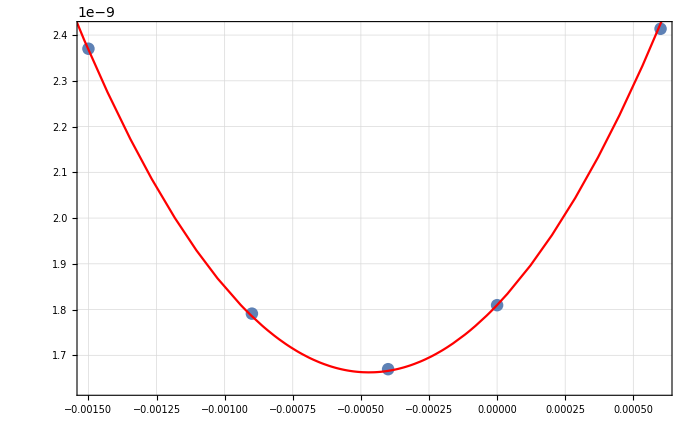
{b0 =  | -0.000470334
FittedModel[1.66271×10^-9+0.000664937 (0.000470334+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000470334 | 4.25256×10^-6 | -110.6 | 0.0000817402
scale | 0.000664937 | 8.52237×10^-6 | 78.0226 | 0.00016423
yoffset | 1.66271×10^-9 | 6.04333×10^-12 | 275.132 | 0.0000132102 | ,-Graphics-}

```mathematica
BRamp400Fit=Chi2FitandPlot[BRamp400[[1,All,2]],BRamp400[[2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

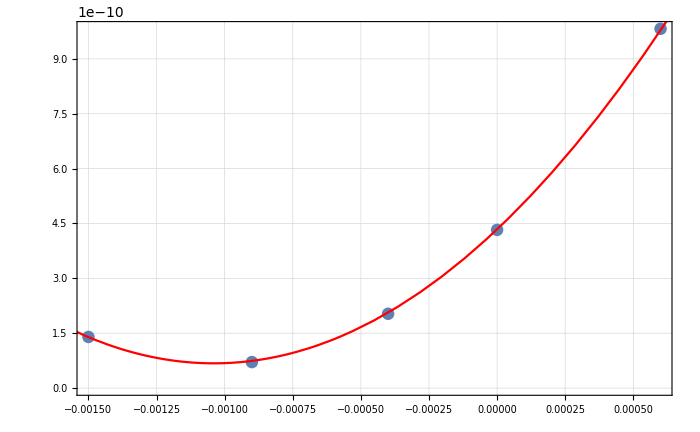
{b0 =  | -0.00104003
FittedModel[6.77227×10^-11+0.000338547 (0.00104003+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.00104003 | 8.09052×10^-6 | -128.55 | 0.0000605088
scale | 0.000338547 | 4.07339×10^-6 | 83.1117 | 0.000144738
yoffset | 6.77227×10^-11 | 2.64072×10^-12 | 25.6455 | 0.00151701 | ,-Graphics-}

```mathematica
BRamp800Fit=Chi2FitandPlot[BRamp800[[1,All,2]],BRamp800[[2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

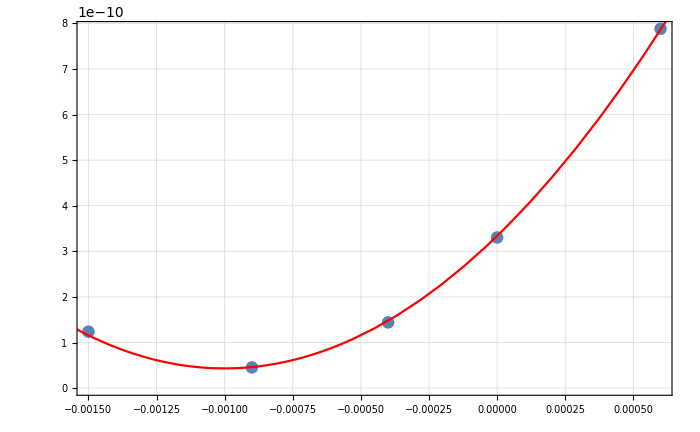
{b0 =  | -0.0010006
FittedModel[4.32052×10^-11+0.000290116 (0.0010006+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.0010006 | 0.0000141596 | -70.6656 | 0.000200195
scale | 0.000290116 | 6.43472×10^-6 | 45.086 | 0.000491582
yoffset | 4.32052×10^-11 | 4.16139×10^-12 | 10.3824 | 0.0091498 | ,-Graphics-}

```mathematica
BRamp1000Fit=Chi2FitandPlot[BRamp1000[[1,All,2]],BRamp1000[[2]],bvary]
```

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

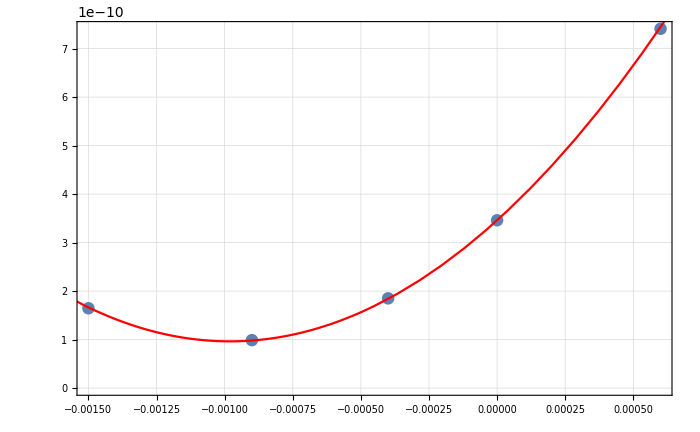
{b0 =  | -0.000980644
FittedModel[9.63981×10^-11+0.000259519 (0.000980644+b)^2] | 
 | Estimate | Standard Error | t-Statistic | P-Value
b0 | -0.000980644 | 7.04284×10^-6 | -139.24 | 0.0000515751
scale | 0.000259519 | 2.94119×10^-6 | 88.236 | 0.000128418
yoffset | 9.63981×10^-11 | 1.90304×10^-12 | 50.6548 | 0.000389498 | ,-Graphics-}

```mathematica
BRamp1200Fit=Chi2FitandPlot[BRamp1200[[1,All,2]],BRamp1200[[2]],bvary]
```

```mathematica
BRampkValues=#[[1,1,1,2]]/(5*10^-5)&/@{BRamp400Fit,BRamp800Fit,BRamp1000Fit,BRamp1200Fit}
```

{-9.40668,-20.8007,-20.012,-19.6129}

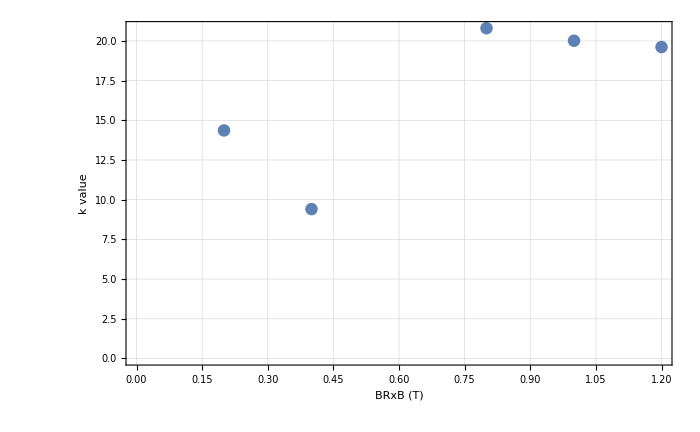

```mathematica
ListPlot[Transpose[{Join[{0.2},BRxBList],-1*Join[{-14.362014890867032},BRampkValues]}],FrameLabel->{{"k value",None},{"BRxB (T)","k value of ΔBRxB for different BRxB"}}]
```